# Project Euler

```mathematica
$Version
```

10.1.0  for Linux x86 (32-bit) (March 24, 2015)

## Tools

```mathematica
Remove@"`*";

IncreaseWhile[f_,n0_:1,d_:1]:=NestWhile[#+d&,n0,f];

(*Mathematica 10.3 already has this function, but I'm using 10.1.*)
SetAttributes[PalindromeQ,Listable];
PalindromeQ[n_Integer]:=#==Reverse@#&@IntegerDigits@n;

SetAttributes[Radical,Listable];
Radical[n_Integer]:=Times@@First/@FactorInteger@n;

PrimeRange[i_,j_]:=Prime@Range[PrimePi[i-1]+1,PrimePi@j];
PrimeRange[j_]:=Prime@Range@PrimePi@j;
```

## Problems

### Problem 1 - 25

#### Problem 1 - Multiples of 3 and 5

If we list all the natural numbers below 10 that are multiples of 3 or 5, we get 3, 5, 6 and 9. The sum of these multiples is 23.

Find the sum of all the multiples of 3 or 5 below 1000.

```mathematica
Total[Union@@Range[0,999,{3,5}]]
```

233168

#### Problem 2 - Even Fibonacci numbers

Each new term in the Fibonacci sequence is generated by adding the previous two terms. By starting with 1 and 2, the first 10 terms will be:

1, 2, 3, 5, 8, 13, 21, 34, 55, 89, ...

By considering the terms in the Fibonacci sequence whose values do not exceed four million, find the sum of the even-valued terms.

```mathematica
Sum[Fibonacci@n,{n,3,InverseFunction[Fibonacci][4*^6],3}]
```

4613732

#### Problem 3 - Largest prime factor

The prime factors of 13195 are 5, 7, 13 and 29.

What is the largest prime factor of the number 600851475143 ?

```mathematica
Max@FactorInteger@600851475143
```

6857

#### Problem 4 - Largest palindrome product

A palindromic number reads the same both ways. The largest palindrome made from the product of two 2-digit numbers is 9009 = 91 × 99.

Find the largest palindrome made from the product of two 3-digit numbers.

```mathematica
Max@Select[Catenate@Array[Times,{999,999}],PalindromeQ]
```

906609

#### Problem 5 - Smallest multiple

2520 is the smallest number that can be divided by each of the numbers from 1 to 10 without any remainder.

What is the smallest positive number that is evenly divisible by all of the numbers from 1 to 20?

```mathematica
LCM@@Range@20
```

232792560

#### Problem 6 - Sum square difference

The sum of the squares of the first ten natural numbers is,
1^2+2^2+...+10^2=385 

The square of the sum of the first ten natural numbers is,
(1+2+...+10)^2 =55^2=3025

Hence the difference between the sum of the squares of the first ten natural numbers and the square of the sum is 3025 − 385 = 2640.

Find the difference between the sum of the squares of the first one hundred natural numbers and the square of the sum.

```mathematica
Tr[#]^2-Tr[#^2]&@Range@100
```

25164150

#### Problem 7 - 10001st prime

By listing the first six prime numbers: 2, 3, 5, 7, 11, and 13, we can see that the 6th prime is 13.

What is the 10 001st prime number?

```mathematica
Prime@10001
```

104743

#### Problem 8 - Largest product in a series

The four adjacent digits in the 1000-digit number that have the greatest product are 9 × 9 × 8 × 9 = 5832.

73167176531330624919225119674426574742355349194934
96983520312774506326239578318016984801869478851843
85861560789112949495459501737958331952853208805511
12540698747158523863050715693290963295227443043557
66896648950445244523161731856403098711121722383113
62229893423380308135336276614282806444486645238749
30358907296290491560440772390713810515859307960866
70172427121883998797908792274921901699720888093776
65727333001053367881220235421809751254540594752243
52584907711670556013604839586446706324415722155397
53697817977846174064955149290862569321978468622482
83972241375657056057490261407972968652414535100474
82166370484403199890008895243450658541227588666881
16427171479924442928230863465674813919123162824586
17866458359124566529476545682848912883142607690042
24219022671055626321111109370544217506941658960408
07198403850962455444362981230987879927244284909188
84580156166097919133875499200524063689912560717606
05886116467109405077541002256983155200055935729725
71636269561882670428252483600823257530420752963450

Find the thirteen adjacent digits in the 1000-digit number that have the greatest product. What is the value of this product?

```mathematica
digits="73167176531330624919225119674426574742355349194934
96983520312774506326239578318016984801869478851843
85861560789112949495459501737958331952853208805511
12540698747158523863050715693290963295227443043557
66896648950445244523161731856403098711121722383113
62229893423380308135336276614282806444486645238749
30358907296290491560440772390713810515859307960866
70172427121883998797908792274921901699720888093776
65727333001053367881220235421809751254540594752243
52584907711670556013604839586446706324415722155397
53697817977846174064955149290862569321978468622482
83972241375657056057490261407972968652414535100474
82166370484403199890008895243450658541227588666881
16427171479924442928230863465674813919123162824586
17866458359124566529476545682848912883142607690042
24219022671055626321111109370544217506941658960408
07198403850962455444362981230987879927244284909188
84580156166097919133875499200524063689912560717606
05886116467109405077541002256983155200055935729725
71636269561882670428252483600823257530420752963450";
```

```mathematica
Max[Times@@@Partition[FromDigits/@Characters@StringDelete[digits,"\n"],13,1]]
```

23514624000

#### Problem 9 - Special Pythagorean triplet

A Pythagorean triplet is a set of three natural numbers, a < b < c, for which,
a^2+b^2=c^2

For example, 3^2+4^2=9+16=25=5^2.

There exists exactly one Pythagorean triplet for which a + b + c = 1000.
Find the product abc.

```mathematica
a b c/.First@Solve[{a^2+b^2==c^2,a+b+c==1000,c>b>a>0},{a,b,c},Integers]
```

31875000

#### Problem 10 - Summation of primes

The sum of the primes below 10 is 2 + 3 + 5 + 7 = 17.

Find the sum of all the primes below two million.

```mathematica
Total@PrimeRange@2*^6
```

142913828922

#### Problem 11 - Largest product in a grid

In the 20×20 grid below, four numbers along a diagonal line have been marked in red.

08 02 22 97 38 15 00 40 00 75 04 05 07 78 52 12 50 77 91 08
49 49 99 40 17 81 18 57 60 87 17 40 98 43 69 48 04 56 62 00
81 49 31 73 55 79 14 29 93 71 40 67 53 88 30 03 49 13 36 65
52 70 95 23 04 60 11 42 69 24 68 56 01 32 56 71 37 02 36 91
22 31 16 71 51 67 63 89 41 92 36 54 22 40 40 28 66 33 13 80
24 47 32 60 99 03 45 02 44 75 33 53 78 36 84 20 35 17 12 50
32 98 81 28 64 23 67 10 26 38 40 67 59 54 70 66 18 38 64 70
67 26 20 68 02 62 12 20 95 63 94 39 63 08 40 91 66 49 94 21
24 55 58 05 66 73 99 26 97 17 78 78 96 83 14 88 34 89 63 72
21 36 23 09 75 00 76 44 20 45 35 14 00 61 33 97 34 31 33 95
78 17 53 28 22 75 31 67 15 94 03 80 04 62 16 14 09 53 56 92
16 39 05 42 96 35 31 47 55 58 88 24 00 17 54 24 36 29 85 57
86 56 00 48 35 71 89 07 05 44 44 37 44 60 21 58 51 54 17 58
19 80 81 68 05 94 47 69 28 73 92 13 86 52 17 77 04 89 55 40
04 52 08 83 97 35 99 16 07 97 57 32 16 26 26 79 33 27 98 66
88 36 68 87 57 62 20 72 03 46 33 67 46 55 12 32 63 93 53 69
04 42 16 73 38 25 39 11 24 94 72 18 08 46 29 32 40 62 76 36
20 69 36 41 72 30 23 88 34 62 99 69 82 67 59 85 74 04 36 16
20 73 35 29 78 31 90 01 74 31 49 71 48 86 81 16 23 57 05 54
01 70 54 71 83 51 54 69 16 92 33 48 61 43 52 01 89 19 67 48

The product of these numbers is 26 × 63 × 78 × 14 = 1788696.

What is the greatest product of four adjacent numbers in the same direction (up, down, left, right, or diagonally) in the 20×20 grid?

```mathematica
grid=ImportString[" 08 02 22 97 38 15 00 40 00 75 04 05 07 78 52 12 50 77 91 08
49 49 99 40 17 81 18 57 60 87 17 40 98 43 69 48 04 56 62 00
81 49 31 73 55 79 14 29 93 71 40 67 53 88 30 03 49 13 36 65
52 70 95 23 04 60 11 42 69 24 68 56 01 32 56 71 37 02 36 91
22 31 16 71 51 67 63 89 41 92 36 54 22 40 40 28 66 33 13 80
24 47 32 60 99 03 45 02 44 75 33 53 78 36 84 20 35 17 12 50
32 98 81 28 64 23 67 10 26 38 40 67 59 54 70 66 18 38 64 70
67 26 20 68 02 62 12 20 95 63 94 39 63 08 40 91 66 49 94 21
24 55 58 05 66 73 99 26 97 17 78 78 96 83 14 88 34 89 63 72
21 36 23 09 75 00 76 44 20 45 35 14 00 61 33 97 34 31 33 95
78 17 53 28 22 75 31 67 15 94 03 80 04 62 16 14 09 53 56 92
16 39 05 42 96 35 31 47 55 58 88 24 00 17 54 24 36 29 85 57
86 56 00 48 35 71 89 07 05 44 44 37 44 60 21 58 51 54 17 58
19 80 81 68 05 94 47 69 28 73 92 13 86 52 17 77 04 89 55 40
04 52 08 83 97 35 99 16 07 97 57 32 16 26 26 79 33 27 98 66
88 36 68 87 57 62 20 72 03 46 33 67 46 55 12 32 63 93 53 69
04 42 16 73 38 25 39 11 24 94 72 18 08 46 29 32 40 62 76 36
20 69 36 41 72 30 23 88 34 62 99 69 82 67 59 85 74 04 36 16
20 73 35 29 78 31 90 01 74 31 49 71 48 86 81 16 23 57 05 54
01 70 54 71 83 51 54 69 16 92 33 48 61 43 52 01 89 19 67 48","Table"];
```

```mathematica
Max[Times@@@Partition[#,4,1]&/@Flatten[{Table[Diagonal[#,n]&/@{grid,Reverse@grid},{n,-20,20}],{grid,Transpose@grid}},2]]
```

70600674

#### Problem 12 - Highly divisible triangular number

The sequence of triangle numbers is generated by adding the natural numbers. So the 7th triangle number would be 1 + 2 + 3 + 4 + 5 + 6 + 7 = 28. The first ten terms would be:

1, 3, 6, 10, 15, 21, 28, 36, 45, 55, ...

Let us list the factors of the first seven triangle numbers:

     1: 1
     3: 1,3
     6: 1,2,3,6
    10: 1,2,5,10
    15: 1,3,5,15
    21: 1,3,7,21
    28: 1,2,4,7,14,28

We can see that 28 is the first triangle number to have over five divisors.

What is the value of the first triangle number to have over five hundred divisors?

```mathematica
{1,2}//.{i_/;DivisorSigma[0,i]≤500,j_}:>{i+j,j+1}//First
```

76576500

#### Problem 13 - Large sum

Work out the first ten digits of the sum of the following one-hundred 50-digit numbers.
37107287533902102798797998220837590246510135740250
46376937677490009712648124896970078050417018260538
74324986199524741059474233309513058123726617309629
91942213363574161572522430563301811072406154908250
23067588207539346171171980310421047513778063246676
89261670696623633820136378418383684178734361726757
28112879812849979408065481931592621691275889832738
44274228917432520321923589422876796487670272189318
47451445736001306439091167216856844588711603153276
70386486105843025439939619828917593665686757934951
62176457141856560629502157223196586755079324193331
64906352462741904929101432445813822663347944758178
92575867718337217661963751590579239728245598838407
58203565325359399008402633568948830189458628227828
80181199384826282014278194139940567587151170094390
35398664372827112653829987240784473053190104293586
86515506006295864861532075273371959191420517255829
71693888707715466499115593487603532921714970056938
54370070576826684624621495650076471787294438377604
53282654108756828443191190634694037855217779295145
36123272525000296071075082563815656710885258350721
45876576172410976447339110607218265236877223636045
17423706905851860660448207621209813287860733969412
81142660418086830619328460811191061556940512689692
51934325451728388641918047049293215058642563049483
62467221648435076201727918039944693004732956340691
15732444386908125794514089057706229429197107928209
55037687525678773091862540744969844508330393682126
18336384825330154686196124348767681297534375946515
80386287592878490201521685554828717201219257766954
78182833757993103614740356856449095527097864797581
16726320100436897842553539920931837441497806860984
48403098129077791799088218795327364475675590848030
87086987551392711854517078544161852424320693150332
59959406895756536782107074926966537676326235447210
69793950679652694742597709739166693763042633987085
41052684708299085211399427365734116182760315001271
65378607361501080857009149939512557028198746004375
35829035317434717326932123578154982629742552737307
94953759765105305946966067683156574377167401875275
88902802571733229619176668713819931811048770190271
25267680276078003013678680992525463401061632866526
36270218540497705585629946580636237993140746255962
24074486908231174977792365466257246923322810917141
91430288197103288597806669760892938638285025333403
34413065578016127815921815005561868836468420090470
23053081172816430487623791969842487255036638784583
11487696932154902810424020138335124462181441773470
63783299490636259666498587618221225225512486764533
67720186971698544312419572409913959008952310058822
95548255300263520781532296796249481641953868218774
76085327132285723110424803456124867697064507995236
37774242535411291684276865538926205024910326572967
23701913275725675285653248258265463092207058596522
29798860272258331913126375147341994889534765745501
18495701454879288984856827726077713721403798879715
38298203783031473527721580348144513491373226651381
34829543829199918180278916522431027392251122869539
40957953066405232632538044100059654939159879593635
29746152185502371307642255121183693803580388584903
41698116222072977186158236678424689157993532961922
62467957194401269043877107275048102390895523597457
23189706772547915061505504953922979530901129967519
86188088225875314529584099251203829009407770775672
11306739708304724483816533873502340845647058077308
82959174767140363198008187129011875491310547126581
97623331044818386269515456334926366572897563400500
42846280183517070527831839425882145521227251250327
55121603546981200581762165212827652751691296897789
32238195734329339946437501907836945765883352399886
75506164965184775180738168837861091527357929701337
62177842752192623401942399639168044983993173312731
32924185707147349566916674687634660915035914677504
99518671430235219628894890102423325116913619626622
73267460800591547471830798392868535206946944540724
76841822524674417161514036427982273348055556214818
97142617910342598647204516893989422179826088076852
87783646182799346313767754307809363333018982642090
10848802521674670883215120185883543223812876952786
71329612474782464538636993009049310363619763878039
62184073572399794223406235393808339651327408011116
66627891981488087797941876876144230030984490851411
60661826293682836764744779239180335110989069790714
85786944089552990653640447425576083659976645795096
66024396409905389607120198219976047599490197230297
64913982680032973156037120041377903785566085089252
16730939319872750275468906903707539413042652315011
94809377245048795150954100921645863754710598436791
78639167021187492431995700641917969777599028300699
15368713711936614952811305876380278410754449733078
40789923115535562561142322423255033685442488917353
44889911501440648020369068063960672322193204149535
41503128880339536053299340368006977710650566631954
81234880673210146739058568557934581403627822703280
82616570773948327592232845941706525094512325230608
22918802058777319719839450180888072429661980811197
77158542502016545090413245809786882778948721859617
72107838435069186155435662884062257473692284509516
20849603980134001723930671666823555245252804609722
53503534226472524250874054075591789781264330331690

```mathematica
numbers=ImportString["37107287533902102798797998220837590246510135740250
46376937677490009712648124896970078050417018260538
74324986199524741059474233309513058123726617309629
91942213363574161572522430563301811072406154908250
23067588207539346171171980310421047513778063246676
89261670696623633820136378418383684178734361726757
28112879812849979408065481931592621691275889832738
44274228917432520321923589422876796487670272189318
47451445736001306439091167216856844588711603153276
70386486105843025439939619828917593665686757934951
62176457141856560629502157223196586755079324193331
64906352462741904929101432445813822663347944758178
92575867718337217661963751590579239728245598838407
58203565325359399008402633568948830189458628227828
80181199384826282014278194139940567587151170094390
35398664372827112653829987240784473053190104293586
86515506006295864861532075273371959191420517255829
71693888707715466499115593487603532921714970056938
54370070576826684624621495650076471787294438377604
53282654108756828443191190634694037855217779295145
36123272525000296071075082563815656710885258350721
45876576172410976447339110607218265236877223636045
17423706905851860660448207621209813287860733969412
81142660418086830619328460811191061556940512689692
51934325451728388641918047049293215058642563049483
62467221648435076201727918039944693004732956340691
15732444386908125794514089057706229429197107928209
55037687525678773091862540744969844508330393682126
18336384825330154686196124348767681297534375946515
80386287592878490201521685554828717201219257766954
78182833757993103614740356856449095527097864797581
16726320100436897842553539920931837441497806860984
48403098129077791799088218795327364475675590848030
87086987551392711854517078544161852424320693150332
59959406895756536782107074926966537676326235447210
69793950679652694742597709739166693763042633987085
41052684708299085211399427365734116182760315001271
65378607361501080857009149939512557028198746004375
35829035317434717326932123578154982629742552737307
94953759765105305946966067683156574377167401875275
88902802571733229619176668713819931811048770190271
25267680276078003013678680992525463401061632866526
36270218540497705585629946580636237993140746255962
24074486908231174977792365466257246923322810917141
91430288197103288597806669760892938638285025333403
34413065578016127815921815005561868836468420090470
23053081172816430487623791969842487255036638784583
11487696932154902810424020138335124462181441773470
63783299490636259666498587618221225225512486764533
67720186971698544312419572409913959008952310058822
95548255300263520781532296796249481641953868218774
76085327132285723110424803456124867697064507995236
37774242535411291684276865538926205024910326572967
23701913275725675285653248258265463092207058596522
29798860272258331913126375147341994889534765745501
18495701454879288984856827726077713721403798879715
38298203783031473527721580348144513491373226651381
34829543829199918180278916522431027392251122869539
40957953066405232632538044100059654939159879593635
29746152185502371307642255121183693803580388584903
41698116222072977186158236678424689157993532961922
62467957194401269043877107275048102390895523597457
23189706772547915061505504953922979530901129967519
86188088225875314529584099251203829009407770775672
11306739708304724483816533873502340845647058077308
82959174767140363198008187129011875491310547126581
97623331044818386269515456334926366572897563400500
42846280183517070527831839425882145521227251250327
55121603546981200581762165212827652751691296897789
32238195734329339946437501907836945765883352399886
75506164965184775180738168837861091527357929701337
62177842752192623401942399639168044983993173312731
32924185707147349566916674687634660915035914677504
99518671430235219628894890102423325116913619626622
73267460800591547471830798392868535206946944540724
76841822524674417161514036427982273348055556214818
97142617910342598647204516893989422179826088076852
87783646182799346313767754307809363333018982642090
10848802521674670883215120185883543223812876952786
71329612474782464538636993009049310363619763878039
62184073572399794223406235393808339651327408011116
66627891981488087797941876876144230030984490851411
60661826293682836764744779239180335110989069790714
85786944089552990653640447425576083659976645795096
66024396409905389607120198219976047599490197230297
64913982680032973156037120041377903785566085089252
16730939319872750275468906903707539413042652315011
94809377245048795150954100921645863754710598436791
78639167021187492431995700641917969777599028300699
15368713711936614952811305876380278410754449733078
40789923115535562561142322423255033685442488917353
44889911501440648020369068063960672322193204149535
41503128880339536053299340368006977710650566631954
81234880673210146739058568557934581403627822703280
82616570773948327592232845941706525094512325230608
22918802058777319719839450180888072429661980811197
77158542502016545090413245809786882778948721859617
72107838435069186155435662884062257473692284509516
20849603980134001723930671666823555245252804609722
53503534226472524250874054075591789781264330331690","List"];
```

```mathematica
FromDigits@Take[IntegerDigits@Total@numbers,10]
```

5537376230

#### Problem 14 - Longest Collatz sequence

The following iterative sequence is defined for the set of positive integers:

n → n/2 (n is even)
n → 3n + 1 (n is odd)

Using the rule above and starting with 13, we generate the following sequence:
13 → 40 → 20 → 10 → 5 → 16 → 8 → 4 → 2 → 1

It can be seen that this sequence (starting at 13 and finishing at 1) contains 10 terms. Although it has not been proved yet (Collatz Problem), it is thought that all starting numbers finish at 1.

Which starting number, under one million, produces the longest chain?

NOTE: Once the chain starts the terms are allowed to go above one million.

```mathematica
collatz[1]=1;
collatz[n_]:=collatz[n]=collatz[If[OddQ@n,3n+1,n/2]]+1;
```

```mathematica
First@MaximalBy[Range@1*^6,collatz]
```

837799

#### Problem 15 - Lattice paths

Starting in the top left corner of a 2×2 grid, and only being able to move to the right and down, there are exactly 6 routes to the bottom right corner.
-Graphics-
How many such routes are there through a 20×20 grid?

```mathematica
40~Binomial~20
```

137846528820

#### Problem 16 - Power digit sum

2^15 =32768 and the sum of its digits is 3 + 2 + 7 + 6 + 8 = 26.

What is the sum of the digits of the number 2^1000?

```mathematica
Total@IntegerDigits[2^1000]
```

1366

#### Problem 17 - Number letter counts

If the numbers 1 to 5 are written out in words: one, two, three, four, five, then there are 3 + 3 + 5 + 4 + 4 = 19 letters used in total.

If all the numbers from 1 to 1000 (one thousand) inclusive were written out in words, how many letters would be used?

NOTE: Do not count spaces or hyphens. For example, 342 (three hundred and forty-two) contains 23 letters and 115 (one hundred and fifteen) contains 20 letters. The use of “and” when writing out numbers is in compliance with British usage.

```mathematica
numberString[{1}]="one";
numberString[{2}]="two";
numberString[{3}]="three";
numberString[{4}]="four";
numberString[{5}]="five";
numberString[{6}]="six";
numberString[{7}]="seven";
numberString[{8}]="eight";
numberString[{9}]="nine";
numberString[{1,0}]="ten";
numberString[{1,1}]="eleven";
numberString[{1,2}]="twelve";
numberString[{1,3}]="thirteen";
numberString[{1,5}]="fifteen";
numberString[{1,8}]="eighteen";
numberString[{1,i_}]:=numberString[{i}]<>"teen";
numberString[{2,0}]="twenty";
numberString[{3,0}]="thirty";
numberString[{4,0}]="forty";
numberString[{5,0}]="fifty";
numberString[{8,0}]="eighty";
numberString[{i_,0}]:=numberString[{i}]<>"ty";
numberString[{i_,j_}]:=numberString[{i,0}]<>numberString[{j}];
numberString[{i_,0,0}]:=numberString[{i}]<>"hundred";
numberString[{i_,0,j_}]:=numberString[{i,0,0}]<>"and"<>numberString[{j}];
numberString[{i_,j_,k_}]:=numberString[{i,0,0}]<>"and"<>numberString[{j,k}];
numberString[{1,0,0,0}]="onethousand";
```

```mathematica
Sum[StringLength@numberString@IntegerDigits@i,{i,1000}]
```

21124

#### Problem 18 - Maximum path sum I

By starting at the top of the triangle below and moving to adjacent numbers on the row below, the maximum total from top to bottom is 23.

3
7 4
2 4 6
8 5 9 3

That is, 3 + 7 + 4 + 9 = 23.

Find the maximum total from top to bottom of the triangle below:

75
95 64
17 47 82
18 35 87 10
20 04 82 47 65
19 01 23 75 03 34
88 02 77 73 07 63 67
99 65 04 28 06 16 70 92
41 41 26 56 83 40 80 70 33
41 48 72 33 47 32 37 16 94 29
53 71 44 65 25 43 91 52 97 51 14
70 11 33 28 77 73 17 78 39 68 17 57
91 71 52 38 17 14 91 43 58 50 27 29 48
63 66 04 68 89 53 67 30 73 16 69 87 40 31
04 62 98 27 23 09 70 98 73 93 38 53 60 04 23

NOTE: As there are only 16384 routes, it is possible to solve this problem by trying every route. However, Problem 67, is the same challenge with a triangle containing one-hundred rows; it cannot be solved by brute force, and requires a clever method! ;o)

```mathematica
triangle=ImportString["75
95 64
17 47 82
18 35 87 10
20 04 82 47 65
19 01 23 75 03 34
88 02 77 73 07 63 67
99 65 04 28 06 16 70 92
41 41 26 56 83 40 80 70 33
41 48 72 33 47 32 37 16 94 29
53 71 44 65 25 43 91 52 97 51 14
70 11 33 28 77 73 17 78 39 68 17 57
91 71 52 38 17 14 91 43 58 50 27 29 48
63 66 04 68 89 53 67 30 73 16 69 87 40 31
04 62 98 27 23 09 70 98 73 93 38 53 60 04 23","Table"];
```

```mathematica
Max@Fold[MapThread[Max,{Append[#,0]+#2,Prepend[#,0]+#2}]&,{},triangle]
```

1074

#### Problem 19 - Counting Sundays

You are given the following information, but you may prefer to do some research for yourself.

    1 Jan 1900 was a Monday.
    Thirty days has September,
    April, June and November.
    All the rest have thirty-one,
    Saving February alone,
    Which has twenty-eight, rain or shine.
    And on leap years, twenty-nine.
    A leap year occurs on any year evenly divisible by 4, but not on a century unless it is divisible by 400.

How many Sundays fell on the first of the month during the twentieth century (1 Jan 1901 to 31 Dec 2000)?

```mathematica
Count[DateRange[{1901,1,1},{2000,12,31},Sunday],{_,_,1}]
```

171

#### Problem 20 - Factorial digit sum

n! means n × (n − 1) × ... × 3 × 2 × 1

For example, 10! = 10 × 9 × ... × 3 × 2 × 1 = 3628800,
and the sum of the digits in the number 10! is 3 + 6 + 2 + 8 + 8 + 0 + 0 = 27.

Find the sum of the digits in the number 100!

```mathematica
Total@IntegerDigits[100!]
```

648

#### Problem 21 - Amicable numbers

Let d(n) be defined as the sum of proper divisors of n (numbers less than n which divide evenly into n).
If d(a) = b and d(b) = a, where a ≠ b, then a and b are an amicable pair and each of a and b are called amicable numbers.

For example, the proper divisors of 220 are 1, 2, 4, 5, 10, 11, 20, 22, 44, 55 and 110; therefore d(220) = 284. The proper divisors of 284 are 1, 2, 4, 71 and 142; so d(284) = 220.

Evaluate the sum of all the amicable numbers under 10000.

```mathematica
Total@Select[Range@10000,#1==#3≠#2&@@NestList[DivisorSigma[1,#]-#&,#,2]&]
```

31626

#### Problem 22 - Names scores

Using names.txt (right click and ‘Save Link/Target As...’), a 46K text file containing over five-thousand first names, begin by sorting it into alphabetical order. Then working out the alphabetical value for each name, multiply this value by its alphabetical position in the list to obtain a name score.

For example, when the list is sorted into alphabetical order, COLIN, which is worth 3 + 15 + 12 + 9 + 14 = 53, is the 938th name in the list. So, COLIN would obtain a score of 938 × 53 = 49714.

What is the total of all the name scores in the file?

```mathematica
names=ToExpression["{"<>Import@"https://projecteuler.net/project/resources/p022_names.txt"<>"}"];
```

```mathematica
Total[MapIndexed[Total[ToCharacterCode@#1-64]#2&,Sort@names],2]
```

871198282

#### Problem 23 - Non-abundant sums

A perfect number is a number for which the sum of its proper divisors is exactly equal to the number. For example, the sum of the proper divisors of 28 would be 1 + 2 + 4 + 7 + 14 = 28, which means that 28 is a perfect number.

A number n is called deficient if the sum of its proper divisors is less than n and it is called abundant if this sum exceeds n.

As 12 is the smallest abundant number, 1 + 2 + 3 + 4 + 6 = 16, the smallest number that can be written as the sum of two abundant numbers is 24. By mathematical analysis, it can be shown that all integers greater than 28123 can be written as the sum of two abundant numbers. However, this upper limit cannot be reduced any further by analysis even though it is known that the greatest number that cannot be expressed as the sum of two abundant numbers is less than this limit.

Find the sum of all the positive integers which cannot be written as the sum of two abundant numbers.

```mathematica
abundants=Select[Range@28123,DivisorSigma[1,#]>2 #&];
Total[Fold[Complement[#,#2+abundants]&,Range@28123,abundants]]
```

4179871

#### Problem 24 - Lexicographic permutations

A permutation is an ordered arrangement of objects. For example, 3124 is one possible permutation of the digits 1, 2, 3 and 4. If all of the permutations are listed numerically or alphabetically, we call it lexicographic order. The lexicographic permutations of 0, 1 and 2 are:

012   021   102   120   201   210

What is the millionth lexicographic permutation of the digits 0, 1, 2, 3, 4, 5, 6, 7, 8 and 9?

```mathematica
FromDigits[Permutations[Range[0,9]][[1*^6]]]
```

2783915460

#### Problem 25 - 1000-digit Fibonacci number

The Fibonacci sequence is defined by the recurrence relation:

    F_n =F_(n−1)+F_(n−2), where F_1 =1 and F_2 =1.

Hence the first 12 terms will be:

    F_1 =1
    F_2 =1
    F_3 =2
    F_4 =3
    F_5 =5
    F_6 =8
    F_7 =13
    F_8 =21
    F_9 =34
    F_10 =55
    F_11 =89
    F_12 =144

The 12th term, F_12, is the first term to contain three digits.

What is the index of the first term in the Fibonacci sequence to contain 1000 digits?

```mathematica
IncreaseWhile[Log10@Fibonacci@#<999&]
```

4782

### Problem 26 - 50

#### Problem 26 - Reciprocal cycles

A unit fraction contains 1 in the numerator. The decimal representation of the unit fractions with denominators 2 to 10 are given:

    1/2	= 	0.5
    1/3	= 	0.(3)
    1/4	= 	0.25
    1/5	= 	0.2
    1/6	= 	0.1(6)
    1/7	= 	0.(142857)
    1/8	= 	0.125
    1/9	= 	0.(1)
    1/10	= 	0.1

Where 0.1(6) means 0.166666..., and has a 1-digit recurring cycle. It can be seen that 1/7 has a 6-digit recurring cycle.

Find the value of d < 1000 for which 1/d contains the longest recurring cycle in its decimal fraction part.

```mathematica
First@MaximalBy[Range@1000,Length@RealDigits[1/#][[1,-1]]&]
```

983

#### Problem 27 - Quadratic primes

Euler discovered the remarkable quadratic formula:

n.b2 + n + 41

It turns out that the formula will produce 40 primes for the consecutive values n = 0 to 39. However, when n = 40, 40.b2 + 40 + 41 = 40(40 + 1) + 41 is divisible by 41, and certainly when n = 41, 41.b2 + 41 + 41 is clearly divisible by 41.

The incredible formula  n.b2 − 79n + 1601 was discovered, which produces 80 primes for the consecutive values n = 0 to 79. The product of the coefficients, −79 and 1601, is −126479.

Considering quadratics of the form:

    n.b2 + an + b, where |a| < 1000 and |b| < 1000

    where |n| is the modulus/absolute value of n
    e.g. |11| = 11 and |−4| = 4

Find the product of the coefficients, a and b, for the quadratic expression that produces the maximum number of primes for consecutive values of n, starting with n = 0.

```mathematica
n=Ceiling@Root[#^2+#+41-1000&,1]
```

-31

```mathematica
Times@@CoefficientList[(x+n)^2+(x+n)+41,x]
```

-59231

#### Problem 28 - Number spiral diagonals

Starting with the number 1 and moving to the right in a clockwise direction a 5 by 5 spiral is formed as follows:

21 22 23 24 25
20  7  8  9 10
19  6  1  2 11
18  5  4  3 12
17 16 15 14 13

It can be verified that the sum of the numbers on the diagonals is 101.

What is the sum of the numbers on the diagonals in a 1001 by 1001 spiral formed in the same way?

```mathematica
1+4Sum[4n^2+n+1,{n,(1001-1)/2}]
```

669171001

#### Problem 29 - Distinct powers

Consider all integer combinations of a^b for 2 ≤ a ≤ 5 and 2 ≤ b ≤ 5:

    2^2=4,2^3=8,2^4=16,2^5=32
    3^2=9, 3^3=27, 3^4=81, 3^5=243
    4^2=16, 4^3=64, 4^4=256, 4^5=1024
    5^2=25, 5^3=125, 5^4=625, 5^5=3125

If they are then placed in numerical order, with any repeats removed, we get the following sequence of 15 distinct terms:

4, 8, 9, 16, 25, 27, 32, 64, 81, 125, 243, 256, 625, 1024, 3125

How many distinct terms are in the sequence generated by a^b for 2 ≤ a ≤ 100 and 2 ≤ b ≤ 100?

```mathematica
Length@DeleteDuplicates@Catenate@Array[Power,{99,99},2]
```

9183

#### Problem 30 - Digit fifth powers

Surprisingly there are only three numbers that can be written as the sum of fourth powers of their digits:

    1634=1^4+6^4+3^4+4^4
    8208=8^4+2^4+0^4+8^4
    9474=9^4+4^4+7^4+4^4

As 1=1^4 is not a sum it is not included.

The sum of these numbers is 1634 + 8208 + 9474 = 19316.

Find the sum of all the numbers that can be written as the sum of fifth powers of their digits.

```mathematica
nmax=IncreaseWhile[9^5#>10^#&];Total@Select[Range[9^5nmax],Total[IntegerDigits@#^5]==#&]-1
```

443839

#### Problem 31 - Coin sums

In England the currency is made up of pound, £, and pence, p, and there are eight coins in general circulation:

    1p, 2p, 5p, 10p, 20p, 50p, £1 (100p) and £2 (200p).

It is possible to make £2 in the following way:

    1×£1 + 1×50p + 2×20p + 1×5p + 1×2p + 3×1p

How many different ways can £2 be made using any number of coins?

```mathematica
Length@FrobeniusSolve[{1,2,5,10,20,50,100,200},200]
```

73682

#### Problem 32 - Pandigital products

We shall say that an n-digit number is pandigital if it makes use of all the digits 1 to n exactly once; for example, the 5-digit number, 15234, is 1 through 5 pandigital.

The product 7254 is unusual, as the identity, 39 × 186 = 7254, containing multiplicand, multiplier, and product is 1 through 9 pandigital.

Find the sum of all products whose multiplicand/multiplier/product identity can be written as a 1 through 9 pandigital.
HINT: Some products can be obtained in more than one way so be sure to only include it once in your sum.

```mathematica
Total@DeleteDuplicates@Reap[Do[If[Sort@Catenate@IntegerDigits@{i,j,i*j}==Range@9,Sow[i*j]],{i,100},{j,10000/i}]][[2,1]]
```

45228

#### Problem 33 - Digit cancelling fractions

The fraction 49/98 is a curious fraction, as an inexperienced mathematician in attempting to simplify it may incorrectly believe that 49/98 = 4/8, which is correct, is obtained by cancelling the 9s.

We shall consider fractions like, 30/50 = 3/5, to be trivial examples.

There are exactly four non-trivial examples of this type of fraction, less than one in value, and containing two digits in the numerator and denominator.

If the product of these four fractions is given in its lowest common terms, find the value of the denominator.

```mathematica
Denominator[Times@@Cases[Array[{(10#2+#)/(10#+#3),#2/#3}&,{9,9,9}],{n_,n_}/;n<1:>n,{3}]]
```

100

#### Problem 34 - Digit factorials

145 is a curious number, as 1! + 4! + 5! = 1 + 24 + 120 = 145.

Find the sum of all numbers which are equal to the sum of the factorial of their digits.

Note: as 1! = 1 and 2! = 2 are not sums they are not included.

```mathematica
nmax=IncreaseWhile[9!#>10^#&];Total@Select[Range[9!nmax],Total[IntegerDigits@#!]==#&]-1-2
```

40730

#### Problem 35 - Circular primes

The number, 197, is called a circular prime because all rotations of the digits: 197, 971, and 719, are themselves prime.

There are thirteen such primes below 100: 2, 3, 5, 7, 11, 13, 17, 31, 37, 71, 73, 79, and 97.

How many circular primes are there below one million?

```mathematica
4+Length@Catenate@Table[Select[Tuples[{1,3,7,9},n],PrimeQ/@And@@FromDigits/@NestList[RotateLeft,#,n]&],{n,2,6}]
```

55

#### Problem 36 - Double-base palindromes

The decimal number, 585=1001001001_2 (binary), is palindromic in both bases.

Find the sum of all numbers, less than one million, which are palindromic in base 10 and base 2.

(Please note that the palindromic number, in either base, may not include leading zeros.)

```mathematica
Total[Select[Range[1*^6],Reverse@#==#&/@And@@IntegerDigits[#,{2,10}]&]]
```

872187

#### Problem 37 - Truncatable primes

The number 3797 has an interesting property. Being prime itself, it is possible to continuously remove digits from left to right, and remain prime at each stage: 3797, 797, 97, and 7. Similarly we can work from right to left: 3797, 379, 37, and 3.

Find the sum of the only eleven primes that are both truncatable from left to right and right to left.

NOTE: 2, 3, 5, and 7 are not considered to be truncatable primes.

```mathematica
Total@Rest@NestList[NestWhile[NextPrime,#+1,!And@@Table[i==0||PrimeQ@FromDigits@Take[#,i],{i,-Length@#,Length@#}]&@IntegerDigits@#&]&,7,11]
```

748317

#### Problem 38 - Pandigital multiples

Take the number 192 and multiply it by each of 1, 2, and 3:

    192 × 1 = 192
    192 × 2 = 384
    192 × 3 = 576

By concatenating each product we get the 1 to 9 pandigital, 192384576. We will call 192384576 the concatenated product of 192 and (1,2,3)

The same can be achieved by starting with 9 and multiplying by 1, 2, 3, 4, and 5, giving the pandigital, 918273645, which is the concatenated product of 9 and (1,2,3,4,5).

What is the largest 1 to 9 pandigital 9-digit number that can be formed as the concatenated product of an integer with (1,2, ... , n) where n > 1?

```mathematica
Max[FromDigits/@Select[Catenate@Table[Catenate@IntegerDigits[j*Range@i],{i,2,5},{j,10^(5-i),10^(6-i)}],Sort@#==Range@9&]]
```

932718654

#### Problem 39 - Integer right triangles

If p is the perimeter of a right angle triangle with integral length sides, {a,b,c}, there are exactly three solutions for p = 120.

{20,48,52}, {24,45,51}, {30,40,50}

For which value of p ≤ 1000, is the number of solutions maximised?

```mathematica
First@Commonest@Flatten@Table[If[CoprimeQ@@#,Range[1000/#]#&@Total@#,{}]&@{m^2-n^2,2m n,m^2+n^2},{m,Sqrt@500},{n,m-1}]
```

840

#### Problem 40 - Champernowne’s constant

An irrational decimal fraction is created by concatenating the positive integers:

0.123456789101112131415161718192021...

It can be seen that the 12^th digit of the fractional part is 1.

If d_n represents the n^th digit of the fractional part, find the value of the following expression.

d_1 × d_10 × d_100 × d_1000 × d_10000 × d_100000 × d_1000000

```mathematica
Times@@RealDigits[ChampernowneNumber[10],10,1000000][[1,10^Range[0,6]]]
```

210

#### Problem 41 - Pandigital prime

We shall say that an n-digit number is pandigital if it makes use of all the digits 1 to n exactly once. For example, 2143 is a 4-digit pandigital and is also prime.

What is the largest n-digit pandigital prime that exists?

```mathematica
SelectFirst[Reverse@Catenate@Table[FromDigits/@Permutations@Range@i,{i,9}],PrimeQ]
```

7652413

#### Problem 42 - Coded triangle numbers

The n^th term of the sequence of triangle numbers is given by, t_n =.bd n(n+1); so the first ten triangle numbers are:

1, 3, 6, 10, 15, 21, 28, 36, 45, 55, ...

By converting each letter in a word to a number corresponding to its alphabetical position and adding these values we form a word value. For example, the word value for SKY is 19+11+25=55=t_10. If the word value is a triangle number then we shall call the word a triangle word.

Using words.txt (right click and ‘Save Link/Target As...’), a 16K text file containing nearly two-thousand common English words, how many are triangle words?

```mathematica
Solve[1/2n(n+1)==t,n]
```

{{n→1/2 (-1-√(1+8 t))},{n→1/2 (-1+√(1+8 t))}}

```mathematica
words=ToExpression["{"<>Import@"https://projecteuler.net/project/resources/p042_words.txt"<>"}"];
```

```mathematica
Length@Select[words,IntegerQ[Sqrt[1+8Total[ToCharacterCode@#-64]]]&]
```

162

#### Problem 43 - Sub-string divisibility

The number, 1406357289, is a 0 to 9 pandigital number because it is made up of each of the digits 0 to 9 in some order, but it also has a rather interesting sub-string divisibility property.

Let d_1 be the 1^st s digit, d_2 be the 2^nd digit, and so on. In this way, we note the following:

    d_2 d_3 d_4=406 is divisible by 2
    d_3 d_4 d_5=063 is divisible by 3
    d_4 d_5 d_6=635 is divisible by 5
    d_5 d_6 d_7=357 is divisible by 7
    d_6 d_7 d_8=572 is divisible by 11
    d_7 d_8 d_9=728 is divisible by 13
    d_8 d_9 d_10=289 is divisible by 17

Find the sum of all 0 to 9 pandigital numbers with this property.

```mathematica
Total[FromDigits/@Fold[Cases[Catenate[Through@(Append/@Complement[Range[0,9],#])@#&/@#],ds_/;Divisible[Mod[FromDigits@ds,1000],#2]]&,DeleteCases[Permutations[Range[0,9],{3}],{0,__}],{2,3,5,7,11,13,17}]]
```

16695334890

#### Problem 44 - Pentagon numbers

Pentagonal numbers are generated by the formula, P_n=n(3n−1)/2. The first ten pentagonal numbers are:

1, 5, 12, 22, 35, 51, 70, 92, 117, 145, ...

It can be seen that P_4 + P_7 = 22 + 70 = 92 = P_8. However, their difference, 70 − 22 = 48, is not pentagonal.

Find the pair of pentagonal numbers, P_j and P_k, for which their sum and difference are pentagonal and D = |P_k − P_j| is minimised; what is the value of D?

```mathematica
p[n_]:=n(3n-1)/2
```

```mathematica
Solve[p[n]==x,n]
```

{{n→1/6 (1-√(1+24 x))},{n→1/6 (1+√(1+24 x))}}

```mathematica
pentagonalQ[x_]:=IntegerQ[(1+Sqrt[1+24x])/6];
```

```mathematica
Solve[p[k+i]-p[k]==p[d],k]
```

{{k→(-d+3 d^2+i-3 i^2)/(6 i)}}

```mathematica
p@IncreaseWhile[!Or@@Table[IntegerQ@#&&pentagonalQ[p[#+i]+p[#]]&[(-#+3#^2+i-3i^2)/(6i)],{i,#-1}]&]
```

5482660

#### Problem 45 - Triangular, pentagonal, and hexagonal

Triangle, pentagonal, and hexagonal numbers are generated by the following formulae:
Triangle 	  	T_n=n(n+1)/2 	  	1, 3, 6, 10, 15, ...
Pentagonal 	  	P_n=n(3n−1)/2 	  	1, 5, 12, 22, 35, ...
Hexagonal 	  	H_n=n(2n−1) 	  	1, 6, 15, 28, 45, ...

It can be verified that T_285 = P_165 = H_143 = 40755.

Find the next triangle number that is also pentagonal and hexagonal.

```mathematica
solution=Solve[{1/2n(3n-1)==m(2m-1),m>0,n>0},{m,n},Integers]
```

{{m→ConditionalExpression[1/48 (12+2 (3 (7-4 √3)^(1+2 C[1])+√3 (7-4 √3)^(1+2 C[1])+3 (7+4 √3)^(1+2 C[1])-√3 (7+4 √3)^(1+2 C[1]))),C[1]∈Integers&&C[1]≥0],n→ConditionalExpression[1/6 (1+1/2 (-(7-4 √3)^(1+2 C[1])-√3 (7-4 √3)^(1+2 C[1])-(7+4 √3)^(1+2 C[1])+√3 (7+4 √3)^(1+2 C[1]))),C[1]∈Integers&&C[1]≥0]}}

```mathematica
m(2m-1)/.First@solution/.C[1]->2//FullSimplify
```

1533776805

#### Problem 46 - Goldbach’s other conjecture

It was proposed by Christian Goldbach that every odd composite number can be written as the sum of a prime and twice a square.

9 = 7 + 2×1^2
15 = 7 + 2×2^2
21 = 3 + 2×3^2
25 = 7 + 2×3^2
27 = 19 + 2×2^2
33 = 31 + 2×1^2

It turns out that the conjecture was false.

What is the smallest odd composite that cannot be written as the sum of a prime and twice a square?

```mathematica
IncreaseWhile[Or@@PrimeQ[#-2Range[0,Sqrt[#/2]]^2]&,3,2]
```

5777

#### Problem 47 - Distinct primes factors

The first two consecutive numbers to have two distinct prime factors are:

14 = 2 × 7
15 = 3 × 5

The first three consecutive numbers to have three distinct prime factors are:

644 = 2.b2 × 7 × 23
645 = 3 × 5 × 43
646 = 2 × 17 × 19.

Find the first four consecutive integers to have four distinct prime factors. What is the first of these numbers?

```mathematica
IncreaseWhile[Evaluate[Or@@Thread[PrimeNu@{#,#+1,#+2,#+3}≠{4,4,4,4}]]&]
```

134043

#### Problem 48 - Self powers

The series, 1^1+2^2+3^3+...+10^10=10405071317.

Find the last ten digits of the series, 1^1+2^2+3^3+...+1000^1000.

```mathematica
Mod[Sum[i^i,{i,1000}],1*^10]
```

9110846700

#### Problem 49 - Prime permutations

The arithmetic sequence, 1487, 4817, 8147, in which each of the terms increases by 3330, is unusual in two ways: (i) each of the three terms are prime, and, (ii) each of the 4-digit numbers are permutations of one another.

There are no arithmetic sequences made up of three 1-, 2-, or 3-digit primes, exhibiting this property, but there is one other 4-digit increasing sequence.

What 12-digit number do you form by concatenating the three terms in this sequence?

```mathematica
First[FromDigits/@Cases[GatherBy[IntegerDigits@PrimeRange[1*^3,1*^4],Sort],{___,a_,___,b_,___,c_,___}/;(#1+#3==2#2&&#1≠1487&@@FromDigits/@{a,b,c}):>Join[a,b,c]]]
```

296962999629

#### Problem 50 - Consecutive prime sum

The prime 41, can be written as the sum of six consecutive primes:
41 = 2 + 3 + 5 + 7 + 11 + 13

This is the longest sum of consecutive primes that adds to a prime below one-hundred.

The longest sum of consecutive primes below one-thousand that adds to a prime, contains 21 terms, and is equal to 953.

Which prime, below one-million, can be written as the sum of the most consecutive primes?

```mathematica
({0,{1,0}}//.{n_,{max_,sum_}}/;n<PrimePi[1*^6/max]:>{n+1,First@MaximalBy[Prepend[Select[NestWhileList[#+{1,Prime[#[[1]]+n]}&,{1,0},#[[2]]<1*^6&],PrimeQ@#[[2]]&&#[[2]]<1*^6&],{max,sum}],First]})[[2,2]]
```

997651

### Problem 51 - 75

#### Problem 51 - Prime digit replacements

By replacing the 1^st digit of the 2-digit number *3, it turns out that six of the nine possible values: 13, 23, 43, 53, 73, and 83, are all prime.

By replacing the 3^rd and 4^th digits of 56**3 with the same digit, this 5-digit number is the first example having seven primes among the ten generated numbers, yielding the family: 56003, 56113, 56333, 56443, 56663, 56773, and 56993. Consequently 56003, being the first member of this family, is the smallest prime with this property.

Find the smallest prime which, by replacing part of the number (not necessarily adjacent digits) with the same digit, is part of an eight prime value family.

```mathematica
NestWhile[NextPrime,2,!Or@@Table[MemberQ[#,i]&&Count[Table[FromDigits[#/.{i->j}],{j,i,9}],_?PrimeQ]≥8,{i,0,2}]&@*IntegerDigits]
```

121313

#### Problem 52 - Permuted multiples

It can be seen that the number, 125874, and its double, 251748, contain exactly the same digits, but in a different order.

Find the smallest positive integer, x, such that 2x, 3x, 4x, 5x, and 6x, contain the same digits.

```mathematica
FromDigits[RealDigits[1/7][[1,1]]]
```

142857

#### Problem 53 - Combinatoric selections

There are exactly ten ways of selecting three from five, 12345:

123, 124, 125, 134, 135, 145, 234, 235, 245, and 345

In combinatorics, we use the notation, C_3^5=10.

In general,
C_r^n=(n!)/(r!(n−r)!),where r ≤ n, n! = n×(n−1)×...×3×2×1, and 0! = 1.

It is not until n = 23, that a value exceeds one-million: C_10^23 = 1144066.

How many, not necessarily distinct, values of  C_r^n, for 1 ≤ n ≤ 100, are greater than one-million?

```mathematica
Count[Array[Binomial,{100,100}],n_/;n>1*^6,{2}]
```

4075

#### Problem 54 - Poker hands

In the card game poker, a hand consists of five cards and are ranked, from lowest to highest, in the following way:

    High Card: Highest value card.
    One Pair: Two cards of the same value.
    Two Pairs: Two different pairs.
    Three of a Kind: Three cards of the same value.
    Straight: All cards are consecutive values.
    Flush: All cards of the same suit.
    Full House: Three of a kind and a pair.
    Four of a Kind: Four cards of the same value.
    Straight Flush: All cards are consecutive values of same suit.
    Royal Flush: Ten, Jack, Queen, King, Ace, in same suit.

The cards are valued in the order:
2, 3, 4, 5, 6, 7, 8, 9, 10, Jack, Queen, King, Ace.

If two players have the same ranked hands then the rank made up of the highest value wins; for example, a pair of eights beats a pair of fives (see example 1 below). But if two ranks tie, for example, both players have a pair of queens, then highest cards in each hand are compared (see example 4 below); if the highest cards tie then the next highest cards are compared, and so on.

Consider the following five hands dealt to two players:
Hand	Player 1		Player 2		Winner
1	5H 5C 6S 7S KD	2C 3S 8S 8D TD	Player 2
	Pair of Fives		Pair of Eights
2	5D 8C 9S JS AC	2C 5C 7D 8S QH	Player 1
	Highest card Ace	Highest card Queen
3	2D 9C AS AH AC	3D 6D 7D TD QD	Player 2
	Three Aces		Flush with Diamonds
4	4D 6S 9H QH QC	3D 6D 7H QD QS	Player 1
	Pair of Queens	Pair of Queens
	Highest card Nine	Highest card Seven
5	2H 2D 4C 4D 4S	3C 3D 3S 9S 9D	Player 1
	Full House		Full House
	With Three Fours	with Three Threes

The file, poker.txt, contains one-thousand random hands dealt to two players. Each line of the file contains ten cards (separated by a single space): the first five are Player 1’s cards and the last five are Player 2’s cards. You can assume that all hands are valid (no invalid characters or repeated cards), each player’s hand is in no specific order, and in each hand there is a clear winner.

How many hands does Player 1 win?

```mathematica
poker=Import["https://projecteuler.net/project/resources/p054_poker.txt","Table"];
```

```mathematica
SetAttributes[hand,Orderless];
hand[{a_,s_},{b_,s_},{c_,s_},{d_,s_},{e_,s_}]/;{b,c,d,e}==a+{1,2,3,4}:=9[e,d,c,b,a];
hand[{a_,_},{b_,_},{b_,_},{b_,_},{b_,_}]:=8[b,a];
hand[{a_,_},{a_,_},{b_,_},{b_,_},{b_,_}]:=7[b,a];
hand[{a_,s_},{b_,s_},{c_,s_},{d_,s_},{e_,s_}]:=6[e,d,c,b,a];
hand[{a_,_},{b_,_},{c_,_},{d_,_},{e_,_}]/;{b,c,d,e}==a+{1,2,3,4}:=5[e,d,c,b,a];
hand[{a_,_},{b_,_},{c_,_},{c_,_},{c_,_}]:=4[c,b,a];
hand[{a_,_},{b_,_},{b_,_},{c_,_},{c_,_}]:=3[c,b,a];
hand[{a_,_},{b_,_},{c_,_},{d_,_},{d_,_}]:=2[d,c,b,a];
hand[{a_,_},{b_,_},{c_,_},{d_,_},{e_,_}]:=1[e,d,c,b,a];
```

```mathematica
Count[Order@@hand@@@Partition[StringCases[#,value_~~suit_:>Sequence[value/.{"T"->10,"J"->11,"Q"->12,"K"->13,"A"->14,n_:>ToExpression@n},suit]],5]&/@poker,-1]
```

376

#### Problem 55 - Lychrel numbers

If we take 47, reverse and add, 47 + 74 = 121, which is palindromic.

Not all numbers produce palindromes so quickly. For example,

349 + 943 = 1292,
1292 + 2921 = 4213
4213 + 3124 = 7337

That is, 349 took three iterations to arrive at a palindrome.

Although no one has proved it yet, it is thought that some numbers, like 196, never produce a palindrome. A number that never forms a palindrome through the reverse and add process is called a Lychrel number. Due to the theoretical nature of these numbers, and for the purpose of this problem, we shall assume that a number is Lychrel until proven otherwise. In addition you are given that for every number below ten-thousand, it will either (i) become a palindrome in less than fifty iterations, or, (ii) no one, with all the computing power that exists, has managed so far to map it to a palindrome. In fact, 10677 is the first number to be shown to require over fifty iterations before producing a palindrome: 4668731596684224866951378664 (53 iterations, 28-digits).

Surprisingly, there are palindromic numbers that are themselves Lychrel numbers; the first example is 4994.

How many Lychrel numbers are there below ten-thousand?

NOTE: Wording was modified slightly on 24 April 2007 to emphasise the theoretical nature of Lychrel numbers.

```mathematica
Length@Select[Range@10000,First[{0,#}//.{i_,n_}/;i<50&&!(i>0&&PalindromeQ@n):>{i+1,n+FromDigits@Reverse@IntegerDigits@n}]==50&]
```

249

#### Problem 56 - Powerful digit sum

A googol (10^100) is a massive number: one followed by one-hundred zeros; 100^100 is almost unimaginably large: one followed by two-hundred zeros. Despite their size, the sum of the digits in each number is only 1.

Considering natural numbers of the form, a^b, where a, b < 100, what is the maximum digital sum?

```mathematica
Max@Array[Total@*IntegerDigits@*Power,{99,99}]
```

972

#### Problem 57 - Square root convergents

It is possible to show that the square root of two can be expressed as an infinite continued fraction.

√ 2 = 1 + 1/(2 + 1/(2 + 1/(2 + ... ))) = 1.414213...

By expanding this for the first four iterations, we get:

1 + 1/2 = 3/2 = 1.5
1 + 1/(2 + 1/2) = 7/5 = 1.4
1 + 1/(2 + 1/(2 + 1/2)) = 17/12 = 1.41666...
1 + 1/(2 + 1/(2 + 1/(2 + 1/2))) = 41/29 = 1.41379...

The next three expansions are 99/70, 239/169, and 577/408, but the eighth expansion, 1393/985, is the first example where the number of digits in the numerator exceeds the number of digits in the denominator.

In the first one-thousand expansions, how many fractions contain a numerator with more digits than denominator?

```mathematica
Count[NestList[1+1/(1+#)&,1,1000],Rational[n_,d_]/;Greater@@IntegerLength@{n,d}]
```

153

#### Problem 58 - Spiral primes

Starting with 1 and spiralling anticlockwise in the following way, a square spiral with side length 7 is formed.

37 36 35 34 33 32 31
38 17 16 15 14 13 30
39 18  5  4  3 12 29
40 19  6  1  2 11 28
41 20  7  8  9 10 27
42 21 22 23 24 25 26
43 44 45 46 47 48 49

It is interesting to note that the odd squares lie along the bottom right diagonal, but what is more interesting is that 8 out of the 13 numbers lying along both diagonals are prime; that is, a ratio of 8/13 ≈ 62%.

If one complete new layer is wrapped around the spiral above, a square spiral with side length 9 will be formed. If this process is continued, what is the side length of the square spiral for which the ratio of primes along both diagonals first falls below 10%?

```mathematica
First@NestWhile[#+{2,Count[Table[#^2-j#+j,{j,0,3}],_?PrimeQ]&[#[[1]]+2]}&,{3,3},#.{2,-10}<1&]
```

26241

#### Problem 59 - XOR decryption

Each character on a computer is assigned a unique code and the preferred standard is ASCII (American Standard Code for Information Interchange). For example, uppercase A = 65, asterisk (*) = 42, and lowercase k = 107.

A modern encryption method is to take a text file, convert the bytes to ASCII, then XOR each byte with a given value, taken from a secret key. The advantage with the XOR function is that using the same encryption key on the cipher text, restores the plain text; for example, 65 XOR 42 = 107, then 107 XOR 42 = 65.

For unbreakable encryption, the key is the same length as the plain text message, and the key is made up of random bytes. The user would keep the encrypted message and the encryption key in different locations, and without both “halves”, it is impossible to decrypt the message.

Unfortunately, this method is impractical for most users, so the modified method is to use a password as a key. If the password is shorter than the message, which is likely, the key is repeated cyclically throughout the message. The balance for this method is using a sufficiently long password key for security, but short enough to be memorable.

Your task has been made easy, as the encryption key consists of three lower case characters. Using cipher.txt (right click and ‘Save Link/Target As...’), a file containing the encrypted ASCII codes, and the knowledge that the plain text must contain common English words, decrypt the message and find the sum of the ASCII values in the original text.

```mathematica
cipher=ToExpression["{"<>Import@"https://projecteuler.net/project/resources/p059_cipher.txt"<>"}"];
```

```mathematica
Total@SelectFirst[BitXor[cipher,PadRight[#,Length@cipher,#]]&/@Tuples[Range@@ToCharacterCode@"az",3],StringMatchQ[FromCharacterCode@#,__~~" the "~~__]&]
```

107359

#### Problem 60 - Prime pair sets

The primes 3, 7, 109, and 673, are quite remarkable. By taking any two primes and concatenating them in any order the result will always be prime. For example, taking 7 and 109, both 7109 and 1097 are prime. The sum of these four primes, 792, represents the lowest sum for a set of four primes with this property.

Find the lowest sum for a set of five primes for which any two primes concatenate to produce another prime.

```mathematica
Min[Total/@FindClique[Graph[Rule@@@Select[Tuples[Prime@Range@2000,2],PrimeQ@*FromDigits@*Catenate@*IntegerDigits]],{5},All]]
```

26033

#### Problem 61 - Cyclical figurate numbers

Triangle, square, pentagonal, hexagonal, heptagonal, and octagonal numbers are all figurate (polygonal) numbers and are generated by the following formulae:
Triangle 	  	P_(3,n)=n(n+1)/2 	  	1, 3, 6, 10, 15, ...
Square 	  	P_(4,n)=n^2 	  	  	1, 4, 9, 16, 25, ...
Pentagonal 	  	P_(5,n)=n(3n−1)/2 	  	1, 5, 12, 22, 35, ...
Hexagonal 	  	P_(6,n)=n(2n−1) 	  	1, 6, 15, 28, 45, ...
Heptagonal 	  	P_(7,n)=n(5n−3)/2 	  	1, 7, 18, 34, 55, ...
Octagonal 	  	P_(8,n)=n(3n−2) 	  	1, 8, 21, 40, 65, ...

The ordered set of three 4-digit numbers: 8128, 2882, 8281, has three interesting properties.

    The set is cyclic, in that the last two digits of each number is the first two digits of the next number (including the last number with the first).
    Each polygonal type: triangle (P_(3,127)=8128), square (P_(4,91)=8281), and pentagonal (P_(5,44)=2882), is represented by a different number in the set.
    This is the only set of 4-digit numbers with this property.

Find the sum of the only ordered set of six cyclic 4-digit numbers for which each polygonal type: triangle, square, pentagonal, hexagonal, heptagonal, and octagonal, is represented by a different number in the set.

```mathematica
p[3,n_]:=n(n+1)/2;
p[4,n_]:=n^2;
p[5,n_]:=n(3n-1)/2;
p[6,n_]:=n(2n-1);
p[7,n_]:=n(5n-3)/2;
p[8,n_]:=n(3n-2);
```

```mathematica
polygonals=Table[i@@@Select[Table[IntegerDigits[p[i,n],100],{n,Sqrt@20000}],Length@#==2&&Min@#>9&],{i,3,8}];
```

```mathematica
Total[FromDigits[#,100]&/@List@@@SelectFirst[Nest[Catenate[Cases[polygonals,x:i_[#[[-1,-1]],_]/;FreeQ[Head/@#,i]:>Append[#,x],{2}]&/@#]&,List/@First@polygonals,5],#[[1,1]]==#[[-1,-1]]&]]
```

28684

#### Problem 62 - Cubic permutations

The cube, 41063625 (345^3), can be permuted to produce two other cubes: 56623104 (384^3) and 66430125 (405^3). In fact, 41063625 is the smallest cube which has exactly three permutations of its digits which are also cube.

Find the smallest cube for which exactly five permutations of its digits are cube.

```mathematica
Min@Select[GatherBy[Range[10000]^3,Sort@*IntegerDigits],Length@#==5&]
```

127035954683

#### Problem 63 - Powerful digit counts

The 5-digit number, 16807=7^5, is also a fifth power. Similarly, the 9-digit number, 134217728=8^9, is a ninth power.

How many n-digit positive integers exist which are also an nth power?

```mathematica
Solve[Log10[d^n]==n-1,d]
```

{{d→10^(1-1/n)}}

```mathematica
Sum[Floor[10-10^(1-1/n)],{n,IncreaseWhile[IntegerLength[9^#]==#&]}]
```

49

#### Problem 64 - Odd period square roots

All square roots are periodic when written as continued fractions and can be written in the form:
√N = a_0 +1/(a_1 + 1/(a_2 + 1/(a_3 + ...)))

For example, let us consider √23:
√23 = 4 + √23 - 4 = 4 + 1/(1/(√23 - 4))=4 + 1/(1 + (√23 - 3)/7) 

If we continue we would get the following expansion:
√23 = 4 +1/(1 + 1/(3 + 1/(1 + 1/(8 + ...))))

The process can be summarised as follows:
a_0 = 4, 1/(√23-4) = (√23+4)/7 = 1+(√23-3)/7
a_1 = 1, 7/(√23-3) = (7(√23+3))/14 = 3+(√23-3)/2
a_2 = 3, 2/(√23-3) = (2(√23+3))/14 = 1+(√23-4)/7
a_3 = 1, 7/(√23-4) = (7(√23+4))/7 = 8+√23-4
a_4 = 8, 1/(√23-4) = (√23+4)/7 = 1+(√23-3)/7
a_5 = 1, 7/(√23-3) = (7(√23+3))/14 = 3+(√23-3)/2
a_6 = 3, 2/(√23-3) = (2(√23+3))/14 = 1+(√23-4)/7
a_7 = 1, 7/(√23-4) = (7(√23+4))/7 = 8+√23-4

It can be seen that the sequence is repeating. For conciseness, we use the notation √23 = [4;(1,3,1,8)], to indicate that the block (1,3,1,8) repeats indefinitely.

The first ten continued fraction representations of (irrational) square roots are:

√2=[1;(2)], period=1
√3=[1;(1,2)], period=2
√5=[2;(4)], period=1
√6=[2;(2,4)], period=2
√7=[2;(1,1,1,4)], period=4
√8=[2;(1,4)], period=2
√10=[3;(6)], period=1
√11=[3;(3,6)], period=2
√12= [3;(2,6)], period=2
√13=[3;(1,1,1,1,6)], period=5

Exactly four continued fractions, for N ≤ 13, have an odd period.

How many continued fractions for N ≤ 10000 have an odd period?

```mathematica
Count[ContinuedFraction@Sqrt@Range@10000,{_,period_}/;OddQ@Length@period]
```

1322

#### Problem 65 - Convergents of e

The square root of 2 can be written as an infinite continued fraction.
√2=1+1/(2+1/(2+1/(2+1/(2+...))))

The infinite continued fraction can be written, √2 = [1;(2)], (2) indicates that 2 repeats ad infinitum. In a similar way, √23 = [4;(1,3,1,8)].

It turns out that the sequence of partial values of continued fractions for square roots provide the best rational approximations. Let us consider the convergents for √2.
1+1/2=3/2
	 
1+1/(2+1/2)=7/5
	 
1+1/(2+1/(2+1/2))=17/12
	 
1+1/(2+1/(2+1/(2+1/2)))=41/29
	 

Hence the sequence of the first ten convergents for √2 are:
1, 3/2, 7/5, 17/12, 41/29, 99/70, 239/169, 577/408, 1393/985, 3363/2378, ...

What is most surprising is that the important mathematical constant,
e = [2; 1,2,1, 1,4,1, 1,6,1 , ... , 1,2k,1, ...].

The first ten terms in the sequence of convergents for e are:
2, 3, 8/3, 11/4, 19/7, 87/32, 106/39, 193/71, 1264/465, 1457/536, ...

The sum of digits in the numerator of the 10^th convergent is 1+4+5+7=17.

Find the sum of digits in the numerator of the 100^th convergent of the continued fraction for e.

```mathematica
Total@IntegerDigits@Numerator@FromContinuedFraction@ContinuedFraction[E,100]
```

272

#### Problem 66 - Diophantine equation

Consider quadratic Diophantine equations of the form:

x^2 – D y^2 = 1

For example, when D=13, the minimal solution in x is 649^2 – 13×180^2 = 1.

It can be assumed that there are no solutions in positive integers when D is square.

By finding minimal solutions in x for D = {2, 3, 5, 6, 7}, we obtain the following:

3^2 – 2×2^2 = 1
2^2 – 3×1^2 = 1
9^2 – 5×4^2 = 1
5^2 – 6×2^2 = 1
8^2 – 7×3^2 = 1

Hence, by considering minimal solutions in x for D ≤ 7, the largest x is obtained when D=5.

Find the value of D ≤ 1000 in minimal solutions of x for which the largest value of x is obtained.

```mathematica
First@MaximalBy[x/.Solve[{x^2-# y^2==1,x>0,y>0},{x,y},Integers]/.C[1]->1&][Select[Range@1000,!IntegerQ@Sqrt@#&]]
```

661

#### Problem 67 - Maximum path sum II

By starting at the top of the triangle below and moving to adjacent numbers on the row below, the maximum total from top to bottom is 23.

3
7 4
2 4 6
8 5 9 3

That is, 3 + 7 + 4 + 9 = 23.

Find the maximum total from top to bottom in triangle.txt (right click and ‘Save Link/Target As...’), a 15K text file containing a triangle with one-hundred rows.

NOTE: This is a much more difficult version of Problem 18. It is not possible to try every route to solve this problem, as there are 299 altogether! If you could check one trillion (1012) routes every second it would take over twenty billion years to check them all. There is an efficient algorithm to solve it. ;o)

```mathematica
triangle=Import["https://projecteuler.net/project/resources/p067_triangle.txt","Table"];
```

```mathematica
Max@Fold[MapThread[Max,{Append[#,0]+#2,Prepend[#,0]+#2}]&,{},triangle]
```

7273

#### Problem 68 - Magic 5-gon ring

Consider the following “magic” 3-gon ring, filled with the numbers 1 to 6, and each line adding to nine.
-Graphics-
Working clockwise, and starting from the group of three with the numerically lowest external node (4,3,2 in this example), each solution can be described uniquely. For example, the above solution can be described by the set: 4,3,2; 6,2,1; 5,1,3.

It is possible to complete the ring with four different totals: 9, 10, 11, and 12. There are eight solutions in total.
Total	Solution Set
9	4,2,3; 5,3,1; 6,1,2
9	4,3,2; 6,2,1; 5,1,3
10	2,3,5; 4,5,1; 6,1,3
10	2,5,3; 6,3,1; 4,1,5
11	1,4,6; 3,6,2; 5,2,4
11	1,6,4; 5,4,2; 3,2,6
12	1,5,6; 2,6,4; 3,4,5
12	1,6,5; 3,5,4; 2,4,6

By concatenating each group it is possible to form 9-digit strings; the maximum string for a 3-gon ring is 432621513.

Using the numbers 1 to 10, and depending on arrangements, it is possible to form 16- and 17-digit strings. What is the maximum 16-digit string for a “magic” 5-gon ring?
-Graphics-

```mathematica
Max@Select[FromDigits@*Flatten@*IntegerDigits/@Flatten[Table[{{a1,a2,a4},{a3,a4,a6},{a5,a6,a8},{a7,a8,a10},{a9,a10,a2}},
{a1,1,6},
{a2,Complement[Range@10,{a1}]},
{a3,Complement[Range[a1,10],{a1,a2}]},
{a4,Complement[Range@10,{a1,a2,a3}]},
{a5,Complement[Range[a1,10],{a1,a2,a3,a4}]},
{a6,Cases[Complement[Range@10,{a1,a2,a3,a4,a5}],a1+a2-a3]},
{a7,Complement[Range[a1,10],{a1,a2,a3,a4,a5,a6}]},
{a8,Cases[Complement[Range@10,{a1,a2,a3,a4,a5,a6,a7}],a3+a4-a5]},
{a9,Complement[Range[a1,10],{a1,a2,a3,a4,a5,a6,a7,a8}]},
{a10,Cases[Cases[Complement[Range@10,{a1,a2,a3,a4,a5,a6,a7,a8,a9}],a5+a6-a7],a1+a4-a9]}],9],IntegerLength@#==16&]
```

6531031914842725

#### Problem 69 - Totient maximum

Euler’s Totient function, φ(n) [sometimes called the phi function], is used to determine the number of numbers less than n which are relatively prime to n. For example, as 1, 2, 4, 5, 7, and 8, are all less than nine and relatively prime to nine, φ(9)=6.
n 	Relatively Prime 	φ(n) 	n/φ(n)
2 	1 			1 	2
3 	1,2 			2 	1.5
4 	1,3 			2 	2
5 	1,2,3,4 		4 	1.25
6 	1,5 			2 	3
7 	1,2,3,4,5,6 		6 	1.1666...
8 	1,3,5,7 		4 	2
9 	1,2,4,5,7,8 		6 	1.5
10 	1,3,7,9 		4 	2.5

It can be seen that n=6 produces a maximum n/φ(n) for n ≤ 10.

Find the value of n ≤ 1,000,000 for which n/φ(n) is a maximum.

```mathematica
First@MaximalBy[#/EulerPhi[#]&]@Range@1000000
```

510510

#### Problem 70 - Totient permutation

Euler’s Totient function, φ(n) [sometimes called the phi function], is used to determine the number of positive numbers less than or equal to n which are relatively prime to n. For example, as 1, 2, 4, 5, 7, and 8, are all less than nine and relatively prime to nine, φ(9)=6.
The number 1 is considered to be relatively prime to every positive number, so φ(1)=1.

Interestingly, φ(87109)=79180, and it can be seen that 87109 is a permutation of 79180.

Find the value of n, 1 < n < 10^7, for which φ(n) is a permutation of n and the ratio n/φ(n) produces a minimum.

```mathematica
MinimalBy[Reap[Do[If[Equal@@Sort/@IntegerDigits@#,Sow@#]&@{Times@@#,Times@@(#-1)}&@{i,j},{i,PrimeRange@@(Sqrt@1*^7/{2,1})},{j,PrimeRange[i,1*^7/i]}]][[2,1]],Divide@@#&][[1,1]]
```

8319823

#### Problem 71 - Ordered fractions

Consider the fraction, n/d, where n and d are positive integers. If n<d and HCF(n,d)=1, it is called a reduced proper fraction.

If we list the set of reduced proper fractions for d ≤ 8 in ascending order of size, we get:

1/8, 1/7, 1/6, 1/5, 1/4, 2/7, 1/3, 3/8, 2/5, 3/7, 1/2, 4/7, 3/5, 5/8, 2/3, 5/7, 3/4, 4/5, 5/6, 6/7, 7/8

It can be seen that 2/5 is the fraction immediately to the left of 3/7.

By listing the set of reduced proper fractions for d ≤ 1,000,000 in ascending order of size, find the numerator of the fraction immediately to the left of 3/7.

```mathematica
Numerator@Max[Ceiling[3/7#-1]/#&@Range@1000000]
```

428570

#### Problem 72 - Counting fractions

Consider the fraction, n/d, where n and d are positive integers. If n<d and HCF(n,d)=1, it is called a reduced proper fraction.

If we list the set of reduced proper fractions for d ≤ 8 in ascending order of size, we get:

1/8, 1/7, 1/6, 1/5, 1/4, 2/7, 1/3, 3/8, 2/5, 3/7, 1/2, 4/7, 3/5, 5/8, 2/3, 5/7, 3/4, 4/5, 5/6, 6/7, 7/8

It can be seen that there are 21 elements in this set.

How many elements would be contained in the set of reduced proper fractions for d ≤ 1,000,000?

```mathematica
Sum[EulerPhi[i],{i,1*^6}]-1
```

303963552391

#### Problem 73 - Counting fractions in a range

Consider the fraction, n/d, where n and d are positive integers. If n<d and HCF(n,d)=1, it is called a reduced proper fraction.

If we list the set of reduced proper fractions for d ≤ 8 in ascending order of size, we get:

1/8, 1/7, 1/6, 1/5, 1/4, 2/7, 1/3, 3/8, 2/5, 3/7, 1/2, 4/7, 3/5, 5/8, 2/3, 5/7, 3/4, 4/5, 5/6, 6/7, 7/8

It can be seen that there are 3 fractions between 1/3 and 1/2.

How many fractions lie between 1/3 and 1/2 in the sorted set of reduced proper fractions for d ≤ 12,000?

```mathematica
Sum[Count[CoprimeQ[d,Range[Floor[d/3+1],Ceiling[d/2-1]]],True],{d,12000}]
```

7295372

#### Problem 74 - Digit factorial chains

The number 145 is well known for the property that the sum of the factorial of its digits is equal to 145:

1! + 4! + 5! = 1 + 24 + 120 = 145

Perhaps less well known is 169, in that it produces the longest chain of numbers that link back to 169; it turns out that there are only three such loops that exist:

169 → 363601 → 1454 → 169
871 → 45361 → 871
872 → 45362 → 872

It is not difficult to prove that EVERY starting number will eventually get stuck in a loop. For example,

69 → 363600 → 1454 → 169 → 363601 (→ 1454)
78 → 45360 → 871 → 45361 (→ 871)
540 → 145 (→ 145)

Starting with 69 produces a chain of five non-repeating terms, but the longest non-repeating chain with a starting number below one million is sixty terms.

How many chains, with a starting number below one million, contain exactly sixty non-repeating terms?

```mathematica
l[1|2|145|40585]=1;
l[871|872|45361|45362]=2;
l[169|1454|363601]=3;
l[n_]:=l[n]=l[Total[IntegerDigits[n]!]]+1;
```

```mathematica
Count[Array[l,1*^6],60]
```

402

#### Problem 75 - Singular integer right triangles

It turns out that 12 cm is the smallest length of wire that can be bent to form an integer sided right angle triangle in exactly one way, but there are many more examples.

12 cm: (3,4,5)
24 cm: (6,8,10)
30 cm: (5,12,13)
36 cm: (9,12,15)
40 cm: (8,15,17)
48 cm: (12,16,20)

In contrast, some lengths of wire, like 20 cm, cannot be bent to form an integer sided right angle triangle, and other lengths allow more than one solution to be found; for example, using 120 cm it is possible to form exactly three different integer sided right angle triangles.

120 cm: (30,40,50), (20,48,52), (24,45,51)

Given that L is the length of the wire, for how many values of L ≤ 1,500,000 can exactly one integer sided right angle triangle be formed?

```mathematica
Count[Tally@Flatten@Table[2k m(m+n),{m,Sqrt[1500000/2]},{n,Pick[#,CoprimeQ[#,m]]&@Range[Mod[m,2]+1,Min[1500000/(2m)- m,m-1],2]},{k,1500000/(2m(m+n))}],{_,1}]
```

161667

### Problem 76 - 100

#### Problem 76 - Counting summations

It is possible to write five as a sum in exactly six different ways:

4 + 1
3 + 2
3 + 1 + 1
2 + 2 + 1
2 + 1 + 1 + 1
1 + 1 + 1 + 1 + 1

How many different ways can one hundred be written as a sum of at least two positive integers?

```mathematica
PartitionsP@100-1
```

190569291

#### Problem 77 - Prime summations

It is possible to write ten as the sum of primes in exactly five different ways:

7 + 3
5 + 5
5 + 3 + 2
3 + 3 + 2 + 2
2 + 2 + 2 + 2 + 2

What is the first value which can be written as the sum of primes in over five thousand different ways?

```mathematica
IncreaseWhile[Length@IntegerPartitions[#,All,PrimeRange@#]<5*^3&]
```

71

#### Problem 78 - Coin partitions

Let p(n) represent the number of different ways in which n coins can be separated into piles. For example, five coins can be separated into piles in exactly seven different ways, so p(5)=7.
OOOOO
OOOO   O
OOO   OO
OOO   O   O
OO   OO   O
OO   O   O   O
O   O   O   O   O

Find the least value of n for which p(n) is divisible by one million.

```mathematica
p[0]=1;
p[n_]:=p[n]=Mod[Sum[(-1)^(k-1)p[n-k(3k-1)/2],{k,Join[#1,-#2]&@@Range[(Sqrt[1+24n]+{1,-1})/6]}],1*^6];
```

```mathematica
IncreaseWhile[p@#>0&]
```

55374

#### Problem 79 - Passcode derivation

A common security method used for online banking is to ask the user for three random characters from a passcode. For example, if the passcode was 531278, they may ask for the 2nd, 3rd, and 5th characters; the expected reply would be: 317.

The text file, keylog.txt, contains fifty successful login attempts.

Given that the three characters are always asked for in order, analyse the file so as to determine the shortest possible secret passcode of unknown length.

```mathematica
keylog=IntegerDigits/@Import["https://projecteuler.net/project/resources/p079_keylog.txt","List"];
```

```mathematica
FromDigits@First@Fold[Cases[#,{___,#2[[1]],___,#2[[2]],___,#2[[3]],___}]&,Permutations[Union@@keylog],keylog]
```

73162890

#### Problem 80 - Square root digital expansion

It is well known that if the square root of a natural number is not an integer, then it is irrational. The decimal expansion of such square roots is infinite without any repeating pattern at all.

The square root of two is 1.41421356237309504880..., and the digital sum of the first one hundred decimal digits is 475.

For the first one hundred natural numbers, find the total of the digital sums of the first one hundred decimal digits for all the irrational square roots.

```mathematica
Sum[If[IntegerQ@#,0,Total@First@RealDigits[#,10,100]]&@Sqrt@i,{i,100}]
```

40886

#### Problem 81 - Path sum: two ways

In the 5 by 5 matrix below, the minimal path sum from the top left to the bottom right, by only moving to the right and down, is indicated in bold red and is equal to 2427.
(131 | 673 | 234 | 103 | 18
201 | 96 | 342 | 965 | 150
630 | 803 | 746 | 422 | 111
537 | 699 | 497 | 121 | 956
805 | 732 | 524 | 37 | 331)

Find the minimal path sum, in matrix.txt (right click and “Save Link/Target As...”), a 31K text file containing a 80 by 80 matrix, from the top left to the bottom right by only moving right and down.

```mathematica
matrix=Import["https://projecteuler.net/project/resources/p081_matrix.txt","CSV"];
```

```mathematica
matrix[[1,1]]+Round@GraphDistance[Graph[#1,EdgeWeight->#2],{1,1},Dimensions@matrix]&@@Transpose@Flatten[MapIndexed[Table[{#2-d->#2,#},{d,{{1,0},{0,1}}}]&,matrix,{2}],2]
```

427337

#### Problem 82 - Path sum: three ways

NOTE: This problem is a more challenging version of Problem 81.

The minimal path sum in the 5 by 5 matrix below, by starting in any cell in the left column and finishing in any cell in the right column, and only moving up, down, and right, is indicated in red and bold; the sum is equal to 994.
(131 | 673 | 234 | 103 | 18
201 | 96 | 342 | 965 | 150
630 | 803 | 746 | 422 | 111
537 | 699 | 497 | 121 | 956
805 | 732 | 524 | 37 | 331)

Find the minimal path sum, in matrix.txt (right click and “Save Link/Target As...”), a 31K text file containing a 80 by 80 matrix, from the left column to the right column.

```mathematica
matrix=Import["https://projecteuler.net/project/resources/p082_matrix.txt","CSV"];
```

```mathematica
Round@GraphDistance[Graph[#1,EdgeWeight->#2],0,Last@Dimensions@matrix]&@@Transpose@Flatten[MapIndexed[Table[{#2-d->#2/.{{_,0}->0,{_,#}->#&@Last@Dimensions@matrix},#},{d,{{1,0},{-1,0},{0,1}}}]&,matrix,{2}],2]
```

260324

#### Problem 83 - Path sum: four ways

NOTE: This problem is a more challenging version of Problem 81.

In the 5 by 5 matrix below, the minimal path sum from the top left to the bottom right, by moving left, right, up, and down, is indicated in bold red and is equal to 2297.
(131 | 673 | 234 | 103 | 18
201 | 96 | 342 | 965 | 150
630 | 803 | 746 | 422 | 111
537 | 699 | 497 | 121 | 956
805 | 732 | 524 | 37 | 331)

Find the minimal path sum, in matrix.txt (right click and “Save Link/Target As...”), a 31K text file containing a 80 by 80 matrix, from the top left to the bottom right by moving left, right, up, and down.

```mathematica
matrix=Import["https://projecteuler.net/project/resources/p083_matrix.txt","CSV"];
```

```mathematica
matrix[[1,1]]+Round@GraphDistance[Graph[#1,EdgeWeight->#2],{1,1},Dimensions@matrix]&@@Transpose@Flatten[MapIndexed[Table[{#2-d->#2,#},{d,{{1,0},{-1,0},{0,1},{0,-1}}}]&,matrix,{2}],2]
```

425185

#### Problem 84 - Monopoly odds

In the game, Monopoly, the standard board is set up in the following way:

GO | A1 | CC1 | A2 | T1 | R1 | B1 | CH1 | B2 | B3 | JAIL
H2 |   |  |  |  |  |  |  |  |  | C1
T2 |  |  |  |  |  |  |  |  |  | U1
H1 |  |  |  |  |  |  |  |  |  | C2
CH3 |  |  |  |  |  |  |  |  |  | C3
R4 |  |  |  |  |  |  |  |  |  | R2
G3 |  |  |  |  |  |  |  |  |  | D1
CC3 |  |  |  |  |  |  |  |  |  | CC2
G2 |  |  |  |  |  |  |  |  |  | D2
G1 |  |  |  |  |  |  |  |  |  | D3
G2J | F3 | U2 | F2 | F1 | R3 | E3 | E2 | CH2 | E1 | FP

A player starts on the GO square and adds the scores on two 6-sided dice to determine the number of squares they advance in a clockwise direction. Without any further rules we would expect to visit each square with equal probability: 2.5%. However, landing on G2J (Go To Jail), CC (community chest), and CH (chance) changes this distribution.

In addition to G2J, and one card from each of CC and CH, that orders the player to go directly to jail, if a player rolls three consecutive doubles, they do not advance the result of their 3rd roll. Instead they proceed directly to jail.

At the beginning of the game, the CC and CH cards are shuffled. When a player lands on CC or CH they take a card from the top of the respective pile and, after following the instructions, it is returned to the bottom of the pile. There are sixteen cards in each pile, but for the purpose of this problem we are only concerned with cards that order a movement; any instruction not concerned with movement will be ignored and the player will remain on the CC/CH square.

    Community Chest (2/16 cards):
        Advance to GO
        Go to JAIL
    Chance (10/16 cards):
        Advance to GO
        Go to JAIL
        Go to C1
        Go to E3
        Go to H2
        Go to R1
        Go to next R (railway company)
        Go to next R
        Go to next U (utility company)
        Go back 3 squares.

The heart of this problem concerns the likelihood of visiting a particular square. That is, the probability of finishing at that square after a roll. For this reason it should be clear that, with the exception of G2J for which the probability of finishing on it is zero, the CH squares will have the lowest probabilities, as 5/8 request a movement to another square, and it is the final square that the player finishes at on each roll that we are interested in. We shall make no distinction between “Just Visiting” and being sent to JAIL, and we shall also ignore the rule about requiring a double to “get out of jail”, assuming that they pay to get out on their next turn.

By starting at GO and numbering the squares sequentially from 00 to 39 we can concatenate these two-digit numbers to produce strings that correspond with sets of squares.

Statistically it can be shown that the three most popular squares, in order, are JAIL (6.24%) = Square 10, E3 (3.18%) = Square 24, and GO (3.09%) = Square 00. So these three most popular squares can be listed with the six-digit modal string: 102400.

If, instead of using two 6-sided dice, two 4-sided dice are used, find the six-digit modal string.

```mathematica
FromDigits[Mod[TakeLargestBy[Range@40,PDF@StationaryDistribution@DiscreteMarkovProcess[SparseArray[40->1,40],MatrixPower[SparseArray[{i_,j_}/;1≤Mod[j-i,40]≤4->1/4,{40,40}],2].
SparseArray[{{i_,i_}/;FreeQ[{2,7,17,22,30,33,36},i]->1,
{30,10}->1,
{2|17|33,40|10}->1/16,
{cc:2|17|33,cc_}->14/16,
{7|22|36,40|10|11|24|39}|{7,5|4|12}|{22,5|19|28}|{36,33|12}->1/16,
{7,15}|{22,25}->2/16,
{36,5}->3/16,
{ch:7|22|36,ch_}->6/16},{40,40}].
SparseArray[{{i_,i_}/;i≠10->1-(2/4^2)^2,
{i_,10}/;i≠10->(2/4^2)^2,
{10,10}->1},{40,40}]],3],40],100]
```

101524

{10,15,24}

#### Problem 85 - Counting rectangles

By counting carefully it can be seen that a rectangular grid measuring 3 by 2 contains eighteen rectangles:
-Graphics-
Although there exists no rectangular grid that contains exactly two million rectangles, find the area of the grid with the nearest solution.

```mathematica
Times@@First@MinimalBy[Abs[Times@@(#(#+1)/2)-2*^6]&]@Catenate@Table[{{m,Floor@#},{m,Ceiling@#}}&@Max[n/.Solve[(m+1)m(n+1)n/4==2*^6,n]],{m,Ceiling@Max[n/.Solve[(n+1)n/2==Sqrt@2*^6,n]]}]
```

2772

#### Problem 86 - Cuboid route

A spider, S, sits in one corner of a cuboid room, measuring 6 by 5 by 3, and a fly, F, sits in the opposite corner. By travelling on the surfaces of the room the shortest “straight line” distance from S to F is 10 and the path is shown on the diagram.
-Graphics-
However, there are up to three “shortest” path candidates for any given cuboid and the shortest route doesn’t always have integer length.

It can be shown that there are exactly 2060 distinct cuboids, ignoring rotations, with integer dimensions, up to a maximum size of M by M by M, for which the shortest route has integer length when M = 100. This is the least value of M for which the number of solutions first exceeds two thousand; the number of solutions when M = 99 is 1975.

Find the least value of M such that the number of solutions first exceeds one million.

```mathematica
First@NestWhile[#+{1,Sum[If[IntegerQ@Norm@{#,n},Min[#+1,n]-Ceiling[n/2],0],{n,2#}]&[#[[1]]+1]}&,{0,0},Last@#<1*^6&]
```

1818

#### Problem 87 - Prime power triples

The smallest number expressible as the sum of a prime square, prime cube, and prime fourth power is 28. In fact, there are exactly four numbers below fifty that can be expressed in such a way:

28 = 2^2 + 2^3 + 2^4
33 = 3^2 + 2^3 + 2^4
49 = 5^2 + 2^3 + 2^4
47 = 2^2 + 3^3 + 2^4

How many numbers below fifty million can be expressed as the sum of a prime square, prime cube, and prime fourth power?

```mathematica
Length@DeleteDuplicates@Select[Total/@Tuples[PrimeRange[50*^6^(1/{2,3,4})]^{2,3,4}],#<50*^6&]
```

1097343

#### Problem 88 - Product-sum numbers

A natural number, N, that can be written as the sum and product of a given set of at least two natural numbers, {a_1, a_2, ... , a_k} is called a product-sum number: N = a_1 + a_2 + ... + a_k = a_1 × a_2 × ... × a_k.

For example, 6 = 1 + 2 + 3 = 1 × 2 × 3.

For a given set of size, k, we shall call the smallest N with this property a minimal product-sum number. The minimal product-sum numbers for sets of size, k = 2, 3, 4, 5, and 6 are as follows.

k=2: 4 = 2 × 2 = 2 + 2
k=3: 6 = 1 × 2 × 3 = 1 + 2 + 3
k=4: 8 = 1 × 1 × 2 × 4 = 1 + 1 + 2 + 4
k=5: 8 = 1 × 1 × 2 × 2 × 2 = 1 + 1 + 2 + 2 + 2
k=6: 12 = 1 × 1 × 1 × 1 × 2 × 6 = 1 + 1 + 1 + 1 + 2 + 6

Hence for 2≤k≤6, the sum of all the minimal product-sum numbers is 4+6+8+12 = 30; note that 8 is only counted once in the sum.

In fact, as the complete set of minimal product-sum numbers for 2≤k≤12 is {4, 6, 8, 12, 15, 16}, the sum is 61.

What is the sum of all the minimal product-sum numbers for 2≤k≤12000?

```mathematica
psn[0,{as___},d_]:={{as}};
psn[n_,{as___},d_]:=Catenate@Table[psn[n-1,{as,a},d],{a,Max[2,as],Max[b/.#&/@NSolve[as*b^n==as+n*b+d,b,Reals]]}];
```

```mathematica
Total@DeleteDuplicates[Min[Times@@@#]&/@GatherBy[Catenate@Table[psn[k,{},12000-k],{k,2,Max[i/.NSolve[2^i-2*i+i==12000,i,Reals]]}],Length@#+Times@@#-Plus@@#&]]
```

7587457

#### Problem 89 - Roman numerals

For a number written in Roman numerals to be considered valid there are basic rules which must be followed. Even though the rules allow some numbers to be expressed in more than one way there is always a “best” way of writing a particular number.

For example, it would appear that there are at least six ways of writing the number sixteen:

IIIIIIIIIIIIIIII
VIIIIIIIIIII
VVIIIIII
XIIIIII
VVVI
XVI

However, according to the rules only XIIIIII and XVI are valid, and the last example is considered to be the most efficient, as it uses the least number of numerals.

The 11K text file, roman.txt (right click and ‘Save Link/Target As...’), contains one thousand numbers written in valid, but not necessarily minimal, Roman numerals; see About... Roman Numerals for the definitive rules for this problem.

Find the number of characters saved by writing each of these in their minimal form.

Note: You can assume that all the Roman numerals in the file contain no more than four consecutive identical units.

```mathematica
roman=Import["https://projecteuler.net/project/resources/p089_roman.txt","List"];
```

```mathematica
Total[StringLength/@roman]-Total[StringLength/@(IntegerString[FromDigits[#,"Roman"],"Roman"]&/@roman)]
```

FromDigits::nrom: The expression "MMMDLXVIIII" is not a proper string of roman digits.

FromDigits::nrom: The expression "MMCCCLXXXXIX" is not a proper string of roman digits.

FromDigits::nrom: The expression "MDCCCXXIIII" is not a proper string of roman digits.

General::stop: Further output of FromDigits :: nrom will be suppressed during this calculation.

743

#### Problem 90 - Cube digit pairs

Each of the six faces on a cube has a different digit (0 to 9) written on it; the same is done to a second cube. By placing the two cubes side-by-side in different positions we can form a variety of 2-digit numbers.

For example, the square number 64 could be formed:

-Graphics-

In fact, by carefully choosing the digits on both cubes it is possible to display all of the square numbers below one-hundred: 01, 04, 09, 16, 25, 36, 49, 64, and 81.

For example, one way this can be achieved is by placing {0, 5, 6, 7, 8, 9} on one cube and {1, 2, 3, 4, 8, 9} on the other cube.

However, for this problem we shall allow the 6 or 9 to be turned upside-down so that an arrangement like {0, 5, 6, 7, 8, 9} and {1, 2, 3, 4, 6, 7} allows for all nine square numbers to be displayed; otherwise it would be impossible to obtain 09.

In determining a distinct arrangement we are interested in the digits on each cube, not the order.

{1, 2, 3, 4, 5, 6} is equivalent to {3, 6, 4, 1, 2, 5}
{1, 2, 3, 4, 5, 6} is distinct from {1, 2, 3, 4, 5, 9}

But because we are allowing 6 and 9 to be reversed, the two distinct sets in the last example both represent the extended set {1, 2, 3, 4, 5, 6, 9} for the purpose of forming 2-digit numbers.

How many distinct arrangements of the two cubes allow for all of the square numbers to be displayed?

```mathematica
Length@Select[Subsets[Subsets[Range[0,9],{6}]/.{a___,6|9,b___}:>Union@{a,6,9,b},{2}],SubsetQ[Sort/@Tuples@#,Sort/@IntegerDigits[Range@9^2,10,2]]&]
```

1217

#### Problem 91 - Right triangles with integer coordinates

The points P (x_1, y_1) and Q (x_2, y_2) are plotted at integer co-ordinates and are joined to the origin, O(0,0), to form ΔOPQ.
-Graphics-
There are exactly fourteen triangles containing a right angle that can be formed when each co-ordinate lies between 0 and 2 inclusive; that is,
0 ≤ x_1, y_1, x_2, y_2 ≤ 2.
-Graphics-
Given that 0 ≤ x_1, y_1, x_2, y_2 ≤ 50, how many right triangles can be formed?

```mathematica
Sum[If[i==j==0,0,Length@Select[Table[{i,j}+k{-j,i}/GCD[i,j],{k,-50,50}],0≤Min@#≤Max@#≤50&]-1],{i,0,50},{j,0,50}]+50^2
```

14234

#### Problem 92 - Square digit chains

A number chain is created by continuously adding the square of the digits in a number to form a new number until it has been seen before.

For example,

44 → 32 → 13 → 10 → 1 → 1
85 → 89 → 145 → 42 → 20 → 4 → 16 → 37 → 58 → 89

Therefore any chain that arrives at 1 or 89 will become stuck in an endless loop. What is most amazing is that EVERY starting number will eventually arrive at 1 or 89.

How many starting numbers below ten million will arrive at 89?

```mathematica
Rest@Nest[Total@Table[RotateRight[#,i^2],{i,0,9}]&,SparseArray[1->1,7*9^2+1],7].Array[Boole[NestWhile[Total[IntegerDigits@#^2]&,#,1≠#≠89&]==89]&,7*9^2]
```

8581146

#### Problem 93 - Arithmetic expressions

By using each of the digits from the set, {1, 2, 3, 4}, exactly once, and making use of the four arithmetic operations (+, −, *, /) and brackets/parentheses, it is possible to form different positive integer targets.

For example,

8 = (4 * (1 + 3)) / 2
14 = 4 * (3 + 1 / 2)
19 = 4 * (2 + 3) − 1
36 = 3 * 4 * (2 + 1)

Note that concatenations of the digits, like 12 + 34, are not allowed.

Using the set, {1, 2, 3, 4}, it is possible to obtain thirty-one different target numbers of which 36 is the maximum, and each of the numbers 1 to 28 can be obtained before encountering the first non-expressible number.

Find the set of four distinct digits, a < b < c < d, for which the longest set of consecutive positive integers, 1 to n, can be obtained, giving your answer as a string: abcd.

```mathematica
FromDigits@First@MaximalBy[Subsets[Range@9,{4}],LengthWhile[#-Range@Length@#,#==0&]&@Select[IntegerQ@#&&#>0&]@Union@Flatten@Outer[{a~o1~(b~o2~(c~o3~d)),
a~o1~((b~o2~c)~o3~d),
(a~o1~b)~o2~(c~o3~d),
((a~o1~b)~o2~c)~o3~d,
(a~o1~(b~o2~c))~o3~d}/.Thread[{o1,o2,o3}->#1]/.Thread[{a,b,c,d}->#2]&,Tuples[{Plus,Subtract,Times,Divide},3],Permutations@#,1]&]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

1258

#### Problem 94 - Almost equilateral triangles

It is easily proved that no equilateral triangle exists with integral length sides and integral area. However, the almost equilateral triangle 5-5-6 has an area of 12 square units.

We shall define an almost equilateral triangle to be a triangle for which two sides are equal and the third differs by no more than one unit.

Find the sum of the perimeters of all almost equilateral triangles with integral side lengths and area and whose perimeters do not exceed one billion (1,000,000,000).

```mathematica
Sum[Total[6a+d/.Solve[{a^2+b^2==(2a+d)^2,a>0,b>0,6a+d<1*^9},{a,b},Integers]],{d,{1,-1}}]
```

518408346

#### Problem 95 - Amicable chains

The proper divisors of a number are all the divisors excluding the number itself. For example, the proper divisors of 28 are 1, 2, 4, 7, and 14. As the sum of these divisors is equal to 28, we call it a perfect number.

Interestingly the sum of the proper divisors of 220 is 284 and the sum of the proper divisors of 284 is 220, forming a chain of two numbers. For this reason, 220 and 284 are called an amicable pair.

Perhaps less well known are longer chains. For example, starting with 12496, we form a chain of five numbers:

12496 → 14288 → 15472 → 14536 → 14264 (→ 12496 → ...)

Since this chain returns to its starting point, it is called an amicable chain.

Find the smallest member of the longest amicable chain with no element exceeding one million.

```mathematica
Min@MaximalBy[Length]@ConnectedComponents@Graph@Table[i->DivisorSigma[1,i]-i,{i,1*^6}]
```

14316

#### Problem 96 - Su Doku

Su Doku (Japanese meaning number place) is the name given to a popular puzzle concept. Its origin is unclear, but credit must be attributed to Leonhard Euler who invented a similar, and much more difficult, puzzle idea called Latin Squares. The objective of Su Doku puzzles, however, is to replace the blanks (or zeros) in a 9 by 9 grid in such that each row, column, and 3 by 3 box contains each of the digits 1 to 9. Below is an example of a typical starting puzzle grid and its solution grid.
0 | 0 | 3
9 | 0 | 0
0 | 0 | 1 | 0 | 2 | 0
3 | 0 | 5
8 | 0 | 6 | 6 | 0 | 0
0 | 0 | 1
4 | 0 | 0
0 | 0 | 8
7 | 0 | 0
0 | 0 | 6 | 1 | 0 | 2
0 | 0 | 0
7 | 0 | 8 | 9 | 0 | 0
0 | 0 | 8
2 | 0 | 0
0 | 0 | 2
8 | 0 | 0
0 | 0 | 5 | 6 | 0 | 9
2 | 0 | 3
0 | 1 | 0 | 5 | 0 | 0
0 | 0 | 9
3 | 0 | 0	4 | 8 | 3
9 | 6 | 7
2 | 5 | 1 | 9 | 2 | 1
3 | 4 | 5
8 | 7 | 6 | 6 | 5 | 7
8 | 2 | 1
4 | 9 | 3
5 | 4 | 8
7 | 2 | 9
1 | 3 | 6 | 1 | 3 | 2
5 | 6 | 4
7 | 9 | 8 | 9 | 7 | 6
1 | 3 | 8
2 | 4 | 5
3 | 7 | 2
8 | 1 | 4
6 | 9 | 5 | 6 | 8 | 9
2 | 5 | 3
4 | 1 | 7 | 5 | 1 | 4
7 | 6 | 9
3 | 8 | 2

A well constructed Su Doku puzzle has a unique solution and can be solved by logic, although it may be necessary to employ “guess and test” methods in order to eliminate options (there is much contested opinion over this). The complexity of the search determines the difficulty of the puzzle; the example above is considered easy because it can be solved by straight forward direct deduction.

The 6K text file, sudoku.txt (right click and ‘Save Link/Target As...’), contains fifty different Su Doku puzzles ranging in difficulty, but all with unique solutions (the first puzzle in the file is the example above).

By solving all fifty puzzles find the sum of the 3-digit numbers found in the top left corner of each solution grid; for example, 483 is the 3-digit number found in the top left corner of the solution grid above.

```mathematica
sudoku=ToExpression@Characters@#[[3;;]]&/@Partition[StringSplit[Import@"https://projecteuler.net/project/resources/p096_sudoku.txt"],11];
```

```mathematica
solve=First@NestWhile[Catenate@Table[Table[ReplacePart[s,#1->n],{n,#2}]&@@First@MinimalBy[{#,Complement[Range@9,s[[First@#]],s[[;;,Last@#]],Catenate@Extract[Partition[s,{3,3}],Quotient[#,3,-2]]]}&/@Position[s,0,{2}],Length@*Last],{s,#}]&,{#},!FreeQ[#,0]&]&;
```

```mathematica
Total[FromDigits[solve[#][[1,;;3]]]&/@sudoku]
```

24702

#### Problem 97 - Large non-Mersenne prime

The first known prime found to exceed one million digits was discovered in 1999, and is a Mersenne prime of the form 2^6972593−1; it contains exactly 2,098,960 digits. Subsequently other Mersenne primes, of the form 2^p−1, have been found which contain more digits.

However, in 2004 there was found a massive non-Mersenne prime which contains 2,357,207 digits: 28433×2^7830457+1.

Find the last ten digits of this prime number.

```mathematica
Mod[28433*2^7830457+1,1*^10]
```

8739992577

#### Problem 98 - Anagramic squares

By replacing each of the letters in the word CARE with 1, 2, 9, and 6 respectively, we form a square number: 1296 = 36^2. What is remarkable is that, by using the same digital substitutions, the anagram, RACE, also forms a square number: 9216 = 96^2. We shall call CARE (and RACE) a square anagram word pair and specify further that leading zeroes are not permitted, neither may a different letter have the same digital value as another letter.

Using words.txt (right click and ‘Save Link/Target As...’), a 16K text file containing nearly two-thousand common English words, find all the square anagram word pairs (a palindromic word is NOT considered to be an anagram of itself).

What is the largest square number formed by any member of such a pair?

NOTE: All anagrams formed must be contained in the given text file.

```mathematica
words=First@Import["https://projecteuler.net/project/resources/p098_words.txt","CSV"];
```

```mathematica
Max[Select[Cases[IntegerDigits[(Range@@(Ceiling@Sqrt[10^(Length@#-1{1,0})]-{0,1}))^2],d_/;Unequal@@d:>FromDigits/@{d,#2/.Thread[#1->d]}],Equal@@IntegerLength@#&&IntegerQ@Sqrt@Last@#&]&@@@Catenate[Subsets[#,{2}]&/@DeleteCases[GatherBy[Characters@words,Sort],{_}]]]
```

18769

#### Problem 99 - Largest exponential

Comparing two numbers written in index form like 2^11 and 3^7 is not difficult, as any calculator would confirm that 2^11 = 2048 < 3^7 = 2187.

However, confirming that 632382^518061 > 519432^525806 would be much more difficult, as both numbers contain over three million digits.

Using base_exp.txt (right click and ‘Save Link/Target As...’), a 22K text file containing one thousand lines with a base/exponent pair on each line, determine which line number has the greatest numerical value.

NOTE: The first two lines in the file represent the numbers in the example given above.

```mathematica
exp=Import["https://projecteuler.net/project/resources/p099_base_exp.txt","CSV"];
```

```mathematica
First@Ordering[Power@@@N@exp,-1]
```

709

#### Problem 100 - Arranged probability

If a box contains twenty-one coloured discs, composed of fifteen blue discs and six red discs, and two discs were taken at random, it can be seen that the probability of taking two blue discs, P(BB) = (15/21)×(14/20) = 1/2.

The next such arrangement, for which there is exactly 50% chance of taking two blue discs at random, is a box containing eighty-five blue discs and thirty-five red discs.

By finding the first arrangement to contain over 10^12 = 1,000,000,000,000 discs in total, determine the number of blue discs that the box would contain.

```mathematica
solutions=Solve[{m(m-1)==2n(n-1),m>10^12,n>1},{m,n},Integers]
```

{{m→ConditionalExpression[1/8 (4-2 ((3-2 √2)^C[1]+√2 (3-2 √2)^C[1]+(3+2 √2)^C[1]-√2 (3+2 √2)^C[1])),C[1]∈Integers&&C[1]≥17],n→ConditionalExpression[1/4 (2+1/2 (2 (3-2 √2)^C[1]+√2 (3-2 √2)^C[1]+2 (3+2 √2)^C[1]-√2 (3+2 √2)^C[1])),C[1]∈Integers&&C[1]≥17]}}

```mathematica
n/.solutions/.C[1]->17//Simplify//First
```

756872327473

### Problem 101 - 125

#### Problem 101 - Optimum polynomial

If we are presented with the first k terms of a sequence it is impossible to say with certainty the value of the next term, as there are infinitely many polynomial functions that can model the sequence.

As an example, let us consider the sequence of cube numbers. This is defined by the generating function,
u_n = n^3: 1, 8, 27, 64, 125, 216, ...

Suppose we were only given the first two terms of this sequence. Working on the principle that “simple is best” we should assume a linear relationship and predict the next term to be 15 (common difference 7). Even if we were presented with the first three terms, by the same principle of simplicity, a quadratic relationship should be assumed.

We shall define OP(k, n) to be the n^th term of the optimum polynomial generating function for the first k terms of a sequence. It should be clear that OP(k, n) will accurately generate the terms of the sequence for n ≤ k, and potentially the first incorrect term (FIT) will be OP(k, k+1); in which case we shall call it a bad OP (BOP).

As a basis, if we were only given the first term of sequence, it would be most sensible to assume constancy; that is, for n ≥ 2, OP(1, n) = u_1.

Hence we obtain the following OPs for the cubic sequence:
OP(1, n) = 1			1, 1, 1, 1, ...
OP(2, n) = 7n−6			1, 8, 15, ...
OP(3, n) = 6 n^2−11n+6		1, 8, 27, 58, ...
OP(4, n) = n^3			1, 8, 27, 64, 125, ...

Clearly no BOPs exist for k ≥ 4.

By considering the sum of FITs generated by the BOPs (indicated in red above), we obtain 1 + 15 + 58 = 74.

Consider the following tenth degree polynomial generating function:

u_n = 1 − n + n^2 − n^3 + n^4 − n^5 + n^6 − n^7 + n^8 − n^9 + n^10

Find the sum of FITs for the BOPs.

```mathematica
Sum[Expand@InterpolatingPolynomial[Take[#,k],k+1],{k,10}]&@Table[1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10,{n,10}]
```

37076114526

#### Problem 102 - Triangle containment

Three distinct points are plotted at random on a Cartesian plane, for which -1000 ≤ x, y ≤ 1000, such that a triangle is formed.

Consider the following two triangles:

A(-340,495), B(-153,-910), C(835,-947)

X(-175,41), Y(-421,-714), Z(574,-645)

It can be verified that triangle ABC contains the origin, whereas triangle XYZ does not.

Using triangles.txt (right click and ‘Save Link/Target As...’), a 27K text file containing the co-ordinates of one thousand “random” triangles, find the number of triangles for which the interior contains the origin.

NOTE: The first two examples in the file represent the triangles in the example given above.

```mathematica
triangles=Partition[#,2]&/@Import["https://projecteuler.net/project/resources/p102_triangles.txt","CSV"];
```

```mathematica
Length@Select[triangles,Equal@@Sign@*Det/@Partition[#,2,1,1]&]
```

228

#### Problem 103 - Special subset sums: optimum

Let S(A) represent the sum of elements in set A of size n. We shall call it a special sum set if for any two non-empty disjoint subsets, B and C, the following properties are true:

    S(B) ≠ S(C); that is, sums of subsets cannot be equal.
    If B contains more elements than C then S(B) > S(C).

If S(A) is minimised for a given n, we shall call it an optimum special sum set. The first five optimum special sum sets are given below.

n = 1: {1}
n = 2: {1, 2}
n = 3: {2, 3, 4}
n = 4: {3, 5, 6, 7}
n = 5: {6, 9, 11, 12, 13}

It seems that for a given optimum set, A = {a1, a2, ... , an}, the next optimum set is of the form B = {b, a1+b, a2+b, ... ,an+b}, where b is the “middle” element on the previous row.

By applying this “rule” we would expect the optimum set for n = 6 to be A = {11, 17, 20, 22, 23, 24}, with S(A) = 117. However, this is not the optimum set, as we have merely applied an algorithm to provide a near optimum set. The optimum set for n = 6 is A = {11, 18, 19, 20, 22, 25}, with S(A) = 115 and corresponding set string: 111819202225.

Given that A is an optimum special sum set for n = 7, find its set string.

NOTE: This problem is related to Problem 105 and Problem 106.

```mathematica
Total@IncreaseWhile[!Less@@Last/@Sort[{Length@#,Total@#}&/@Subsets@#]&,{0,11,18,19,20,22,25}]
```

255

```mathematica
First@MinimalBy[Select[Fold[Catenate@Table[Append[s,i],{s,#},{i,Last@s+1,Min[If[#2<2,Infinity,Total@s[[;;1+Floor[#2/2]]]-Total@s[[1-Floor[#2/2];;]]],(255-Total@s)/(7-#2)]}]&,List/@Range[11,255/7],
{1,2,3,4,5,6}],DuplicateFreeQ@Total[Subsets@#,{2}]&],Total]
```

{20,31,38,39,40,42,45}

```mathematica
FromDigits[{20,31,38,39,40,42,45},100]
```

20313839404245

#### Problem 104 - Pandigital Fibonacci ends

The Fibonacci sequence is defined by the recurrence relation:

    F_n = F_n−1 + F_n−2, where F_1 = 1 and F_2 = 1.

It turns out that F_541, which contains 113 digits, is the first Fibonacci number for which the last nine digits are 1-9 pandigital (contain all the digits 1 to 9, but not necessarily in order). And F_2749, which contains 575 digits, is the first Fibonacci number for which the first nine digits are 1-9 pandigital.

Given that Fk is the first Fibonacci number for which the first nine digits AND the last nine digits are 1-9 pandigital, find k.

```mathematica
FLast9[1|2]=1;
FLast9[n_]:=FLast9[n]=Mod[FLast9[n-1]+FLast9[n-2],1*^9];
```

```mathematica
IncreaseWhile[Sort@IntegerDigits@FLast9@#≠Range@9||Sort@Take[IntegerDigits@Fibonacci@#,9]≠Range@9&]
```

329468

#### Problem 105 - Special subset sums: testing

Let S(A) represent the sum of elements in set A of size n. We shall call it a special sum set if for any two non-empty disjoint subsets, B and C, the following properties are true:

    S(B) ≠ S(C); that is, sums of subsets cannot be equal.
    If B contains more elements than C then S(B) > S(C).

For example, {81, 88, 75, 42, 87, 84, 86, 65} is not a special sum set because 65 + 87 + 88 = 75 + 81 + 84, whereas {157, 150, 164, 119, 79, 159, 161, 139, 158} satisfies both rules for all possible subset pair combinations and S(A) = 1286.

Using sets.txt (right click and “Save Link/Target As...”), a 4K text file with one-hundred sets containing seven to twelve elements (the two examples given above are the first two sets in the file), identify all the special sum sets, A1, A2, ..., Ak, and find the value of S(A1) + S(A2) + ... + S(Ak).

NOTE: This problem is related to Problem 103 and Problem 106.

```mathematica
sets=Import["https://projecteuler.net/project/resources/p105_sets.txt","CSV"];
```

```mathematica
Total[Select[sets,Less@@Last/@Sort[{Length@#,Total@#}&/@Subsets@#]&],2]
```

73702

#### Problem 106 - Special subset sums: meta-testing

Let S(A) represent the sum of elements in set A of size n. We shall call it a special sum set if for any two non-empty disjoint subsets, B and C, the following properties are true:

    S(B) ≠ S(C); that is, sums of subsets cannot be equal.
    If B contains more elements than C then S(B) > S(C).

For this problem we shall assume that a given set contains n strictly increasing elements and it already satisfies the second rule.

Surprisingly, out of the 25 possible subset pairs that can be obtained from a set for which n = 4, only 1 of these pairs need to be tested for equality (first rule). Similarly, when n = 7, only 70 out of the 966 subset pairs need to be tested.

For n = 12, how many of the 261625 subset pairs that can be obtained need to be tested for equality?

NOTE: This problem is related to Problem 103 and Problem 105.

```mathematica
Sum[Count[Subsets[Range[First@s+1,12]~Complement~s,{Length@s}],t_/;Or@@Thread[s>t]],{s,Subsets[Range@12,{2,Floor[12/2]}]}]
```

21384

#### Problem 107 - Minimal network

The following undirected network consists of seven vertices and twelve edges with a total weight of 243.
-Graphics-
The same network can be represented by the matrix below.
    	A	B	C	D	E	F	G
A	-	16	12	21	-	-	-
B	16	-	-	17	20	-	-
C	12	-	-	28	-	31	-
D	21	17	28	-	18	19	23
E	-	20	-	18	-	-	11
F	-	-	31	19	-	-	27
G	-	-	-	23	11	27	-

However, it is possible to optimise the network by removing some edges and still ensure that all points on the network remain connected. The network which achieves the maximum saving is shown below. It has a weight of 93, representing a saving of 243 − 93 = 150 from the original network.
-Graphics-
Using network.txt (right click and ‘Save Link/Target As...’), a 6K text file containing a network with forty vertices, and given in matrix form, find the maximum saving which can be achieved by removing redundant edges whilst ensuring that the network remains connected.

```mathematica
network=Import["https://projecteuler.net/project/resources/p107_network.txt","CSV"]/."-"->Infinity;
```

```mathematica
Total@Cases[network,_Integer,{2}]/2-Total@Cases[network(Normal@AdjacencyMatrix@FindSpanningTree@WeightedAdjacencyGraph@network/.{0->∞}),_Integer,{2}]/2
```

259679

#### Problem 108 - Diophantine reciprocals I

In the following equation x, y, and n are positive integers.
1/x+1/y=1/n

For n = 4 there are exactly three distinct solutions:
1/5+1/20=1/4
1/6+1/12=1/4
1/8+1/8=1/4

What is the least value of n for which the number of distinct solutions exceeds one-thousand?

NOTE: This problem is an easier version of Problem 110; it is strongly advised that you solve this one first.

```mathematica
IncreaseWhile[(DivisorSigma[0,#^2]+1)/2<1000&]
```

180180

#### Problem 109 - Darts

In the game of darts a player throws three darts at a target board which is split into twenty equal sized sections numbered one to twenty.

-Graphics-

The score of a dart is determined by the number of the region that the dart lands in. A dart landing outside the red/green outer ring scores zero. The black and cream regions inside this ring represent single scores. However, the red/green outer ring and middle ring score double and treble scores respectively.

At the centre of the board are two concentric circles called the bull region, or bulls-eye. The outer bull is worth 25 points and the inner bull is a double, worth 50 points.

There are many variations of rules but in the most popular game the players will begin with a score 301 or 501 and the first player to reduce their running total to zero is a winner. However, it is normal to play a “doubles out” system, which means that the player must land a double (including the double bulls-eye at the centre of the board) on their final dart to win; any other dart that would reduce their running total to one or lower means the score for that set of three darts is “bust”.

When a player is able to finish on their current score it is called a “checkout” and the highest checkout is 170: T20 T20 D25 (two treble 20s and double bull).

There are exactly eleven distinct ways to checkout on a score of 6:

D3 |   |  
D1 | D2 |  
S2 | D2 |  
D2 | D1 |  
S4 | D1 |  
S1 | S1 | D2
S1 | T1 | D1
S1 | S3 | D1
D1 | D1 | D1
D1 | S2 | D1
S2 | S2 | D1

Note that D1 D2 is considered different to D2 D1 as they finish on different doubles. However, the combination S1 T1 D1 is considered the same as T1 S1 D1.

In addition we shall not include misses in considering combinations; for example, D3 is the same as 0 D3 and 0 0 D3.

Incredibly there are 42336 distinct ways of checking out in total.

How many distinct ways can a player checkout with a score less than 100?

```mathematica
Count[Outer[Plus,Join[Total/@Subsets[#,2],2#]&@Join[Catenate@Array[Times,{20,3}],{25,50}],Append[2Range@20,50]],n_/;n<100,{2}]
```

38182

#### Problem 110 - Diophantine reciprocals II

In the following equation x, y, and n are positive integers.
1/x+1/y=1/n

It can be verified that when n = 1260 there are 113 distinct solutions and this is the least value of n for which the total number of distinct solutions exceeds one hundred.

What is the least value of n for which the number of distinct solutions exceeds four million?

NOTE: This problem is a much more difficult version of Problem 108 and as it is well beyond the limitations of a brute force approach it requires a clever implementation.

```mathematica
f[n_,b_,1,{as___}]:=If[Max@as≤#≤b,{{#,as}},{}]&@Ceiling[((2n-1.)/Times@@(2{as}+1)-1)/2];
f[n_,b_,i_,{as___}]:=Catenate@Table[f[n,b,i-1,{a,as}],{a,Max[1,as],Min[b,(((2n-1)/Times@@(2{as}+1))^(1/i)-1)/2+1]}];
```

```mathematica
Min@Table[Times@@(Array[Prime,i]^#)&/@f[4*^6,Log2[Times@@Array[Prime,#]],i,{}],{i,#}]&@Ceiling@Log[3,2*4*^6-1]
```

9350130049860600

#### Problem 111 - Primes with runs

Considering 4-digit primes containing repeated digits it is clear that they cannot all be the same: 1111 is divisible by 11, 2222 is divisible by 22, and so on. But there are nine 4-digit primes containing three ones:

1117, 1151, 1171, 1181, 1511, 1811, 2111, 4111, 8111

We shall say that M(n, d) represents the maximum number of repeated digits for an n-digit prime where d is the repeated digit, N(n, d) represents the number of such primes, and S(n, d) represents the sum of these primes.

So M(4, 1) = 3 is the maximum number of repeated digits for a 4-digit prime where one is the repeated digit, there are N(4, 1) = 9 such primes, and the sum of these primes is S(4, 1) = 22275. It turns out that for d = 0, it is only possible to have M(4, 0) = 2 repeated digits, but there are N(4, 0) = 13 such cases.

In the same way we obtain the following results for 4-digit primes.

Digit, d	M(4, d)	N(4, d)	S(4, d)
0 	2 	13 	67061
1 	3 	9 	22275
2 	3 	1 	2221
3 	3 	12 	46214
4 	3 	2 	8888
5 	3 	1 	5557
6 	3 	1 	6661
7 	3 	9 	57863
8 	3 	1 	8887
9 	3 	7 	48073

For d = 0 to 9, the sum of all S(4, d) is 273700.

Find the sum of all S(10, d).

```mathematica
Sum[Fold[If[#==0,Sum[Total@Select[FromDigits/@Permutations[ConstantArray[d,10-#2]~Join~ds],PrimeQ@#&&IntegerLength@#==10&],{ds,DeleteDuplicates[Sort/@Tuples[Range[0,9],{#2}]]}],#]&,0,Range@9],{d,0,9}]
```

612407567715

#### Problem 112 - Bouncy numbers

Working from left-to-right if no digit is exceeded by the digit to its left it is called an increasing number; for example, 134468.

Similarly if no digit is exceeded by the digit to its right it is called a decreasing number; for example, 66420.

We shall call a positive integer that is neither increasing nor decreasing a “bouncy” number; for example, 155349.

Clearly there cannot be any bouncy numbers below one-hundred, but just over half of the numbers below one-thousand (525) are bouncy. In fact, the least number for which the proportion of bouncy numbers first reaches 50% is 538.

Surprisingly, bouncy numbers become more and more common and by the time we reach 21780 the proportion of bouncy numbers is equal to 90%.

Find the least number for which the proportion of bouncy numbers is exactly 99%.

```mathematica
Last@NestWhile[#+{Boole[#≠Sort@#≠Reverse@Sort@#&@IntegerDigits[#[[2]]+1]],1}&,{0,1},Divide@@#<.99&]
```

1587000

#### Problem 113 - Non-bouncy numbers

Working from left-to-right if no digit is exceeded by the digit to its left it is called an increasing number; for example, 134468.

Similarly if no digit is exceeded by the digit to its right it is called a decreasing number; for example, 66420.

We shall call a positive integer that is neither increasing nor decreasing a “bouncy” number; for example, 155349.

As n increases, the proportion of bouncy numbers below n increases such that there are only 12951 numbers below one-million that are not bouncy and only 277032 non-bouncy numbers below 10^10.

How many numbers below a googol (10^100) are not bouncy?

```mathematica
Sum[Binomial[9+n-1,n]+Binomial[10+n-1,n]-10,{n,100}]
```

51161058134250

#### Problem 114 - Counting block combinations I

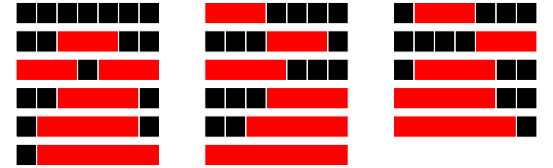
A row measuring seven units in length has red blocks with a minimum length of three units placed on it, such that any two red blocks (which are allowed to be different lengths) are separated by at least one black square. There are exactly seventeen ways of doing this.

-Graphics-

How many ways can a row measuring fifty units in length be filled?

NOTE: Although the example above does not lend itself to the possibility, in general it is permitted to mix block sizes. For example, on a row measuring eight units in length you could use red (3), black (1), and red (4).

```mathematica
SeriesCoefficient[(2+u+v)/(1-u*v)/.{u->x^3/(1-x),v->x/(1-x)},{x,0,50}]
```

16475640049

#### Problem 115 - Counting block combinations II

NOTE: This is a more difficult version of Problem 114.

A row measuring n units in length has red blocks with a minimum length of m units placed on it, such that any two red blocks (which are allowed to be different lengths) are separated by at least one black square.

Let the fill-count function, F(m, n), represent the number of ways that a row can be filled.

For example, F(3, 29) = 673135 and F(3, 30) = 1089155.

That is, for m = 3, it can be seen that n = 30 is the smallest value for which the fill-count function first exceeds one million.

In the same way, for m = 10, it can be verified that F(10, 56) = 880711 and F(10, 57) = 1148904, so n = 57 is the least value for which the fill-count function first exceeds one million.

For m = 50, find the least value of n for which the fill-count function first exceeds one million.

```mathematica
IncreaseWhile[SeriesCoefficient[(2+u+v)/(1-u*v)/.{u->x^50/(1-x),v->x/(1-x)},{x,0,#}]<1*^6&]
```

168

#### Problem 116 - Red, green or blue tiles

A row of five black square tiles is to have a number of its tiles replaced with coloured oblong tiles chosen from red (length two), green (length three), or blue (length four).

If red tiles are chosen there are exactly seven ways this can be done.



If green tiles are chosen there are three ways.



And if blue tiles are chosen there are two ways.



Assuming that colours cannot be mixed there are 7 + 3 + 2 = 12 ways of replacing the black tiles in a row measuring five units in length.

How many different ways can the black tiles in a row measuring fifty units in length be replaced if colours cannot be mixed and at least one coloured tile must be used?

NOTE: This is related to Problem 117.

```mathematica
SeriesCoefficient[1/(1-x-x^2)+1/(1-x-x^3)+1/(1-x-x^4)-3/(1-x),{x,0,50}]
```

20492570929

#### Problem 117 - Red, green, and blue tiles

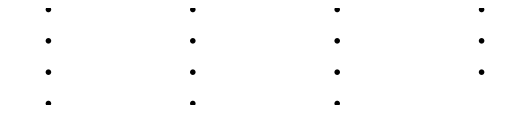
Using a combination of black square tiles and oblong tiles chosen from: red tiles measuring two units, green tiles measuring three units, and blue tiles measuring four units, it is possible to tile a row measuring five units in length in exactly fifteen different ways.

-Graphics-

How many ways can a row measuring fifty units in length be tiled?

NOTE: This is related to Problem 116.

```mathematica
SeriesCoefficient[1/(1-x-x^2-x^3-x^4),{x,0,50}]
```

100808458960497

#### Problem 118 - Pandigital prime sets

Using all of the digits 1 through 9 and concatenating them freely to form decimal integers, different sets can be formed. Interestingly with the set {2,5,47,89,631}, all of the elements belonging to it are prime.

How many distinct sets containing each of the digits one through nine exactly once contain only prime elements?

```mathematica
Union@@(Sort/@Fold[Catenate@Table[Append[sets,#]&/@Select[Permutations[Complement[Range@9,Union@@sets],{#2}],PrimeQ@*FromDigits],{sets,#}]&,{{}},Reverse@#]&/@IntegerPartitions@9)//Length
```

44680

#### Problem 119 - Digit power sum

The number 512 is interesting because it is equal to the sum of its digits raised to some power: 5 + 1 + 2 = 8, and 8^3 = 512. Another example of a number with this property is 614656 = 28^4.

We shall define an to be the nth term of this sequence and insist that a number must contain at least two digits to have a sum.

You are given that a_2 = 512 and a_10 = 614656.

Find a_30.

```mathematica
(Union@@Table[Select[Range[2,9IncreaseWhile[(9#)^n≥10^(#-1)&]]^n,Total@IntegerDigits@#^n==#&],{n,2,30}])[[30]]
```

248155780267521

#### Problem 120 - Square remainders

Let r be the remainder when (a−1)^n + (a+1)^n is divided by a^2.

For example, if a = 7 and n = 3, then r = 42: 6^3 + 8^3 = 728 ≡ 42 mod 49. And as n varies, so too will r, but for a = 7 it turns out that r_max = 42.

For 3 ≤ a ≤ 1000, find ∑ r_max.

```mathematica
Sum[Max@Mod[4Range@a-2,a]a,{a,3,1000}]
```

333082500

#### Problem 121 - Disc game prize fund

A bag contains one red disc and one blue disc. In a game of chance a player takes a disc at random and its colour is noted. After each turn the disc is returned to the bag, an extra red disc is added, and another disc is taken at random.

The player pays £1 to play and wins if they have taken more blue discs than red discs at the end of the game.

If the game is played for four turns, the probability of a player winning is exactly 11/120, and so the maximum prize fund the banker should allocate for winning in this game would be £10 before they would expect to incur a loss. Note that any payout will be a whole number of pounds and also includes the original £1 paid to play the game, so in the example given the player actually wins £9.

Find the maximum prize fund that should be allocated to a single game in which fifteen turns are played.

```mathematica
Floor[1/Total@Take[Fold[{1/#2,1-1/#2}.{#,RotateRight@#}&,SparseArray[1->1,15+1],1+Range@15],Floor[(15+1)/2]]]
```

2269

#### Problem 122 - Efficient exponentiation

The most naive way of computing n^15 requires fourteen multiplications:

n × n × ... × n = n^15

But using a “binary” method you can compute it in six multiplications:

n × n = n^2
n^2 × n^2 = n^4
n^4 × n^4 = n^8
n^8 × n^4 = n^12
n^12 × n^2 = n^14
n^14 × n = n^15

However it is yet possible to compute it in only five multiplications:

n × n = n^2
n^2 × n = n^3
n^3 × n^3 = n^6
n^6 × n^6 = n^12
n^12 × n^3 = n^15

We shall define m(k) to be the minimum number of multiplications to compute n^k; for example m(15) = 5.

For 1 ≤ k ≤ 200, find ∑ m(k).

```mathematica
Length@*First/@Fold[Append[#,MinimalBy[Catenate@Table[Append[#2]/@Select[#[[#2-i]],MemberQ[i]],{i,#2/2}],Length]]&,{{{1}}},Range[2,200]]-1//Total
```

1582

#### Problem 123 - Prime square remainders

Let pn be the nth prime: 2, 3, 5, 7, 11, ..., and let r be the remainder when (p_n−1)^n + (p_n+1)^n is divided by p_n^2.

For example, when n = 3, p_3 = 5, and 4^3 + 6^3 = 280 ≡ 5 mod 25.

The least value of n for which the remainder first exceeds 10^9 is 7037.

Find the least value of n for which the remainder first exceeds 10^10.

```mathematica
IncreaseWhile[Mod[2# Prime@#,Prime@#^2]<1*^10&,1,2]
```

21035

#### Problem 124 - Ordered radicals

The radical of n, rad(n), is the product of the distinct prime factors of n. For example, 504 = 2^3 × 3^2 × 7, so rad(504) = 2 × 3 × 7 = 42.

If we calculate rad(n) for 1 ≤ n ≤ 10, then sort them on rad(n), and sorting on n if the radical values are equal, we get:

Unsorted			Sorted
n	rad(n)		n	rad(n)	k
1	1		1	1	1
2	2		2	2	2
3	3		4	2	3
4	2		8	2	4
5	5		3	3	5
6	6		9	3	6
7	7		5	5	7
8	2		6	6	8
9	3		7	7	9
10	10		10	10	10

Let E(k) be the kth element in the sorted n column; for example, E(4) = 8 and E(6) = 9.

If rad(n) is sorted for 1 ≤ n ≤ 100000, find E(10000).

```mathematica
Last@Ordering[Radical@Range@100000,10000]
```

21417

#### Problem 125 - Palindromic sums

The palindromic number 595 is interesting because it can be written as the sum of consecutive squares: 6^2 + 7^2 + 8^2 + 9^2 + 10^2 + 11^2 + 12^2.

There are exactly eleven palindromes below one-thousand that can be written as consecutive square sums, and the sum of these palindromes is 4164. Note that 1 = 0^2 + 1^2 has not been included as this problem is concerned with the squares of positive integers.

Find the sum of all the numbers less than 10^8 that are both palindromic and can be written as the sum of consecutive squares.

```mathematica
Total@DeleteDuplicates@Catenate@Table[Select[Reap[NestWhileList[#+{#[[2]]^2,1}&,{0,i},If[PalindromeQ@#,Sow@#,#]&@#[[1]]<1*^8&]][[2,1]],i^2<#<1*^8&],{i,1,Sqrt@1*^8}]
```

2906969179

### Problem 126 - 150

#### Problem 126 - Cuboid layers

The minimum number of cubes to cover every visible face on a cuboid measuring 3 x 2 x 1 is twenty-two.

-Graphics-

If we then add a second layer to this solid it would require forty-six cubes to cover every visible face, the third layer would require seventy-eight cubes, and the fourth layer would require one-hundred and eighteen cubes to cover every visible face.

However, the first layer on a cuboid measuring 5 x 1 x 1 also requires twenty-two cubes; similarly the first layer on cuboids measuring 5 x 3 x 1, 7 x 2 x 1, and 11 x 1 x 1 all contain forty-six cubes.

We shall define C(n) to represent the number of cuboids that contain n cubes in one of its layers. So C(22) = 2, C(46) = 4, C(78) = 5, and C(118) = 8.

It turns out that 154 is the least value of n for which C(n) = 10.

Find the least value of n for which C(n) = 1000.

```mathematica
Min@Cases[{n_,1000}:>n]@Tally@Flatten@Table[2(a*b+b*c+c*a)+4(i-1)(a+b+c+i-2),{a,(20000-2)/4},{b,Min[(20000-2a)/(2a+2),a]},{c,Min[(20000-2a*b)/(2a+2b),b]},{i,(3-a-b-c+Sqrt[20000-2+(a-1)^2+(b-1)^2+(c-1)^2])/2}]
```

18522

#### Problem 127 - abc-hits

The radical of n, rad(n), is the product of distinct prime factors of n. For example, 504 = 2^3 × 3^2 × 7, so rad(504) = 2 × 3 × 7 = 42.

We shall define the triplet of positive integers (a, b, c) to be an abc-hit if:

    GCD(a, b) = GCD(a, c) = GCD(b, c) = 1
    a < b
    a + b = c
    rad(abc) < c

For example, (5, 27, 32) is an abc-hit, because:

    GCD(5, 27) = GCD(5, 32) = GCD(27, 32) = 1
    5 < 27
    5 + 27 = 32
    rad(4320) = 30 < 32

It turns out that abc-hits are quite rare and there are only thirty-one abc-hits for c < 1000, with ∑c = 12523.

Find ∑c for c < 120000.

```mathematica
rads=Radical@Range@120000;
radIndex=PositionIndex[rads];
Sum[Length@Select[as,#<c/2&&Times@@rads[[{#,c-#,c}]]<c&]*c,{c,120000},{as,radIndex/@Select[Range[c/rads[[c]]],SquareFreeQ@#&&CoprimeQ[c,#]&]}]
```

18407904

#### Problem 128 - Hexagonal tile differences

A hexagonal tile with number 1 is surrounded by a ring of six hexagonal tiles, starting at “12 o’clock” and numbering the tiles 2 to 7 in an anti-clockwise direction.

New rings are added in the same fashion, with the next rings being numbered 8 to 19, 20 to 37, 38 to 61, and so on. The diagram below shows the first three rings.
-Graphics-
By finding the difference between tile n and each of its six neighbours we shall define PD(n) to be the number of those differences which are prime.

For example, working clockwise around tile 8 the differences are 12, 29, 11, 6, 1, and 13. So PD(8) = 3.

In the same way, the differences around tile 17 are 1, 17, 16, 1, 11, and 10, hence PD(17) = 2.

It can be shown that the maximum value of PD(n) is 3.

If all of the tiles for which PD(n) = 3 are listed in ascending order to form a sequence, the 10th tile would be 271.

Find the 2000th tile in this sequence.

```mathematica
#2[[2000-#3-1]]&@@NestWhile[#/.{k_,_,i_}:>({k+1,#,i+Length@#}&@Cases[{{2+3k+3k^2,Count[{5+6 k,7+6 k,17+12 k},_?PrimeQ]},{7+9k+3k^2,Count[{5+6 k,11+6 k,5+12 k},_?PrimeQ]}},{n_,3}:>n])&,{1,{1,2},2},Last@#<2000&]
```

14516824220

#### Problem 129 - Repunit divisibility

A number consisting entirely of ones is called a repunit. We shall define R(k) to be a repunit of length k; for example, R(6) = 111111.

Given that n is a positive integer and GCD(n, 10) = 1, it can be shown that there always exists a value, k, for which R(k) is divisible by n, and let A(n) be the least such value of k; for example, A(7) = 6 and A(41) = 5.

The least value of n for which A(n) first exceeds ten is 17.

Find the least value of n for which A(n) first exceeds one-million.

```mathematica
Min@Table[i*IncreaseWhile[CoprimeQ[10,#]⇒(CoprimeQ[#,i]⇒#<1*^6/i&@MultiplicativeOrder[10,#])&,Ceiling[1*^6/i]],{i,3^Range[0,Log[3,1*^6]]}]
```

1000023

#### Problem 130 - Composites with prime repunit property

A number consisting entirely of ones is called a repunit. We shall define R(k) to be a repunit of length k; for example, R(6) = 111111.

Given that n is a positive integer and GCD(n, 10) = 1, it can be shown that there always exists a value, k, for which R(k) is divisible by n, and let A(n) be the least such value of k; for example, A(7) = 6 and A(41) = 5.

You are given that for all primes, p > 5, that p − 1 is divisible by A(p). For example, when p = 41, A(41) = 5, and 40 is divisible by 5.

However, there are rare composite values for which this is also true; the first five examples being 91, 259, 451, 481, and 703.

Find the sum of the first twenty-five composite values of n for which
GCD(n, 10) = 1 and n − 1 is divisible by A(n).

```mathematica
Total@NestList[IncreaseWhile[(CompositeQ@#&&CoprimeQ[#,30]⇒!Divisible[#-1,MultiplicativeOrder[10,#]])&,#+1]&,0,25]
```

149253

#### Problem 131 - Prime cube partnership

There are some prime values, p, for which there exists a positive integer, n, such that the expression n^3 + n^2 p is a perfect cube.

For example, when p = 19, 8^2 + 8^2×19 = 12^3.

What is perhaps most surprising is that for each prime with this property the value of n is unique, and there are only four such primes below one-hundred.

How many primes below one million have this remarkable property?

```mathematica
Count[Table[(i+1)^3-i^3,{i,Max[i/.Solve[(i+1)^3-i^3==1*^6,i]]}],_?PrimeQ]
```

173

#### Problem 132 - Large repunit factors

A number consisting entirely of ones is called a repunit. We shall define R(k) to be a repunit of length k.

For example, R(10) = 1111111111 = 11×41×271×9091, and the sum of these prime factors is 9414.

Find the sum of the first forty prime factors of R(10^9).

```mathematica
Total@First@NestWhile[{If[Mod[(PowerMod[10,10^9,#[[2]]]-1)PowerMod[9,-1,#[[2]]],#[[2]]]==0,Append@@#,#[[1]]],NextPrime@#[[2]]}&,{{},5},Length@#[[1]]<40&]
```

843296

#### Problem 133 - Repunit nonfactors

A number consisting entirely of ones is called a repunit. We shall define R(k) to be a repunit of length k; for example, R(6) = 111111.

Let us consider repunits of the form R(10^n).

Although R(10), R(100), or R(1000) are not divisible by 17, R(10000) is divisible by 17. Yet there is no value of n for which R(10^n) will divide by 19. In fact, it is remarkable that 11, 17, 41, and 73 are the only four primes below one-hundred that can be a factor of R(10^n).

Find the sum of all the primes below one-hundred thousand that will never be a factor of R(10^n).

```mathematica
Total@Select[PrimeRange@1*^5,#<7||!SubsetQ[{2,5},First/@FactorInteger@MultiplicativeOrder[10,#]]&]
```

453647705

#### Problem 134 - Prime pair connection

Consider the consecutive primes p_1 = 19 and p_2 = 23. It can be verified that 1219 is the smallest number such that the last digits are formed by p_1 whilst also being divisible by p_2.

In fact, with the exception of p_1 = 3 and p_2 = 5, for every pair of consecutive primes, p_2 > p_1, there exist values of n for which the last digits are formed by p_1 and n is divisible by p_1. Let S be the smallest of these values of n.

Find ∑ S for every pair of consecutive primes with 5 ≤ p_1 ≤ 1000000.

```mathematica
Total[ChineseRemainder[{0,#1},{#2,10^IntegerLength@#1}]&@@@Partition[PrimeRange[5,NextPrime@1000000],2,1]]
```

18613426663617118

#### Problem 135 - Same differences

Given the positive integers, x, y, and z, are consecutive terms of an arithmetic progression, the least value of the positive integer, n, for which the equation, x^2 − y^2 − z^2 = n, has exactly two solutions is n = 27:

34^2 − 27^2 − 20^2 = 12^2 − 9^2 − 6^2 = 27

It turns out that n = 1155 is the least value which has exactly ten solutions.

How many values of n less than one million have exactly ten distinct solutions?

```mathematica
Count[Tally@Catenate@Table[y(3y-4z),{y,1*^6},{z,Max[1,Ceiling[(3y-1*^6/y)/4]],Ceiling[3y/4]-1}],{_,10}]
```

4989

#### Problem 136 - Singleton difference

The positive integers, x, y, and z, are consecutive terms of an arithmetic progression. Given that n is a positive integer, the equation, x^2 − y^2 − z^2 = n, has exactly one solution when n = 20:

13^2 − 10^2 − 7^2 = 20

In fact there are twenty-five values of n below one hundred for which the equation has a unique solution.

How many values of n less than fifty million have exactly one solution?

```mathematica
Length@Select[Mod[#,4]==3&]@PrimeRange@50*^6+PrimePi[50*^6/4]+PrimePi[50*^6/16]
```

2544559

#### Problem 137 - Fibonacci golden nuggets

Consider the infinite polynomial series A_F(x)=x F_1+x^2 F_2+x^3 F_3+..., where F_k is the kth term in the Fibonacci sequence: 1, 1, 2, 3, 5, 8, ... ; that is, F_k=F_(k-1)+F_(k-2), F_1=1 and F_2=1.

For this problem we shall be interested in values of x for which A_F(x) is a positive integer.

Surprisingly A_F(1/2)=(1/2).1+(1/2)^2.1+(1/2)^3.2+(1/2)^4.3+(1/2)^5.5+...
	=1/2+1/3+2/8+3/16+5/32+...
	=2
The corresponding values of x for the first five natural numbers are shown below.

x | A_F(x)
√2−1 | 1
1/2 | 2
(√13−2)/3 | 3
(√89−5)/8 | 4
(√34−3)/5 | 5

We shall call A_F(x) a golden nugget if x is rational, because they become increasingly rarer; for example, the 10th golden nugget is 74049690.

Find the 15th golden nugget.

```mathematica
GeneratingFunction[Fibonacci[n],n,x]
```

-x/(-1+x+x^2)

```mathematica
Solve[-x/(-1+x+x^2)==a,x]
```

{{x→(-1-a+√(1+2 a+5 a^2))/(2 a)},{x→-(1+a+√(1+2 a+5 a^2))/(2 a)}}

```mathematica
DeleteCases[Union@@Table[a/.Solve[{1+2 a+5 a^2==m^2,a>0,m>0},{a,m},Integers]/.C[1]->k//Simplify,{k,0,15}],Undefined][[15]]
```

1120149658760

#### Problem 138 - Special isosceles triangles

Consider the isosceles triangle with base length, b = 16, and legs, L = 17.

-Graphics-

By using the Pythagorean theorem it can be seen that the height of the triangle, h = √(17^2 − 8^2) = 15, which is one less than the base length.

With b = 272 and L = 305, we get h = 273, which is one more than the base length, and this is the second smallest isosceles triangle with the property that h = b ± 1.

Find ∑ L for the twelve smallest isosceles triangles for which h = b ± 1 and b, L are positive integers.

```mathematica
solutions=Table[l/.First@Solve[{(b/2)^2+h^2==l^2,h==b+d,b>0,h>0,l>0},{b,h,l},Integers],{d,{1,-1}}]
```

{ConditionalExpression[1/10 (5 (9-4 √5)^(1+2 C[1])+2 √5 (9-4 √5)^(1+2 C[1])+5 (9+4 √5)^(1+2 C[1])-2 √5 (9+4 √5)^(1+2 C[1])),C[1]∈Integers&&C[1]≥1],ConditionalExpression[1/10 (5 (9-4 √5)^(2 C[1])+2 √5 (9-4 √5)^(2 C[1])+5 (9+4 √5)^(2 C[1])-2 √5 (9+4 √5)^(2 C[1])),C[1]∈Integers&&C[1]≥1]}

```mathematica
Total@Take[Union@@Table[solutions/.C[1]->i//Simplify,{i,12}],12]
```

1118049290473932

#### Problem 139 - Pythagorean tiles

Let (a, b, c) represent the three sides of a right angle triangle with integral length sides. It is possible to place four such triangles together to form a square with length c.

For example, (3, 4, 5) triangles can be placed together to form a 5 by 5 square with a 1 by 1 hole in the middle and it can be seen that the 5 by 5 square can be tiled with twenty-five 1 by 1 squares.

-Graphics-

However, if (5, 12, 13) triangles were used then the hole would measure 7 by 7 and these could not be used to tile the 13 by 13 square.

Given that the perimeter of the right triangle is less than one-hundred million, how many Pythagorean triangles would allow such a tiling to take place?

```mathematica
2m(m+n)/.Solve[m^2-2m*n-n^2==1,n]
```

{-2 m √(-1+2 m^2),2 m √(-1+2 m^2)}

```mathematica
2m(m+n)/.Solve[m^2-2m*n-n^2==-1,n]
```

{-2 m √(1+2 m^2),2 m √(1+2 m^2)}

```mathematica
Sum[Total@Cases[Sqrt[2m^2+{1,-1}],n_Integer/;n>m:>Floor[100*^6/(2m*n)]],{m,Sqrt[100*^6]}]
```

10057761

#### Problem 140 - Modified Fibonacci golden nuggets

Consider the infinite polynomial series A_G(x) = xG_1 + x^2 G_2 + x^3 G_3 + ..., where G_k is the kth term of the second order recurrence relation G_k = G_(k−1) + G_(k−2), G_2 = 1 and G_2 = 4; that is, 1, 4, 5, 9, 14, 23, ... .

For this problem we shall be concerned with values of x for which A_G(x) is a positive integer.

The corresponding values of x for the first five natural numbers are shown below.
x			A_G(x)
(√5−1)/4		1
2/5			2
(√22−2)/6		3
(√137−5)/14	4
1/2			5

We shall call A_G(x) a golden nugget if x is rational, because they become increasingly rarer; for example, the 20th golden nugget is 211345365.

Find the sum of the first thirty golden nuggets.

```mathematica
Solve[x(1+3x)/(1-x-x^2)==n,x]
```

{{x→(-1-n-√(1+14 n+5 n^2))/(2 (3+n))},{x→(-1-n+√(1+14 n+5 n^2))/(2 (3+n))}}

```mathematica
n/.Solve[{1+14n+5n^2==m^2,n>0,m>0},{m,n},Integers]/.ConditionalExpression[expr_,C[1]∈Integers&&C[1]≥cmin_]:>Table[expr/.C[1]->c,{c,cmin,cmin+30-1}]//Simplify//Catenate//TakeSmallest@30//Total
```

5673835352990

#### Problem 141 - Investigating progressive numbers, n, which are also square

A positive integer, n, is divided by d and the quotient and remainder are q and r respectively. In addition d, q, and r are consecutive positive integer terms in a geometric sequence, but not necessarily in that order.

For example, 58 divided by 6 has quotient 9 and remainder 4. It can also be seen that 4, 6, 9 are consecutive terms in a geometric sequence (common ratio 3/2).
We will call such numbers, n, progressive.

Some progressive numbers, such as 9 and 10404 = 1022, happen to also be perfect squares.
The sum of all progressive perfect squares below one hundred thousand is 124657.

Find the sum of all progressive perfect squares below one trillion (10^12).

```mathematica
ParallelSum[If[FractionalPart@Sqrt@N@#==0,#,0]&[b^2 s+a^3 b s^2],{a,1*^12^(1/3)},{b,Select[Range@Min[a-1,(Sqrt[a^6+4.*^12]-a^3)/2],CoprimeQ[a,#]&]},{s,(Sqrt[b^4+4.*^12a^3b ]-b^2)/(2a^3b)}]
```

878454337159

#### Problem 142 - Perfect Square Collection

Find the smallest x + y + z with integers x > y > z > 0 such that x + y, x − y, x + z, x − z, y + z, y − z are all perfect squares.

```mathematica
DeleteCases[(a↦DeleteCases[(b↦Intersection[a,b])/@KeyTake[#,a],{}])/@#,<||>]&@GroupBy[Catenate@Table[{(i^2-j^2)/2,(i^2+j^2)/2},{i,1000},{j,Mod[i,2,1],i-1,2}],First->Last]
```

<|150568→<|420968→{434657}|>|>

```mathematica
150568+420968+434657
```

1006193

#### Problem 144 - Investigating multiple reflections of a laser beam

In laser physics, a “white cell” is a mirror system that acts as a delay line for the laser beam. The beam enters the cell, bounces around on the mirrors, and eventually works its way back out.

The specific white cell we will be considering is an ellipse with the equation 4 x^2 + y^2 = 100

The section corresponding to −0.01 ≤ x ≤ +0.01 at the top is missing, allowing the light to enter and exit through the hole.

-Graphics-

The light beam in this problem starts at the point (0.0,10.1) just outside the white cell, and the beam first impacts the mirror at (1.4,-9.6).

Each time the laser beam hits the surface of the ellipse, it follows the usual law of reflection “angle of incidence equals angle of reflection.” That is, both the incident and reflected beams make the same angle with the normal line at the point of incidence.

In the figure on the left, the red line shows the first two points of contact between the laser beam and the wall of the white cell; the blue line shows the line tangent to the ellipse at the point of incidence of the first bounce.

The slope m of the tangent line at any point (x,y) of the given ellipse is: m = −4x/y

The normal line is perpendicular to this tangent line at the point of incidence.

The animation on the right shows the first 10 reflections of the beam.

How many times does the beam hit the internal surface of the white cell before exiting?

```mathematica
First@NestWhile[{#1+1,{x,y},#2}/.First@NSolve[{{x,y}∈TransformedRegion[InfiniteLine@{##2},ReflectionTransform[Reverse[{-4,1}#2],#2]],{x,y}∈Circle[{0,0},{5,10}],{x,y}≠#2},{x,y}]&@@#&,{0,{1.4,-9.6},{0,10.1}},Abs@#[[2,1]]>0.01||#[[2,2]]<0&]
```

354

#### Problem 145 - How many reversible numbers are there below one-billion?

Some positive integers n have the property that the sum [ n + reverse(n) ] consists entirely of odd (decimal) digits. For instance, 36 + 63 = 99 and 409 + 904 = 1313. We will call such numbers reversible; so 36, 63, 409, and 904 are reversible. Leading zeroes are not allowed in either n or reverse(n).

There are 120 reversible numbers below one-thousand.

How many reversible numbers are there below one-billion (10^9)?

```mathematica
Sum[1,{i,1,9},{j,Mod[i,2]+1,9-i,2}]
```

20

```mathematica
Sum[1,{i,0,9},{j,11-i,9,2}]
```

20

```mathematica
Sum[1,{i,0,9},{j,Mod[i,2],9-i,2}]
```

25

```mathematica
Sum[1,{i,0,9},{j,Mod[i+1,2],9-i,2}]
```

30

```mathematica
Sum[20*30^(i/2-1),{i,2,#,2}]+Sum[5*20*(20*25)^((i-3)/4),{i,3,#,4}]&@9
```

608720

#### Problem 146 - Investigating a Prime Pattern

The smallest positive integer n for which the numbers n^2+1, n^2+3, n^2+7, n^2+9, n^2+13, and n^2+27 are consecutive primes is 10. The sum of all such integers n below one-million is 1242490.

What is the sum of all such integers n below 150 million?

```mathematica
Select[Last@Fold[{x,p}↦{x[[1]]p,Select[Total/@Tuples@{x[[2]],x[[1]]Range[0,p-1]},FreeQ[Mod[p-{1,3,7,9,13,27},p],Mod[#^2,p]]&]},{1,{0}},Prime@Range@9],#<150*^6&&AllTrue[#^2+{1,3,7,9,13,27},PrimeQ]&&NestList[NextPrime,#^2,6]==#^2+{0,1,3,7,9,13,27}&]//Total
```

676333270

#### Problem 147 - Rectangles in cross-hatched grids

In a 3x2 cross-hatched grid, a total of 37 different rectangles could be situated within that grid as indicated in the sketch.

-Graphics-

There are 5 grids smaller than 3x2, vertical and horizontal dimensions being important, i.e. 1x1, 2x1, 3x1, 1x2 and 2x2. If each of them is cross-hatched, the following number of different rectangles could be situated within those smaller grids:

1x1: 1
2x1: 4
3x1: 8
1x2: 4
2x2: 18

Adding those to the 37 of the 3x2 grid, a total of 72 different rectangles could be situated within 3x2 and smaller grids.

How many different rectangles could be situated within 47x43 and smaller grids?

```mathematica
foo[a_,b_,c_]:=foo[a,b,c]=Sum[Min[b,c-i],{i,Min[a,c]}]
```

```mathematica
Sum[m(m+1)n(n+1)/4+Sum[foo[j,2n-j,2m-i],{i,1,2m-2,2},{j,1,2n,2}]+Sum[foo[j,2n-j,2m-i],{i,0,2m-2,2},{j,2,2n-2,2}],{m,47},{n,43}]
```

846910284

#### Problem 148 - Exploring Pascal’s triangle

We can easily verify that none of the entries in the first seven rows of Pascal’s triangle are divisible by 7:
  	  	  	  	  	  	 1
  	  	  	  	  	 1 	  	 1
  	  	  	  	 1 	  	 2 	  	 1
  	  	  	 1 	  	 3 	  	 3 	  	 1
  	  	 1 	  	 4 	  	 6 	  	 4 	  	 1
  	 1 	  	 5 	  	10 	  	10 	  	 5 	  	 1
1 	  	 6 	  	15 	  	20 	  	15 	  	 6 	  	 1

However, if we check the first one hundred rows, we will find that only 2361 of the 5050 entries are not divisible by 7.

Find the number of entries which are not divisible by 7 in the first one billion (10^9) rows of Pascal’s triangle.

```mathematica
28^(#-Range@#)&@Length@#.(Most@FoldList[Times,1,#+1]*#(#+1)/2)&@IntegerDigits[1*^9,7]
```

2129970655314432

#### Problem 149 - Searching for a maximum-sum subsequence

Looking at the table below, it is easy to verify that the maximum possible sum of adjacent numbers in any direction (horizontal, vertical, diagonal or anti-diagonal) is 16 (= 8 + 7 + 1).

-2 | 5 | 3 | 2
9 | -6 | 5 | 1
3 | 2 | 7 | 3
-1 | 8 | -4 | 8

Now, let us repeat the search, but on a much larger scale:

First, generate four million pseudo-random numbers using a specific form of what is known as a “Lagged Fibonacci Generator”:

For 1 ≤ k ≤ 55, s_k=[100003-200003k+300007 k^3](modulo 1000000)- 500000.
For 56 ≤ k ≤ 4000000, s_k=[s_(k-24)+s_(k-55)+1000000](modulo 1000000)- 500000.

Thus, s_10 =-393027 and s_100 =86613.

The terms of s are then arranged in a 2000×2000 table, using the first 2000 numbers to fill the first row (sequentially), the next 2000 numbers to fill the second row, and so on.

Finally, find the greatest sum of (any number of) adjacent entries in any direction (horizontal, vertical, diagonal or anti-diagonal).

```mathematica
s[k_]/;k≤55:=s[k]=Mod[100003-200003k+300007k^3,1000000]-500000;
s[k_]:=s[k]=Mod[s[k-24]+s[k-55]+1000000,1000000]-500000;
Max[
Max[#-Most@FoldList[Min,0,#]]&@*Accumulate/@Join[#,Transpose@#,Table[Diagonal[#,i],{i,-2000,2000}],Table[Diagonal[Reverse@#,i],{i,-2000,2000}]]]&@Array[s[2000(#1-1)+#2]&,{2000,2000}]
```

52852124

#### Problem 150 - Searching a triangular array for a sub-triangle having minimum-sum

In a triangular array of positive and negative integers, we wish to find a sub-triangle such that the sum of the numbers it contains is the smallest possible.

In the example below, it can be easily verified that the marked triangle satisfies this condition having a sum of −42.
-Graphics-
We wish to make such a triangular array with one thousand rows, so we generate 500500 pseudo-random numbers sk in the range ±2^19, using a type of random number generator (known as a Linear Congruential Generator) as follows:

t := 0
for k = 1 up to k = 500500:
    t := (615949*t + 797807) modulo 220^20
    s_k := t−2^19

Thus: s_1 = 273519, s_2 = −153582, s_3 = 450905 etc

Our triangular array is then formed using the pseudo-random numbers thus:
s_1
s_2  s_3
s_4  s_5  s_6 
s_7  s_8  s_9  s_10
...

Sub-triangles can start at any element of the array and extend down as far as we like (taking-in the two elements directly below it from the next row, the three elements directly below from the row after that, and so on).
The “sum of a sub-triangle” is defined as the sum of all the elements it contains.
Find the smallest possible sub-triangle sum.

```mathematica
Min@Table[Min@Accumulate[#[[i;;,j-i]]-#[[i;;,j]]],{i,Length@#},{j,0,i-1}]&[0@@@Accumulate/@Block[{t=0},Table[t=Mod[615949t+797807,2^20];t-2^19,{i,1000},{j,i}]]]
```

-271248680

### Problem 151 - 175

#### Problem 151 - Paper sheets of standard sizes: an expected-value problem

A printing shop runs 16 batches (jobs) every week and each batch requires a sheet of special colour-proofing paper of size A5.

Every Monday morning, the foreman opens a new envelope, containing a large sheet of the special paper with size A1.

He proceeds to cut it in half, thus getting two sheets of size A2. Then he cuts one of them in half to get two sheets of size A3 and so on until he obtains the A5-size sheet needed for the first batch of the week.

All the unused sheets are placed back in the envelope.

-Graphics-

At the beginning of each subsequent batch, he takes from the envelope one sheet of paper at random. If it is of size A5, he uses it. If it is larger, he repeats the ‘cut-in-half’ procedure until he has what he needs and any remaining sheets are always placed back in the envelope.

Excluding the first and last batch of the week, find the expected number of times (during each week) that the foreman finds a single sheet of paper in the envelope.

Give your answer rounded to six decimal places using the format x.xxxxxx .

```mathematica
expectation[{0,0,0,1}]=0;
expectation[a_]/;Min@a<0=0;
expectation[a_]:=Boole[Total@a==1]+a.(expectation[a+#]&/@{{-1,1,1,1},{0,-1,1,1},{0,0,-1,1},{0,0,0,-1}})/Total@a;N[expectation[{1,1,1,1}],6]
```

0.464399

#### Problem 155 - Counting Capacitor Circuits

An electric circuit uses exclusively identical capacitors of the same value C.
The capacitors can be connected in series or in parallel to form sub-units, which can then be connected in series or in parallel with other capacitors or other sub-units to form larger sub-units, and so on up to a final circuit.

Using this simple procedure and up to n identical capacitors, we can make circuits having a range of different total capacitances. For example, using up to n=3 capacitors of 60 F each, we can obtain the following 7 distinct total capacitance values:

-Graphics-

If we denote by D(n) the number of distinct total capacitance values we can obtain when using up to n equal-valued capacitors and the simple procedure described above, we have: D(1)=1, D(2)=3, D(3)=7 ...

Find D(18).

Reminder : When connecting capacitors C_1, C_2 etc in parallel, the total capacitance is C_T = C_1 + C_2 +...,
whereas when connecting them in series, the overall capacitance is given by: -Graphics-

```mathematica
c[1]={1};
c[n_]:=c[n]=DeleteDuplicates@Flatten@Table[Outer[{#1,#2/#1}&[+##,1##]&,c[i],c[n-i]],{i,n/2}];
```

```mathematica
Length@DeleteDuplicates@Catenate@Table[c[n],{n,18}]
```

3857447

#### Problem 157 - Solving the diophantine equation 1/a+1/b=p/10^n

Consider the diophantine equation 1/a+1/b=p/10^n with a, b, p, n positive integers and a ≤ b.
For n=1 this equation has 20 solutions that are listed below:
1/1+1/1=20/10 	1/1+1/2=15/10 	1/1+1/5=12/10 	1/1+1/10=11/10 	1/2+1/2=10/10
1/2+1/5=7/10 		1/2+1/10=6/10 	1/3+1/6=5/10 		1/3+1/15=4/10 	1/4+1/4=5/10
1/4+1/20=3/10 	1/5+1/5=4/10 		1/5+1/10=3/10 	1/6+1/30=2/10 	1/10+1/10=2/10
1/11+1/110=1/10 	1/12+1/60=1/10 	1/14+1/35=1/10 	1/15+1/30=1/10 	1/20+1/20=1/10

How many solutions has this equation for 1 ≤ n ≤ 9?

```mathematica
Sum[DivisorSigma[0,GCD[10^n+d,10^n+10^(2n)/d]],{n,1,9},{d,TakeWhile[Divisors[10^(2n)],#≤10^n&]}]
```

53490

#### Problem 158 - Exploring strings for which only one character comes lexicographically after its neighbour to the left

Taking three different letters from the 26 letters of the alphabet, character strings of length three can be formed.
Examples are ‘abc’, ‘hat’ and ‘zyx’.
When we study these three examples we see that for ‘abc’ two characters come lexicographically after its neighbour to the left.
For ‘hat’ there is exactly one character that comes lexicographically after its neighbour to the left. For ‘zyx’ there are zero characters that come lexicographically after its neighbour to the left.
In all there are 10400 strings of length 3 for which exactly one character comes lexicographically after its neighbour to the left.

We now consider strings of n ≤ 26 different characters from the alphabet.
For every n, p(n) is the number of strings of length n for which exactly one character comes lexicographically after its neighbour to the left.

What is the maximum value of p(n)?

```mathematica
Max@Table[(2^n-n-1)Binomial[26,n],{n,26}]
```

409511334375

#### Problem 159 - Digital root sums of factorisations

A composite number can be factored many different ways. For instance, not including multiplication by one, 24 can be factored in 7 distinct ways:
24 = 2x2x2x3
24 = 2x3x4
24 = 2x2x6
24 = 4x6
24 = 3x8
24 = 2x12
24 = 24

Recall that the digital root of a number, in base 10, is found by adding together the digits of that number, and repeating that process until a number is arrived at that is less than 10. Thus the digital root of 467 is 8.

We shall call a Digital Root Sum (DRS) the sum of the digital roots of the individual factors of our number.
The chart below demonstrates all of the DRS values for 24.

Factorisation | Digital Root Sum
2×2×2×3 | 9
2×3×4 | 9
2×2×6 | 10
4×6 | 10
3×8 | 11
2×12 | 5
24 | 6

The maximum Digital Root Sum of 24 is 11.
The function mdrs(n) gives the maximum Digital Root Sum of n. So mdrs(24)=11.
Find ∑mdrs(n) for 1 < n < 1,000,000.

```mathematica
mdrs[1]=1;
mdrs[n_]:=mdrs[n]=Max[FixedPoint[Total@*IntegerDigits,n],#+Reverse@#&[mdrs/@#[[2;;-2]]&@Divisors@n]]
```

```mathematica
Sum[mdrs[n],{n,2,999999}]
```

14489159

#### Problem 160 - Factorial trailing digits

For any N, let f(N) be the last five digits before the trailing zeroes in N!.
For example,

9! = 362880 so f(9)=36288
10! = 3628800 so f(10)=36288
20! = 2432902008176640000 so f(20)=17664

Find f(1,000,000,000,000)

```mathematica
Mod[Product[If[Divisible[i,5],1,i],{i,1,Mod[Floor[1*^12/#],1*^5],2}],1*^5]&@1
```

1

```mathematica
Mod[PowerMod[2,Subtract@@Sum[({1,-1,-1,1}.Floor[1*^12/(2^i*5^j)/{1,2,5,10}]){i,j},{i,0,Log2[1*^12]},{j,0,Log[5,1*^12/2^i]}],1*^5]*Product[Mod[Product[If[Divisible[i,5],1,i],{i,1,Mod[Floor[1*^12/(2^i*5^j)],1*^5],2}],1*^5],{i,0,Log2[1*^12]},{j,0,Log[5,1*^12/2^i]}],1*^5]
```

16576

#### Problem 162 - Hexadecimal numbers

In the hexadecimal number system numbers are represented using 16 different digits:

0,1,2,3,4,5,6,7,8,9,A,B,C,D,E,F

The hexadecimal number AF when written in the decimal number system equals 10x16+15=175.

In the 3-digit hexadecimal numbers 10A, 1A0, A10, and A01 the digits 0,1 and A are all present.
Like numbers written in base ten we write hexadecimal numbers without leading zeroes.

How many hexadecimal numbers containing at most sixteen hexadecimal digits exist with all of the digits 0,1, and A present at least once?
Give your answer as a hexadecimal number.

(A,B,C,D,E and F in upper case, without any leading or trailing code that marks the number as hexadecimal and without leading zeroes , e.g. 1A3F and not: 1a3f and not 0x1a3f and not $1A3F and not #1A3F and not 0000001A3F)

```mathematica
IntegerString[Sum[15*16^(k-1)-15^k-2*14*15^(k-1)+2*14^k+13*14^(k-1)-13^k,{k,1,16}],16]//ToUpperCase
```

3D58725572C62302

#### Problem 164 - Numbers for which no three consecutive digits have a sum greater than a given value

How many 20 digit numbers n (without any leading zero) exist such that no three consecutive digits of n have a sum greater than 9?

```mathematica
Nest[Expand[#/.e[i_,j_]:>Sum[e[j,k],{k,0,9-i-j}]]&,Sum[e[0,i],{i,9}],19]/._e->1
```

378158756814587

#### Problem 166 - Criss Cross

A 4x4 grid is filled with digits d, 0 ≤ d ≤ 9.

It can be seen that in the grid

6 3 3 0
5 0 4 3
0 7 1 4
1 2 4 5

the sum of each row and each column has the value 12. Moreover the sum of each diagonal is also 12.

In how many ways can you fill a 4x4 grid with the digits d, 0 ≤ d ≤ 9 so that each row, each column, and both diagonals have the same sum?

```mathematica
sol=First@Solve[Equal@@Total[Join[#,Transpose@#,Diagonal/@{#,Reverse@#}],{2}],Catenate@#]&@Array[Symbol["a"<>ToString/@{##}]&,{4,4}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{a24→a11+a12+a13+a14-a21-a22-a23,a32→a11-a14+a21-a23+a31,a33→a12+a13+2 a14-a21-a22-a31,a34→a22+a23-a31,a41→a12+a13+a14-a21-a31,a42→a13+2 a14-a21-a22+a23-a31,a43→a11-a13-a14+a21+a22-a23+a31,a44→-a14+a21+a31}

```mathematica
a31range=Max[0,Min[9,#[[2]]]-Max[0,#[[1]]]+1]&@Transpose@Cases[Reduce[0≤#≤9,a31]&/@sol[[2;;,2]],Inequality[min_,LessEqual,a31,LessEqual,max_]:>{min,max},{2}];
```

```mathematica
ParallelSum[With[{s=a11+a12+a13+a14},Sum[a31range,{a21,Max[0,s-27],Min[9,s]},{a22,Max[0,s-a21-18],Min[9,s-a21]},{a23,Max[0,s-a21-a22-9],Min[9,s-a21-a22]}]],{a11,0,9},{a12,0,9},{a13,0,9},{a14,0,9}]
```

7130034

#### Problem 168 - Number Rotations

Consider the number 142857. We can right-rotate this number by moving the last digit (7) to the front of it, giving us 714285.
It can be verified that 714285=5×142857.
This demonstrates an unusual property of 142857: it is a divisor of its right-rotation.

Find the last 5 digits of the sum of all integers n, 10 < n < 10^100, that have this property.

```mathematica
Mod[Sum[Sum[FromDigits@Catenate@ConstantArray[#,n],{n,Ceiling[2/Length@#],100/Length@#}]&@If[{k,i}=={1,9},{9},RealDigits[i/(10k-1)][[1,1]]],{k,1,9},{i,k,9}],1*^5]
```

59206

#### Problem 169 - Exploring the number of different ways a number can be expressed as a sum of powers of 2

Define f(0)=1 and f(n) to be the number of different ways n can be expressed as a sum of integer powers of 2 using each power no more than twice.

For example, f(10)=5 since there are five different ways to express 10:

1 + 1 + 8
1 + 1 + 4 + 4
1 + 1 + 2 + 2 + 4
2 + 4 + 4
2 + 8

What is f(10^25)?

```mathematica
f[0]=1;
f[n_?OddQ]:=f[n]=f[(n-1)/2];
f[n_?EvenQ]:=f[n]=f[n/2]+f[n/2-1];
f[10^25]
```

178653872807

#### Problem 171 - Finding numbers for which the sum of the squares of the digits is a square

For a positive integer n, let f(n) be the sum of the squares of the digits (in base 10) of n, e.g.

f(3) = 3^2= 9,
f(25) = 2^2 + 5^2 = 4 + 25 = 29,
f(442) = 4^2 + 4^2 + 2^2 = 16 + 16 + 4 = 36

Find the last nine digits of the sum of all n, 0 < n < 10^20, such that f(n) is a perfect square.

```mathematica
Mod[Total[NestList[{Sum[RotateRight[10#[[1]]+i#[[2]],i^2],{i,0,9}],Sum[RotateRight[#[[2]],i^2],{i,0,9}]}&,{SparseArray[Table[i^2->i,{i,9}],20*9^2],SparseArray[Table[i^2->1,{i,9}],20*9^2]},19][[;;,1,Range[Sqrt[20*9^2]]^2]],2],1*^9]
```

142989277

#### Problem 172 - Investigating numbers with few repeated digits

How many 18-digit numbers n (without leading zeros) are there such that no digit occurs more than three times in n?

```mathematica
18!SeriesCoefficient[(1+x+x^2/2+x^3/6)^10,{x,0,18}]-17!SeriesCoefficient[(1+x+x^2/2)(1+x+x^2/2+x^3/6)^9,{x,0,17}]
```

227485267000992000

#### Problem 173 - Using up to one million tiles how many different “hollow” square laminae can be formed?

We shall define a square lamina to be a square outline with a square “hole” so that the shape possesses vertical and horizontal symmetry. For example, using exactly thirty-two square tiles we can form two different square laminae:

-Graphics-

With one-hundred tiles, and not necessarily using all of the tiles at one time, it is possible to form forty-one different square laminae.

Using up to one million tiles how many different square laminae can be formed?

```mathematica
Total@Floor[DivisorSigma[0,Range[1*^6/4]]/2]
```

1572729

#### Problem 174 - Counting the number of “hollow” square laminae that can form one, two, three, ... distinct arrangements

We shall define a square lamina to be a square outline with a square “hole” so that the shape possesses vertical and horizontal symmetry.

Given eight tiles it is possible to form a lamina in only one way: 3x3 square with a 1x1 hole in the middle. However, using thirty-two tiles it is possible to form two distinct laminae.

-Graphics-

If t represents the number of tiles used, we shall say that t = 8 is type L(1) and t = 32 is type L(2).

Let N(n) be the number of t ≤ 1000000 such that t is type L(n); for example, N(15) = 832.

What is ∑ N(n) for 1 ≤ n ≤ 10?

```mathematica
Count[Floor[DivisorSigma[0,Range[1*^6/4]]/2],n_/;1≤n≤10]
```

209566

### Problem 176 - 200

#### Problem 178 - Step Numbers

Consider the number 45656.
It can be seen that each pair of consecutive digits of 45656 has a difference of one.
A number for which every pair of consecutive digits has a difference of one is called a step number.
A pandigital number contains every decimal digit from 0 to 9 at least once.
How many pandigital step numbers less than 10^40 are there?

```mathematica
f[1,1,1]=1;
f[1,_,_]=0;
f[i_,j_,_]/;i>j=0;
f[i_,j_,1]:=f[i,j,1]=f[i-1,j-1,1]+f[i,j-1,2];
f[i_,j_,i_]:=f[i,j,i]=f[i-1,j-1,i-1]+f[i,j-1,i-1];
f[i_,j_,k_]:=f[i,j,k]=f[i,j-1,k-1]+f[i,j-1,k+1];
```

```mathematica
Sum[f[10,j,k],{j,40},{k,9}]
```

126461847755

#### Problem 179 - Consecutive positive divisors

Find the number of integers 1 < n < 10^7, for which n and n + 1 have the same number of positive divisors. For example, 14 has the positive divisors 1, 2, 7, 14 while 15 has 1, 3, 5, 15

```mathematica
d=0;
Sum[Boole[d==(d=DivisorSigma[0,i])],{i,1*^7}]
```

986262

#### Problem 182 - RSA encryption

The RSA encryption is based on the following procedure:

Generate two distinct primes p and q.
Compute n=pq and φ=(p-1)(q-1).
Find an integer e, 1<e<φ, such that gcd(e,φ)=1.

A message in this system is a number in the interval [0,n-1].
A text to be encrypted is then somehow converted to messages (numbers in the interval [0,n-1]).
To encrypt the text, for each message, m, c=m^e mod n is calculated.

To decrypt the text, the following procedure is needed: calculate d such that ed=1 mod φ, then for each encrypted message, c, calculate m=c^d mod n.

There exist values of e and m such that m^e mod n=m.
We call messages m for which m^e mod n=m unconcealed messages.

An issue when choosing e is that there should not be too many unconcealed messages.
For instance, let p=19 and q=37.
Then n=19*37=703 and φ=18*36=648.
If we choose e=181, then, although gcd(181,648)=1 it turns out that all possible messages
m (0≤m≤n-1) are unconcealed when calculating m^e mod n.
For any valid choice of e there exist some unconcealed messages.
It’s important that the number of unconcealed messages is at a minimum.

Choose p=1009 and q=3643.
Find the sum of all values of e, 1<e<φ(1009,3643) and gcd(e,φ)=1, so that the number of unconcealed messages for this value of e is at a minimum.

```mathematica
φ=(1009-1)(3643-1)
```

3671136

```mathematica
Total@Select[Range@φ,CoprimeQ[#,φ]&&GCD[#-1,φ]==2&]
```

399788195976

#### Problem 183 - Maximum product of parts

Let N be a positive integer and let N be split into k equal parts, r = N/k, so that N = r + r + ... + r.
Let P be the product of these parts, P = r × r × ... × r = r^k.

For example, if 11 is split into five equal parts, 11 = 2.2 + 2.2 + 2.2 + 2.2 + 2.2, then P = 2.2^5 = 51.53632.

Let M(N) = P_max for a given value of N.

It turns out that the maximum for N = 11 is found by splitting eleven into four equal parts which leads to P_max = (11/4)^4; that is, M(11) = 14641/256 = 57.19140625, which is a terminating decimal.

However, for N = 8 the maximum is achieved by splitting it into three equal parts, so M(8) = 512/27, which is a non-terminating decimal.

Let D(N) = N if M(N) is a non-terminating decimal and D(N) = -N if M(N) is a terminating decimal.

For example, ΣD(N) for 5 ≤ N ≤ 100 is 2438.

Find ΣD(N) for 5 ≤ N ≤ 10000.

```mathematica
Sum[If[SubsetQ[{1,2,5},First/@FactorInteger@Denominator@Max@Table[(n/k)^k,{k,{Floor[n/E],Ceiling[n/E]}}]],-n,n],{n,5,10000}]
```

48861552

#### Problem 185 - Number Mind

The game Number Mind is a variant of the well known game Master Mind.

Instead of coloured pegs, you have to guess a secret sequence of digits. After each guess you’re only told in how many places you’ve guessed the correct digit. So, if the sequence was 1234 and you guessed 2036, you’d be told that you have one correct digit; however, you would NOT be told that you also have another digit in the wrong place.

For instance, given the following guesses for a 5-digit secret sequence,

90342 ;2 correct
70794 ;0 correct
39458 ;2 correct
34109 ;1 correct
51545 ;2 correct
12531 ;1 correct

The correct sequence 39542 is unique.

Based on the following guesses,

5616185650518293 ;2 correct
3847439647293047 ;1 correct
5855462940810587 ;3 correct
9742855507068353 ;3 correct
4296849643607543 ;3 correct
3174248439465858 ;1 correct
4513559094146117 ;2 correct
7890971548908067 ;3 correct
8157356344118483 ;1 correct
2615250744386899 ;2 correct
8690095851526254 ;3 correct
6375711915077050 ;1 correct
6913859173121360 ;1 correct
6442889055042768 ;2 correct
2321386104303845 ;0 correct
2326509471271448 ;2 correct
5251583379644322 ;2 correct
1748270476758276 ;3 correct
4895722652190306 ;1 correct
3041631117224635 ;3 correct
1841236454324589 ;3 correct
2659862637316867 ;2 correct

Find the unique 16-digit secret sequence.

```mathematica
guesses=StringCases["5616185650518293 ;2 correct
3847439647293047 ;1 correct
5855462940810587 ;3 correct
9742855507068353 ;3 correct
4296849643607543 ;3 correct
3174248439465858 ;1 correct
4513559094146117 ;2 correct
7890971548908067 ;3 correct
8157356344118483 ;1 correct
2615250744386899 ;2 correct
8690095851526254 ;3 correct
6375711915077050 ;1 correct
6913859173121360 ;1 correct
6442889055042768 ;2 correct
2321386104303845 ;0 correct
2326509471271448 ;2 correct
5251583379644322 ;2 correct
1748270476758276 ;3 correct
4895722652190306 ;1 correct
3041631117224635 ;3 correct
1841236454324589 ;3 correct
2659862637316867 ;2 correct",n:NumberString~~" ;"~~d:DigitCharacter~~" correct":>{IntegerDigits@FromDigits@n,FromDigits@d}];
```

```mathematica
Length@guesses[[1,1]]
```

16

```mathematica
FromDigits@Flatten[Position[1]/@Partition[LinearProgramming[ConstantArray[1,160],##,ConstantArray[{0,1},160],Integers],10]-1]&@@Transpose@Normal@Join[{Join@@(SparseArray[#+1->1,10]&/@#[[1]]),{#[[2]],0}}&/@guesses,Table[{SparseArray[j_/;10(i-1)<j≤10i->1,160],{1,0}},{i,16}]]
```

LinearProgramming::lpip: Warning: integer linear programming will use a machine-precision approximation of the inputs.

4640261571849533

#### Problem 186 - Connectedness of a network

Here are the records from a busy telephone system with one million users:
RecNr	Caller		Called
1	200007	100053
2	600183	500439
3	600863	701497
...	...		...

The telephone number of the caller and the called number in record n are Caller(n) = S_(2n-1) and Called(n) = S_(2n) where S_(1,2,3,...) come from the “Lagged Fibonacci Generator”:

For 1 ≤ k ≤ 55, S_k = [100003 - 200003k + 300007 k^3] (modulo 1000000)
For 56 ≤ k, S_k = [S_(k-24) + S_(k-55)] (modulo 1000000)

If Caller(n) = Called(n) then the user is assumed to have misdialled and the call fails; otherwise the call is successful.

From the start of the records, we say that any pair of users X and Y are friends if X calls Y or vice-versa. Similarly, X is a friend of a friend of Z if X is a friend of Y and Y is a friend of Z; and so on for longer chains.

The Prime Minister’s phone number is 524287. After how many successful calls, not counting misdials, will 99% of the users (including the PM) be a friend, or a friend of a friend etc., of the Prime Minister?

```mathematica
(*Slow!*)
```

```mathematica
s[k_]/;1≤k≤55:=s[k]=Mod[100003-200003k+300007k^3,1000000];
s[k_]:=s[k]=Mod[s[k-24]+s[k-55],1000000];
```

```mathematica
cc[g_]:=Total[Length/@ConnectedComponents[Graph[UndirectedEdge@@@g],{524287}]]
```

```mathematica
MemberQ[Array[s,5000000],524287]
```

True

```mathematica
gs=Partition[Array[s,5000000],2];
cc[gs]
```

993006

```mathematica
With[{new={#,cc[gs[[;;#]]]}&@Ceiling[(#1[[1]]+#2[[1]])/2]},If[new[[2]]<990000,#0[new,#2],If[#1[[1]]+1<new[[1]],#0[#1,new],Length@DeleteCases[gs[[;;new[[1]]]],{s_,s_}]]]]&[{0,0},{2500000,993006}]
```

2325629

#### Problem 187 - Semiprimes

A composite is a number containing at least two prime factors. For example, 15 = 3 × 5; 9 = 3 × 3; 12 = 2 × 2 × 3.

There are ten composites below thirty containing precisely two, not necessarily distinct, prime factors: 4, 6, 9, 10, 14, 15, 21, 22, 25, 26.

How many composite integers, n < 10^8, have precisely two, not necessarily distinct, prime factors?

```mathematica
Sum[# UnitStep@#&[PrimePi[1*^8/Prime@i]-i+1],{i,PrimePi[1*^8/2]}]
```

17427258

#### Problem 188 - The hyperexponentiation of a number

The hyperexponentiation or tetration of a number a by a positive integer b, denoted by a↑↑b or ba, is recursively defined by:

a↑↑1 = a,
a↑↑(k+1) = a^(a↑↑k).

Thus we have e.g. 3↑↑2 = 3^3 = 27, hence 3↑↑3 = 3^27 = 7625597484987 and 3↑↑4 is roughly 10^(3.6383346400240996*10^12).

Find the last 8 digits of 1777↑↑1855.

```mathematica
a_↑1:=a;
a_↑k_:=PowerMod[a,a↑(k-1),1*^8];
```

```mathematica
Block[{$RecursionLimit=Infinity},1777↑1855]
```

95962097

#### Problem 190 - Maximising a weighted product

Let S_m = (x_1, x_2, ... , x_m) be the m-tuple of positive real numbers with x_1 + x_2 + ... + x_m = m for which P_m = x_1 * x_2^2 * ... * x_m^m is maximised.

For example, it can be verified that [P_10] = 4112 ([ ] is the integer part function).

Find Σ[P_m] for 2 ≤ m ≤ 15.

```mathematica
Sum[Floor[Product[i^i,{i,m}](2/(m+1))^(m(m+1)/2)],{m,2,15}]
```

371048281

#### Problem 191 - Prize Strings

A particular school offers cash rewards to children with good attendance and punctuality. If they are absent for three consecutive days or late on more than one occasion then they forfeit their prize.

During an n-day period a trinary string is formed for each child consisting of L’s (late), O’s (on time), and A’s (absent).

Although there are eighty-one trinary strings for a 4-day period that can be formed, exactly forty-three strings would lead to a prize:

OOOO OOOA OOOL OOAO OOAA OOAL OOLO OOLA OAOO OAOA
OAOL OAAO OAAL OALO OALA OLOO OLOA OLAO OLAA AOOO
AOOA AOOL AOAO AOAA AOAL AOLO AOLA AAOO AAOA AAOL
AALO AALA ALOO ALOA ALAO ALAA LOOO LOOA LOAO LOAA
LAOO LAOA LAAO

How many “prize” strings exist over a 30-day period?

```mathematica
SeriesCoefficient[#-1+x#^2&[(1+x+x^2)/(1-x-x^2-x^3)],{x,0,30}]
```

1918080160

#### Problem 193 - Squarefree Numbers

A positive integer n is called squarefree, if no square of a prime divides n, thus 1, 2, 3, 5, 6, 7, 10, 11 are squarefree, but not 4, 8, 9, 12.

How many squarefree numbers are there below 2^50?

```mathematica
Block[{$RecursionLimit=Infinity,q=PrimePi[Sqrt[2.^50/Select[Range@3*^6,MoebiusMu[#]^2==1&]]],f},f[m_,0]:=m;f[m_,n_]:=f[m,n]=f[m,n-1]-f[Floor[m/Prime@n^2],n-1];f[2^50,Last@q]-Total@q+Length@q*Last@q]
```

684465067343069

#### Problem 197 - Investigating the behaviour of a recursively defined sequence

Given is the function f(x) = ⌊2^(30.403243784-x^2)⌋ × 10^-9 ( ⌊ ⌋ is the floor-function),
the sequence un is defined by u_0 = -1 and u_(n+1) = f(u_n).

Find u_n + u_(n+1) for n = 10^12.
Give your answer with 9 digits after the decimal point.

```mathematica
f[x_]:=⌊2^(30.403243784-x^2)⌋×10^-9;
```

```mathematica
N[(#+f@#)&@FixedPoint[f@*f,-1],10]
```

1.710637717

### Problem 201 - 225

#### Problem 202 - Laserbeam

Three mirrors are arranged in the shape of an equilateral triangle, with their reflective surfaces pointing inwards. There is an infinitesimal gap at each vertex of the triangle through which a laser beam may pass.

Label the vertices A, B and C. There are 2 ways in which a laser beam may enter vertex C, bounce off 11 surfaces, then exit through the same vertex: one way is shown below; the other is the reverse of that.

-Graphics-

There are 80840 ways in which a laser beam may enter vertex C, bounce off 1000001 surfaces, then exit through the same vertex.

In how many ways can a laser beam enter at vertex C, bounce off 12017639147 surfaces, then exit through the same vertex?

```mathematica
Mod[12017639147,4]
```

3

```mathematica
(12017639147+3)/2
```

6008819575

```mathematica
2Floor[1+(6008819575-3#1)/(6#1)].#2&@@Transpose[{Times@@#,(-1)^Length@#}&/@Subsets[First/@FactorInteger@6008819575]]
```

1209002624

#### Problem 203 - Squarefree Binomial Coefficients

The binomial coefficients C_k^n can be arranged in triangular form, Pascal’s triangle, like this:
	1
	1	1
	1	2	1
	1	3	3	1
	1	4	6	4	1
	1	5	10	10	5	1
	1	6	15	20	15	6	1
	1	7	21	35	35	21	7	1
	.........

It can be seen that the first eight rows of Pascal’s triangle contain twelve distinct numbers: 1, 2, 3, 4, 5, 6, 7, 10, 15, 20, 21 and 35.

A positive integer n is called squarefree if no square of a prime divides n. Of the twelve distinct numbers in the first eight rows of Pascal’s triangle, all except 4 and 20 are squarefree. The sum of the distinct squarefree numbers in the first eight rows is 105.

Find the sum of the distinct squarefree numbers in the first 51 rows of Pascal’s triangle.

```mathematica
Total@Select[Union@@Table[Binomial[i,j],{i,0,50},{j,0,i}],SquareFreeQ]
```

34029210557338

#### Problem 204 - Generalised Hamming Numbers

A Hamming number is a positive number which has no prime factor larger than 5.
So the first few Hamming numbers are 1, 2, 3, 4, 5, 6, 8, 9, 10, 12, 15.
There are 1105 Hamming numbers not exceeding 10^8.

We will call a positive number a generalised Hamming number of type n, if it has no prime factor larger than n.
Hence the Hamming numbers are the generalised Hamming numbers of type 5.

How many generalised Hamming numbers of type 100 are there which don’t exceed 10^9?

```mathematica
Length@Fold[Catenate[#2^Range[0,Log[#2,1.*^9/#]]#]&,{1},Reverse@PrimeRange@100]
```

2944730

#### Problem 205 - Dice Game

Peter has nine four-sided (pyramidal) dice, each with faces numbered 1, 2, 3, 4.
Colin has six six-sided (cubic) dice, each with faces numbered 1, 2, 3, 4, 5, 6.

Peter and Colin roll their dice and compare totals: the highest total wins. The result is a draw if the totals are equal.

What is the probability that Pyramidal Pete beats Cubic Colin? Give your answer rounded to seven decimal places in the form 0.abcdefg

```mathematica
pdf[s_,n_]:=#/Total@#&@Nest[Sum[RotateRight[#,i],{i,s}]&,SparseArray[Alternatives@@Range@s->1,n*s],n-1]
```

```mathematica
N[Rest@pdf[4,9].Most@Accumulate@pdf[6,6],7]
```

0.5731441

#### Problem 206 - Concealed Square

Find the unique positive integer whose square has the form 1_2_3_4_5_6_7_8_9_0,
where each “_” is a single digit.

```mathematica
Floor@Sqrt[1929394959697989900]
```

1389026623

```mathematica
First@Fold[Cases[Outer[Plus,Range[0,99]10^First@#2,#],n_/;n≤1389026623&&First@IntegerDigits[n^2,10,First@#2+1]==Last@#2,{2}]&,{0},MapIndexed[Tr[2#2-2]->#1&,{0,9,8,7,6,5,4,3,2,1}]]
```

1389019170

#### Problem 207 - Integer partition equations

For some positive integers k, there exists an integer partition of the form   4^t = 2^t + k,
where 4^t, 2^t, and k are all positive integers and t is a real number.

The first two such partitions are 4^1 = 2^1 + 2 and 4^(1.5849625...) = 2^(1.5849625...) + 6.

Partitions where t is also an integer are called perfect.
For any m ≥ 1 let P(m) be the proportion of such partitions that are perfect with k ≤ m.
Thus P(6) = 1/2.

In the following table are listed some values of P(m)

   P(5) = 1/1
   P(10) = 1/2
   P(15) = 2/3
   P(20) = 1/2
   P(25) = 1/2
   P(30) = 2/5
   ...
   P(180) = 1/4
   P(185) = 3/13

Find the smallest m for which P(m) < 1/12345

```mathematica
#(#+1)&@IncreaseWhile[Floor@Log2[1+#]/#≥1/12345&]
```

44043947822

#### Problem 209 - Circular Logic

A k-input binary truth table is a map from k input bits (binary digits, 0 [false] or 1 [true]) to 1 output bit. For example, the 2-input binary truth tables for the logical AND and XOR functions are:

x 	y 	x AND y
0	0	0
0	1	0
1	0	0
1	1	1

x 	y 	x XOR y
0	0	0
0	1	1
1	0	1
1	1	0

How many 6-input binary truth tables, τ, satisfy the formula
τ(a, b, c, d, e, f) AND τ(b, c, d, e, f, a XOR (b AND c)) = 0

for all 6-bit inputs (a, b, c, d, e, f)?

```mathematica
graph=Graph[τ[##]<->τ[##2,Xor[#1,And[#2,#3]]]&@@@Tuples[{True,False},6]]
```

-Graphics-

```mathematica
Times@@LucasL[Length/@ConnectedComponents@graph]
```

15964587728784

#### Problem 211 - Divisor Square Sum

For a positive integer n, let σ_2(n) be the sum of the squares of its divisors. For example,
σ_2(10) = 1 + 4 + 25 + 100 = 130.

Find the sum of all n, 0 < n < 64,000,000 such that σ_2(n) is a perfect square.

```mathematica
(*Slow!*)
ParallelSum[If[FractionalPart@Sqrt[N@ DivisorSigma[2,n]]==0,n,0],{n,1,64*10^6}]
```

1922364685

#### Problem 214 - Totient Chains

Let φ be Euler’s totient function, i.e. for a natural number n, φ(n) is the number of k, 1 ≤ k ≤ n, for which gcd(k,n) = 1.

By iterating φ, each positive integer generates a decreasing chain of numbers ending in 1.
E.g. if we start with 5 the sequence 5,4,2,1 is generated.
Here is a listing of all chains with length 4:

5,4,2,1
7,6,2,1
8,4,2,1
9,6,2,1
10,4,2,1
12,4,2,1
14,6,2,1
18,6,2,1
Only two of these chains start with a prime, their sum is 12.

What is the sum of all primes less than 40000000 which generate a chain of length 25?

```mathematica
chainLength[1]=1;
chainLength[n_]:=chainLength[n]=chainLength[EulerPhi@n]+1;
Total@Select[Prime@Range@PrimePi@4*^7,chainLength[#-1]==25-1&]
```

1677366278943

#### Problem 215 - Crack-free Walls

Consider the problem of building a wall out of 2×1 and 3×1 bricks (horizontal×vertical dimensions) such that, for extra strength, the gaps between horizontally-adjacent bricks never line up in consecutive layers, i.e. never form a “running crack”.

For example, the following 9×3 wall is not acceptable due to the running crack shown in red:
-Graphics-
There are eight ways of forming a crack-free 9×3 wall, written W(9,3) = 8.

```mathematica
rows=Most@*Accumulate/@Catenate[Permutations/@IntegerPartitions[32,All,{2,3}]];
length=Length@rows;
cracks=Table[First/@Position[rows,n],{n,32}];
Total[MatrixPower[SparseArray[Flatten@MapIndexed[Outer[{##}->1&,#2,Complement[Range@length,Sequence@@cracks[[#1]]]]&,rows],{length,length}],10-1].ConstantArray[1,length]]
```

806844323190414

#### Problem 216 - Investigating the primality of numbers of the form 2 n^2-1

Consider numbers t(n) of the form t(n) = 2 n^2-1 with n > 1.
The first such numbers are 7, 17, 31, 49, 71, 97, 127 and 161.
It turns out that only 49 = 7*7 and 161 = 7*23 are not prime.
For n ≤ 10000 there are 2202 numbers t(n) that are prime.

How many numbers t(n) are prime for n ≤ 50,000,000 ?

```mathematica
(*Slow!*)
ParallelSum[Boole@PrimeQ[2n^2-1],{n,50000000}]
```

5437849

#### Problem 218 - Perfect right-angled triangles

Consider the right angled triangle with sides a=7, b=24 and c=25. The area of this triangle is 84, which is divisible by the perfect numbers 6 and 28.
Moreover it is a primitive right angled triangle as gcd(a,b)=1 and gcd(b,c)=1.
Also c is a perfect square.

We will call a right angled triangle perfect if
-it is a primitive right angled triangle
-its hypotenuse is a perfect square

We will call a right angled triangle super-perfect if
-it is a perfect right angled triangle and
-its area is a multiple of the perfect numbers 6 and 28.

How many perfect right-angled triangles with c≤10^16 exist that are not super-perfect?

```mathematica
{m0^2-n0^2,2m0*n0, m0^2+n0^2}/.{m0->m^2-n^2,n0->2m*n}//Expand
```

{m^4-6 m^2 n^2+n^4,4 m^3 n-4 m n^3,m^4+2 m^2 n^2+n^4}

```mathematica
Sum[Mod[(m^4-6m^2*n^2+n^4)(4m^3*n-4m*n^3),LCM[6,28]],{m,LCM[6,28]},{n,LCM[6,28]}]
```

0

```mathematica
0
```

0

#### Problem 225 - Tribonacci non-divisors

The sequence 1, 1, 1, 3, 5, 9, 17, 31, 57, 105, 193, 355, 653, 1201 ...
is defined by T_1 = T_2 = T_3 = 1 and T_n = T_(n-1) + T_(n-2) + T_(n-3).

It can be shown that 27 does not divide any terms of this sequence.
In fact, 27 is the first odd number with this property.

Find the 124^th odd number that does not divide any terms of the above sequence.

```mathematica
Nest[IncreaseWhile[n↦Last@NestWhile[Rest@Append[#,Mod[Total@#,n]]&,{1,1,3},Last@#>0&&#≠{1,1,1}&]==0,#+2,2]&,3,124]
```

2009

### Problem 226 - 250

#### Problem 230 - Fibonacci Words

For any two strings of digits, A and B, we define F_(A,B) to be the sequence (A,B,AB,BAB,ABBAB,...) in which each term is the concatenation of the previous two.

Further, we define D_(A,B)(n) to be the nth digit in the first term of F_(A,B) that contains at least n digits.

Example:

Let A=1415926535, B=8979323846. We wish to find D_(A,B)(35), say.

The first few terms of F_(A,B) are:
1415926535
8979323846
14159265358979323846
897932384614159265358979323846
14159265358979323846897932384614159265358979323846

Then D_(A,B)(35) is the 35^th digit in the fifth term, which is 9.

Now we use for A the first 100 digits of π behind the decimal point:

14159265358979323846264338327950288419716939937510
58209749445923078164062862089986280348253421170679

and for B the next hundred digits:

82148086513282306647093844609550582231725359408128
48111745028410270193852110555964462294895493038196 .

Find ∑_(n = 0,1,...,17)   10^n× D_(A,B)((127+19n)×7^n) .

```mathematica
d[1,n_]:=IntegerDigits[1415926535897932384626433832795028841971693993751058209749445923078164062862089986280348253421170679][[n]];
d[2,n_]:=IntegerDigits[8214808651328230664709384460955058223172535940812848111745028410270193852110555964462294895493038196][[n]];
d[m_,n_]/;n≤100Fibonacci[m-2]:=d[m-2,n];
d[m_,n_]:=d[m-1,n-100Fibonacci[m-2]];
```

```mathematica
Sum[10^n*d[Ceiling[InverseFunction[Fibonacci]@Ceiling[(127+19n)*7^n/100]],(127+19n)*7^n],{n,0,17}]
```

850481152593119296

#### Problem 231 - The prime factorisation of binomial coefficients

The binomial coefficient C_3^10 = 120.
120 = 2^3 × 3 × 5 = 2 × 2 × 2 × 3 × 5, and 2 + 2 + 2 + 3 + 5 = 14.
So the sum of the terms in the prime factorisation of C_3^10 is 14.

Find the sum of the terms in the prime factorisation of C_15000000^20000000.

```mathematica
Sum[p(Floor[#1/p^n]-Floor[#2/p^n]-Ceiling[(#1-#2+1)/p^n]+1),{n,Log2@#1},{p,PrimeRange[#1^(1/n)]}]&[20000000,15000000]
```

7526965179680

#### Problem 234 - Semidivisible numbers

For an integer n ≥ 4, we define the lower prime square root of n, denoted by lps(n), as the largest prime ≤ √n and the upper prime square root of n, ups(n), as the smallest prime ≥ √n.

So, for example, lps(4) = 2 = ups(4), lps(1000) = 31, ups(1000) = 37.
Let us call an integer n ≥ 4 semidivisible, if one of lps(n) and ups(n) divides n, but not both.

The sum of the semidivisible numbers not exceeding 15 is 30, the numbers are 8, 10 and 12.
15 is not semidivisible because it is a multiple of both lps(15) = 3 and ups(15) = 5.
As a further example, the sum of the 92 semidivisible numbers up to 1000 is 34825.

What is the sum of all semidivisible numbers not exceeding 999966663333 ?

```mathematica
Total@Select[Flatten[{#1DeleteCases[Range[#1+1,#2^2/#1],#2],#2DeleteCases[Range[#2-1,#1^2/#2,-1],#1]}&@@@Partition[PrimeRange@NextPrime@Sqrt@999966663333,2,1]],#≤999966663333&]
```

1259187438574927161

#### Problem 235 - An Arithmetic Geometric sequence

Given is the arithmetic-geometric sequence u(k) = (900-3k)r^(k-1).
Let s(n) = Σ_(k=1...n)u(k).

Find the value of r for which s(5000) = -600,000,000,000.

Give your answer rounded to 12 places behind the decimal point.

```mathematica
Sum[(900-3k)r^(k-1),{k,1,n}]/.n->5000
```

-(3 (-299+300 r-4701 r^5000+4700 r^5001))/(-1+r)^2

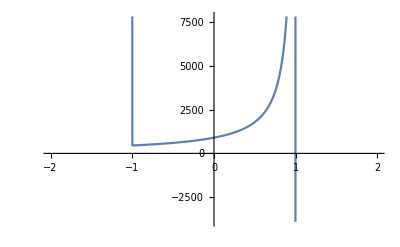

```mathematica
Plot[-(3 (-299+300 r-4701 r^5000+4700 r^5001))/(-1+r)^2,{r,-2,2}]
```

```mathematica
r/.First@NSolve[{3 (-299+300 r-4701 r^5000+4700 r^5001)-600000000000(-1+r)^2==0,r≠1},r,Reals,WorkingPrecision->13]
```

1.002322108633

#### Problem 243 - Resilience

A positive fraction whose numerator is less than its denominator is called a proper fraction.
For any denominator, d, there will be d−1 proper fractions; for example, with d = 12:
1/12 , 2/12 , 3/12 , 4/12 , 5/12 , 6/12 , 7/12 , 8/12 , 9/12 , 10/12 , 11/12 .

We shall call a fraction that cannot be cancelled down a resilient fraction.
Furthermore we shall define the resilience of a denominator, R(d), to be the ratio of its proper fractions that are resilient; for example, R(12) = 4/11 .
In fact, d = 12 is the smallest denominator having a resilience R(d) < 4/10 .

Find the smallest denominator d, having a resilience R(d) < 15499/94744 .

```mathematica
IncreaseWhile[EulerPhi@#/(#-1)≥15499/94744&,#,#]&[Times@@NestWhile[Append[#,NextPrime@Last@#]&,{2},Times@@(1-1/#)≥15499/94744&]]
```

892371480

#### Problem 249 - Prime Subset Sums

Let S = {2, 3, 5, ..., 4999} be the set of prime numbers less than 5000.

Find the number of subsets of S, the sum of whose elements is a prime number.
Enter the rightmost 16 digits as your answer.

```mathematica
(*Slow!*)
Mod[Total@Fold[PadRight[#,Length@#+#2]+PadLeft[#,Length@#+#2]&,SparseArray[1->1,1],PrimeRange@5000][[1+PrimeRange@Total@PrimeRange@5000]],1*^16]
```

9275262564250418

#### Problem 250 - 250250

Find the number of non-empty subsets of {1^1, 2^2, 3^3,..., 250250^250250}, the sum of whose elements is divisible by 250. Enter the rightmost 16 digits as your answer.

```mathematica
Last@Fold[Mod[#+RotateRight[#,#2],1*^16]&,SparseArray[250->1,250],Table[PowerMod[i,i,250],{i,250250}]]-1
```

1425480602091519

### Problem 251 - 275

#### Problem 265 - Binary Circles

2^N binary digits can be placed in a circle so that all the N-digit clockwise subsequences are distinct.

For N=3, two such circular arrangements are possible, ignoring rotations:

-Graphics-

For the first arrangement, the 3-digit subsequences, in clockwise order, are:
000, 001, 010, 101, 011, 111, 110 and 100.

Each circular arrangement can be encoded as a number by concatenating the binary digits starting with the subsequence of all zeros as the most significant bits and proceeding clockwise. The two arrangements for N=3 are thus represented as 23 and 29:
00010111_2 = 23
00011101_2 = 29

Calling S(N) the sum of the unique numeric representations, we can see that S(3) = 23 + 29 = 52.

Find S(5).

```mathematica
Total[FromDigits[#,2]&/@FindCycle[Graph@Cases[Tuples[IntegerDigits[Range[2^5]-1,2,5],2],{x1:{_,y1___},x2:{y2___,_}}/;x1≠x2&&{y1}=={y2}:>x1->x2],{2^5},All][[;;,;;,1,1]]]
```

209110240768

#### Problem 267 - Billionaire

You are given a unique investment opportunity.

Starting with £1 of capital, you can choose a fixed proportion, f, of your capital to bet on a fair coin toss repeatedly for 1000 tosses.

Your return is double your bet for heads and you lose your bet for tails.

For example, if f = 1/4, for the first toss you bet £0.25, and if heads comes up you win £0.5 and so then have £1.5. You then bet £0.375 and if the second toss is tails, you have £1.125.

Choosing f to maximize your chances of having at least £1,000,000,000 after 1,000 flips, what is the chance that you become a billionaire?

All computations are assumed to be exact (no rounding), but give your answer rounded to 12 digits behind the decimal point in the form 0.abcdefghijkl.

```mathematica
N[Sum[Binomial[1000,i]/2^1000,{i,0,Floor@MaxValue[{i/.First@Solve[(1+2f)^(1000-i)(1-f)^i==1000000000,i],0<f<1},f]}],12]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.999992836187

### Problem 276 - 300

#### Problem 277 - A Modified Collatz sequence

A modified Collatz sequence of integers is obtained from a starting value a1 in the following way:

a_(n+1) = a_n/3 if an is divisible by 3. We shall denote this as a large downward step, “D”.

a_(n+1) = (4 a_n + 2)/3 if an divided by 3 gives a remainder of 1. We shall denote this as an upward step, “U”.

a_(n+1) = (2 a_n - 1)/3 if an divided by 3 gives a remainder of 2. We shall denote this as a small downward step, “d”.

The sequence terminates when some a_n = 1.

Given any integer, we can list out the sequence of steps.
For instance if a_1=231, then the sequence {a_n}={231,77,51,17,11,7,10,14,9,3,1} corresponds to the steps “DdDddUUdDD”.

Of course, there are other sequences that begin with that same sequence “DdDddUUdDD....”.
For instance, if a_1=1004064, then the sequence is DdDddUUdDDDdUDUUUdDdUUDDDUdDD.
In fact, 1004064 is the smallest possible a_1 > 10^6 that begins with the sequence DdDddUUdDD.

What is the smallest a_1 > 10^15 that begins with the sequence “UDDDUdddDDUDDddDdDddDDUDDdUUDd”?

```mathematica
Fold[Switch[#2,"D",3#,"U",(3#-2)/4,"d",(3#+1)/2]&,a,Reverse@Characters@"UDDDUdddDDUDDddDdDddDDUDDdUUDd"]//Expand
```

21110037246199/4194304+(205891132094649 a)/4194304

```mathematica
Mod[(21110037246199+205891132094649 a)/4194304/.a->Mod[-21110037246199PowerMod[205891132094649,-1,4194304],4194304],3^StringLength@"UDDDUdddDDUDDddDdDddDDUDDdUUDd",10^15]
```

1125977393124310

#### Problem 293 - Pseudo-Fortunate Numbers

An even positive integer N will be called admissible, if it is a power of 2 or its distinct prime factors are consecutive primes.
The first twelve admissible numbers are 2,4,6,8,12,16,18,24,30,32,36,48.

If N is admissible, the smallest integer M > 1 such that N+M is prime, will be called the pseudo-Fortunate number for N.

For example, N=630 is admissible since it is even and its distinct prime factors are the consecutive primes 2,3,5 and 7.
The next prime number after 631 is 641; hence, the pseudo-Fortunate number for 630 is M=11.
It can also be seen that the pseudo-Fortunate number for 16 is 3.

Find the sum of all distinct pseudo-Fortunate numbers for admissible numbers N less than 10^9.

```mathematica
Times@@Prime@Range@10>1.*^9
```

True

```mathematica
Total@DeleteDuplicates@Table[NextPrime[n+1]-n,{n,Catenate@Rest@FoldList[Catenate[#2^Range@Log[#2,1.*^9/#]#]&,{1},Prime@Range@10]}]
```

2209

#### Problem 297 - Zeckendorf Representation

Each new term in the Fibonacci sequence is generated by adding the previous two terms.
Starting with 1 and 2, the first 10 terms will be: 1, 2, 3, 5, 8, 13, 21, 34, 55, 89.

Every positive integer can be uniquely written as a sum of nonconsecutive terms of the Fibonacci sequence. For example, 100 = 3 + 8 + 89.
Such a sum is called the Zeckendorf representation of the number.

For any integer n>0, let z(n) be the number of terms in the Zeckendorf representation of n.
Thus, z(5) = 1, z(14) = 2, z(100) = 3 etc.
Also, for 0<n<10^6, ∑ z(n) = 7894453.

Find ∑ z(n) for 0<n<10^17.

```mathematica
s[0]=0;
s[1]=1;
s[n_]:=s[n]=s[n-1]+s[n-2]+Fibonacci[n];
```

```mathematica
If[#>0,With[{m=IncreaseWhile[n↦Fibonacci@n≤#]-1},s[m-2]+#-Fibonacci@m+#0[#-Fibonacci@m]],0]&[10^17]
```

2252639041804718029

### Problem 301 - 325

#### Problem 301 - Nim

Nim is a game played with heaps of stones, where two players take it in turn to remove any number of stones from any heap until no stones remain.

We’ll consider the three-heap normal-play version of Nim, which works as follows:
- At the start of the game there are three heaps of stones.
- On his turn the player removes any positive number of stones from any single heap.
- The first player unable to move (because no stones remain) loses.

If (n_1,n_2,n_3) indicates a Nim position consisting of heaps of size n_1, n_2 and n_3 then there is a simple function X(n_1,n_2,n_3) — that you may look up or attempt to deduce for yourself — that returns:

    zero if, with perfect strategy, the player about to move will eventually lose; or
    non-zero if, with perfect strategy, the player about to move will eventually win.

For example X(1,2,3) = 0 because, no matter what the current player does, his opponent can respond with a move that leaves two heaps of equal size, at which point every move by the current player can be mirrored by his opponent until no stones remain; so the current player loses. To illustrate:
- current player moves to (1,2,1)
- opponent moves to (1,0,1)
- current player moves to (0,0,1)
- opponent moves to (0,0,0), and so wins.

For how many positive integers n ≤ 2^30 does X(n,2n,3n) = 0 ?

```mathematica
Fibonacci[30+2]
```

2178309

#### Problem 303 - Multiples with small digits

For a positive integer n, define f(n) as the least positive multiple of n that, written in base 10, uses only digits ≤ 2.

Thus f(2)=2, f(3)=12, f(7)=21, f(42)=210, f(89)=1121222.

Also, -Graphics-.

Find -Graphics-.

```mathematica
f[1]=1;
f[999]=111222222222222;
f[9999]=11112222222222222222;
f[n_]:=f[n]=FixedPoint[a↦If[#==0,a,a+Ceiling[10^IntegerLength@#-#,n]]&@FromDigits[IntegerDigits@a//.{0|1|2,d___}:>{d}],Ceiling[f[Divisors[n][[-2]]],n]];
Sum[f[n]/n,{n,10000}]
```

1111981904675169

#### Problem 315 - Digital root clocks

Sam and Max are asked to transform two digital clocks into two “digital root” clocks.
A digital root clock is a digital clock that calculates digital roots step by step.

When a clock is fed a number, it will show it and then it will start the calculation, showing all the intermediate values until it gets to the result.
For example, if the clock is fed the number 137, it will show: “137” → “11” → “2” and then it will go black, waiting for the next number.

Every digital number consists of some light segments: three horizontal (top, middle, bottom) and four vertical (top-left, top-right, bottom-left, bottom-right).
Number “1” is made of vertical top-right and bottom-right, number “4” is made by middle horizontal and vertical top-left, top-right and bottom-right. Number “8” lights them all.

The clocks consume energy only when segments are turned on/off.
To turn on a “2” will cost 5 transitions, while a “7” will cost only 4 transitions.

Sam and Max built two different clocks.

Sam’s clock is fed e.g. number 137: the clock shows “137”, then the panel is turned off, then the next number (“11”) is turned on, then the panel is turned off again and finally the last number (“2”) is turned on and, after some time, off.
For the example, with number 137, Sam’s clock requires:
“137” 	: 	(2 + 5 + 4) × 2 = 22 transitions (“137” on/off).
“11” 	: 	(2 + 2) × 2 = 8 transitions (“11” on/off).
“2” 	: 	(5) × 2 = 10 transitions (“2” on/off).
For a grand total of 40 transitions.

Max’s clock works differently. Instead of turning off the whole panel, it is smart enough to turn off only those segments that won’t be needed for the next number.
For number 137, Max’s clock requires:
“137”	:	2 + 5 + 4 = 11 transitions (“137” on)
		7 transitions (to turn off the segments that are not needed for number “11”).
“11”	:	0 transitions (number “11” is already turned on correctly)
		3 transitions (to turn off the first “1” and the bottom part of the second “1”;
		the top part is common with number “2”).
“2”	:	4 transitions (to turn on the remaining segments in order to get a “2”)
		5 transitions (to turn off number “2”).
For a grand total of 30 transitions.

Of course, Max’s clock consumes less power than Sam’s one.
The two clocks are fed all the prime numbers between A = 10^7 and B = 2×10^7.
Find the difference between the total number of transitions needed by Sam’s clock and that needed by Max’s one.

```mathematica
ParallelSum[2Total[DigitCount[BitAnd[Take[#1,-Length@#2],#2],2,1]&@@@Partition[IntegerDigits@Most@FixedPointList[Total@*IntegerDigits,p]/.{0->126,1->48,2->109,3->121,4->51,5->91,6->95,7->114,8->127,9->123},2,1],2],{p,PrimeRange[1*^7,2*^7]}]
```

13625242

#### Problem 323 - Bitwise-OR operations on random integers

Let y_0, y_1, y_2,... be a sequence of random unsigned 32 bit integers
(i.e. 0 ≤ y_i < 2^32, every value equally likely).

For the sequence xi the following recursion is given:

    x_0 = 0 and
    x_i = x_(i-1) | y_(i-1), for i > 0. ( | is the bitwise-OR operator)

It can be seen that eventually there will be an index N such that x_i = 2^32 -1 (a bit-pattern of all ones) for all i ≥ N.

Find the expected value of N.
Give your answer rounded to 10 digits after the decimal point.

```mathematica
N[e[32]/.First@Solve[Prepend[Table[e[n]==1+Array[e,n+1,0].Binomial[n,Range[0,n]]/2^n,{n,32}],e[0]==0],Array[e,32+1,0]],11]
```

6.3551758451

### Problem 326 - 350

#### Problem 345 - Matrix Sum

We define the Matrix Sum of a matrix as the maximum sum of matrix elements with each element being the only one in his row and column. For example, the Matrix Sum of the matrix below equals 3315 ( = 863 + 383 + 343 + 959 + 767):

7 | 53 | 183 | 439 | 863
497 | 383 | 563 | 79 | 973
287 | 63 | 343 | 169 | 583
627 | 343 | 773 | 959 | 943
767 | 473 | 103 | 699 | 303

Find the Matrix Sum of:

7 | 53 | 183 | 439 | 863 | 497 | 383 | 563 | 79 | 973 | 287 | 63 | 343 | 169 | 583
627 | 343 | 773 | 959 | 943 | 767 | 473 | 103 | 699 | 303 | 957 | 703 | 583 | 639 | 913
447 | 283 | 463 | 29 | 23 | 487 | 463 | 993 | 119 | 883 | 327 | 493 | 423 | 159 | 743
217 | 623 | 3 | 399 | 853 | 407 | 103 | 983 | 89 | 463 | 290 | 516 | 212 | 462 | 350
960 | 376 | 682 | 962 | 300 | 780 | 486 | 502 | 912 | 800 | 250 | 346 | 172 | 812 | 350
870 | 456 | 192 | 162 | 593 | 473 | 915 | 45 | 989 | 873 | 823 | 965 | 425 | 329 | 803
973 | 965 | 905 | 919 | 133 | 673 | 665 | 235 | 509 | 613 | 673 | 815 | 165 | 992 | 326
322 | 148 | 972 | 962 | 286 | 255 | 941 | 541 | 265 | 323 | 925 | 281 | 601 | 95 | 973
445 | 721 | 11 | 525 | 473 | 65 | 511 | 164 | 138 | 672 | 18 | 428 | 154 | 448 | 848
414 | 456 | 310 | 312 | 798 | 104 | 566 | 520 | 302 | 248 | 694 | 976 | 430 | 392 | 198
184 | 829 | 373 | 181 | 631 | 101 | 969 | 613 | 840 | 740 | 778 | 458 | 284 | 760 | 390
821 | 461 | 843 | 513 | 17 | 901 | 711 | 993 | 293 | 157 | 274 | 94 | 192 | 156 | 574
34 | 124 | 4 | 878 | 450 | 476 | 712 | 914 | 838 | 669 | 875 | 299 | 823 | 329 | 699
815 | 559 | 813 | 459 | 522 | 788 | 168 | 586 | 966 | 232 | 308 | 833 | 251 | 631 | 107
813 | 883 | 451 | 509 | 615 | 77 | 281 | 613 | 459 | 205 | 380 | 274 | 302 | 35 | 805

```mathematica
matrix=ImportString["  7  53 183 439 863 497 383 563  79 973 287  63 343 169 583
627 343 773 959 943 767 473 103 699 303 957 703 583 639 913
447 283 463  29  23 487 463 993 119 883 327 493 423 159 743
217 623   3 399 853 407 103 983  89 463 290 516 212 462 350
960 376 682 962 300 780 486 502 912 800 250 346 172 812 350
870 456 192 162 593 473 915  45 989 873 823 965 425 329 803
973 965 905 919 133 673 665 235 509 613 673 815 165 992 326
322 148 972 962 286 255 941 541 265 323 925 281 601  95 973
445 721  11 525 473  65 511 164 138 672  18 428 154 448 848
414 456 310 312 798 104 566 520 302 248 694 976 430 392 198
184 829 373 181 631 101 969 613 840 740 778 458 284 760 390
821 461 843 513  17 901 711 993 293 157 274  94 192 156 574
 34 124   4 878 450 476 712 914 838 669 875 299 823 329 699
815 559 813 459 522 788 168 586 966 232 308 833 251 631 107
813 883 451 509 615  77 281 613 459 205 380 274 302  35 805","Table"];
```

```mathematica
sum[{}]=0;
sum[m_]:=sum[m]=Max@Table[m[[1,n]]+sum[Drop[m,1,{n}]],{n,Length@m}];
sum[matrix]
```

13938

#### Problem 346 - Strong Repunits

The number 7 is special, because 7 is 111 written in base 2, and 11 written in base 6
(i.e. 7_10 = 11_6= 111_2). In other words, 7 is a repunit in at least two bases b > 1.

We shall call a positive integer with this property a strong repunit. It can be verified that there are 8 strong repunits below 50: {1,7,13,15,21,31,40,43}.
Furthermore, the sum of all strong repunits below 1000 equals 15864.
Find the sum of all strong repunits below 10^12.

```mathematica
1+Total[Union@@Table[(b^l-1)/(b-1),{b,2,Sqrt@1*^12},{l,3,Log[b,1*^12(b-1)+1.]}]]
```

336108797689259276

#### Problem 347 - Largest integer divisible by two primes

The largest integer ≤ 100 that is only divisible by both the primes 2 and 3 is 96, as 96=32*3=2^5*3. For two distinct primes p and q let M(p,q,N) be the largest positive integer ≤N only divisible by both p and q and M(p,q,N)=0 if such a positive integer does not exist.

E.g. M(2,3,100)=96.
M(3,5,100)=75 and not 90 because 90 is divisible by 2 ,3 and 5.
Also M(2,73,100)=0 because there does not exist a positive integer ≤ 100 that is divisible by both 2 and 73.

Let S(N) be the sum of all distinct M(p,q,N). S(100)=2262.

Find S(10 000 000).

```mathematica
ParallelSum[Max[p^Floor@Log[p,10000000./#]#&[q^Range@Log[q,10000000./p]]],{p,PrimeRange[Sqrt@10000000.]},{q,PrimeRange[p+1,10000000./p]}]
```

11109800204052

### Problem 351 - 375

#### Problem 357 - Prime generating integers

Consider the divisors of 30: 1,2,3,5,6,10,15,30.
It can be seen that for every divisor d of 30, d+30/d is prime.

Find the sum of all positive integers n not exceeding 100 000 000
such that for every divisor d of n, d+n/d is prime.

```mathematica
1+ParallelSum[With[{n=2Prime[p]-4},If[AllTrue[Divisors@n, PrimeQ[#+n/#]&],n,0]],{p,2,PrimePi[100000000/2+2]}]
```

1739023853137

### Problem 376 - 400

#### Problem 381 - (prime-k) factorial

For a prime p let S(p) = (∑(p-k)!) mod(p) for 1 ≤ k ≤ 5.

For example, if p=7,
(7-1)! + (7-2)! + (7-3)! + (7-4)! + (7-5)! = 6! + 5! + 4! + 3! + 2! = 720+120+24+6+2 = 872.
As 872 mod(7) = 4, S(7) = 4.

It can be verified that ∑S(p) = 480 for 5 ≤ p < 100.

Find ∑S(p) for 5 ≤ p < 10^8.

```mathematica
ParallelSum[Mod[-1+Total@FoldList[Times,1,PowerMod[p-Range[2,4],-1,p]],p],{p,PrimeRange[5,10^8]}]
```

139602943319822

#### Problem 387 - Harshad Numbers

A Harshad or Niven number is a number that is divisible by the sum of its digits.
201 is a Harshad number because it is divisible by 3 (the sum of its digits.)
When we truncate the last digit from 201, we get 20, which is a Harshad number.
When we truncate the last digit from 20, we get 2, which is also a Harshad number.
Let’s call a Harshad number that, while recursively truncating the last digit, always results in a Harshad number a right truncatable Harshad number.

Also:
201/3=67 which is prime.
Let’s call a Harshad number that, when divided by the sum of its digits, results in a prime a strong Harshad number.

Now take the number 2011 which is prime.
When we truncate the last digit from it we get 201, a strong Harshad number that is also right truncatable.
Let’s call such primes strong, right truncatable Harshad primes.

You are given that the sum of the strong, right truncatable Harshad primes less than 10000 is 90619.

Find the sum of the strong, right truncatable Harshad primes less than 10^14.

```mathematica
Total[Select[10#+Range@9,PrimeQ]&/@Select[Catenate@NestList[Select[Catenate@Outer[10#1+#2&,#,Range[0,9]],IntegerQ[#/Total@IntegerDigits@#]&]&,Range@9,12],PrimeQ[#/Total@IntegerDigits@#]&],2]
```

696067597313468

### Problem 476 - 500

#### Problem 493 - Under The Rainbow

70 colored balls are placed in an urn, 10 for each of the seven rainbow colors.

What is the expected number of distinct colors in 20 randomly picked balls?

Give your answer with nine digits after the decimal point (a.bcdefghij).

```mathematica
N[Total@KeyValueMap[Times,Merge[<|Count[#,Except@0]->Length@Permutations@#*Times@@Binomial[10,#]|>&/@IntegerPartitions[20,{7},Range[0,10]],Total]/Binomial[70,20]],10]
```

6.818741802